# Functional Programming

Peter Cullen Burbery

Abstract

## Creating Functions

## Basic Examples of Functional Programming

### Function

XXXX:

```mathematica
Function[u,3+u][x]
```

3+x

```mathematica
Function[u,3+u][x]
```

3+x

```mathematica
Function[3+#][x]
```

3+x

```mathematica
(3+#)&[x]
```

3+x

```mathematica
Function[{u,v},u^2+v^4][x,y]
```

x^2+y^4

```mathematica
(#1^2+#2^4)&[x,y]
```

x^2+y^4

```mathematica
f=(3+#)&
```

3+#1&

```mathematica
{f[a],f[b]}
```

{3+a,3+b}

```mathematica
f[#u,#v,#u]&[<|"u"->x,"v"->y|>]
```

3+x

This might be a bug. The documentation says the output is f[x,y,x].

### Slot

```mathematica
f[#,a,#,b]&[x,y]
```

f[x,a,x,b]

```mathematica
f[#1,#2,#1,#3]&[x,y,z]
```

f[x,y,x,z]

```mathematica
f[#u,#v,#u]&[<|"u"->x,"v"->y|>]
```

f[x,y,x]

### SlotSequence

```mathematica
ClearAll[f]
```

```mathematica
f[x,##,y,##]&[a,b,c,d]
```

f[x,a,b,c,d,y,a,b,c,d]

```mathematica
f[##2]&[a,b,c,d]
```

f[b,c,d]

```mathematica
f[##3]&[a,b,c,d]
```

f[c,d]

```mathematica
f[##4]&[a,b,c,d]
```

f[d]

## Neat Examples

### Function

```mathematica
r[g_,h_]=If[#1==0,g[##2],h[#0[#1-1,##2],#1-1,##2]]&
```

If[#1==0,g[##2],h[#0[#1-1,##2],#1-1,##2]]&

```mathematica
r[1&,#1(#2+1)&][10]
```

3628800

```mathematica
r[1&,#1(#2+1)&][100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
NewtonZero[f_,x0_]:=FixedPoint[#-f[#]/f'[#]&,x0]
```

```mathematica
NewtonZero[BesselJ[2,#]&,5.0]
```

5.13562

```mathematica
NewtonZero[BesselJ[2,#]&,718.]
```

718.637

### Slot

```mathematica
f=If[#1==1,1,#1 #0[#1-1]]&
```

If[#1==1,1,#1 #0[#1-1]]&

```mathematica
f[10]
```

3628800

```mathematica
10!
```

3628800

## Applying Functions to Lists

## Basic Examples

### Map

XXXX:

```mathematica
Map[f,{a,b,c,d,e}]
```

{f[a],f[b],f[c],f[d],f[e]}

Alternative input form:

```mathematica
f/@{a,b,c,d,e}
```

{f[a],f[b],f[c],f[d],f[e]}

```mathematica
(1+g[#])&/@{a,b,c,d,e}
```

{1+g[a],1+g[b],1+g[c],1+g[d],1+g[e]}

```mathematica
Function[x,x^2]/@{1,2,3,4}
```

{1,4,9,16}

Map at top level:

```mathematica
ExpressionTree[{{a,b},{c,d,e}}]
```

-Graphics-

```mathematica
Map[f,{{a,b},{c,d,e}}]
```

{f[{a,b}],f[{c,d,e}]}

```mathematica
ExpressionTree[Map[f,{{a,b},{c,d,e}}]]
```

-Graphics-

Map at level 2:

```mathematica
Map[f,{{a,b},{c,d,e}},{2}]
```

{{f[a],f[b]},{f[c],f[d],f[e]}}

```mathematica
ExpressionTree[Map[f,{{a,b},{c,d,e}},{2}]]
```

-Graphics-

Map at levels 1 and 2:

```mathematica
Map[f,{{a,b},{c,d,e}},2]
```

{f[{f[a],f[b]}],f[{f[c],f[d],f[e]}]}

```mathematica
ExpressionTree[Map[f,{{a,b},{c,d,e}},2]]
```

-Graphics-

Test a depth tree expression:

```mathematica
PersistResourceFunction["SymbolicIndexedArray"]
```

Success[…]

```mathematica
EXPRESSION=SymbolicIndexedArray[x,{3,3,3}]
```

{{{x111,x112,x113},{x121,x122,x123},{x131,x132,x133}},{{x211,x212,x213},{x221,x222,x223},{x231,x232,x233}},{{x311,x312,x313},{x321,x322,x323},{x331,x332,x333}}}

```mathematica
ExpressionTree[EXPRESSION]
```

-Graphics-

```mathematica
RootTree[ExpressionTree[EXPRESSION],3]
```

-Graphics-

```mathematica
RootTree[ExpressionTree[EXPRESSION],2]
```

-Graphics-

```mathematica
RootTree[ExpressionTree[EXPRESSION],3]
```

-Graphics-

```mathematica
Map[f,EXPRESSION]
```

{f[{{x111,x112,x113},{x121,x122,x123},{x131,x132,x133}}],f[{{x211,x212,x213},{x221,x222,x223},{x231,x232,x233}}],f[{{x311,x312,x313},{x321,x322,x323},{x331,x332,x333}}]}

```mathematica
RootTree[ExpressionTree[Map[f,EXPRESSION]],4]
```

-Graphics-

```mathematica
RootTree[ExpressionTree[Map[f,EXPRESSION,{2}]],4]
```

-Graphics-

```mathematica
RootTree[ExpressionTree[Map[f,EXPRESSION,{3}]],4]
```

-Graphics-

```mathematica
RootTree[ExpressionTree[Map[f,EXPRESSION,Infinity]],5]
```

-Graphics-

```mathematica
RootTree[ExpressionTree[Map[f,EXPRESSION,{2,3}]],5]
```

-Graphics-

Use the map operator:

```mathematica
Map[f][{a,b,c,d}]
```

{f[a],f[b],f[c],f[d]}

Map over an association:

```mathematica
Map[h,<|a->b,c->d|>]
```

<|a→h[b],c→h[d]|>

Map at the second level of a nested Association:

```mathematica
Map[h,<|a-><|b->c|>,d->{<|e->f|>}|>,{1,3}]
```

<|a→h[<|b→h[c]|>],d→h[{h[<|e→h[f]|>]}]|>

### Apply

```mathematica
Apply[f,{a,b,c,d}]
```

f[a,b,c,d]

```mathematica
f@@{a,b,c,d}
```

f[a,b,c,d]

```mathematica
Plus@@{a,b,c,d}
```

a+b+c+d

```mathematica
f@@{{a,b},{c},d}
```

f[{a,b},{c},d]

Use the operator form of Apply:

```mathematica
Apply[f][{{a,b},{c},d}]
```

f[{a,b},{c},d]

Apply f to an Association:

```mathematica
Apply[f,<|1->a,2->b,3->c|>]
```

f[a,b,c]

Applying a List to an association is equivalent to using Values:

```mathematica
Apply[List,<|1->a,2->b,3->c,4->{d}|>]
```

{a,b,c,{d}}

```mathematica
Values[<|1->a,2->b,3->c,4->{d}|>]
```

{a,b,c,{d}}

Apply f at the second level:

```mathematica
Apply[List,<|1->a,2->b,3->c,4->{d,{e}}|>,{2}]
```

<|1→a,2→b,3→c,4→{d,{e}}|>

Apply f at several levels:

```mathematica
Apply[List,<|1->a,2->b,3->c,4->{d,{e}}|>,{0,2}]
```

{a,b,c,{d,{e}}}

### MapApply

```mathematica
MapApply[f,{{a,b},{c,d}}]
```

{f[a,b],f[c,d]}

```mathematica
f@@@{{a,b},{c,d}}
```

{f[a,b],f[c,d]}

Sum sublists by replacing the head of each with Plus:

```mathematica
Plus@@@{{a,b,c,d},{1,2,3,4},{e,f,5,6}}
```

{a+b+c+d,10,11+e+f}

```mathematica
Times@@@{{a,b,c,d},{1,2,3,4},{e,f,5,6}}
```

{a b c d,24,30 e f}

Use the operator form of MapApply:

```mathematica
MapApply[f][{{a,b},{c},{d,e}}]
```

{f[a,b],f[c],f[d,e]}

MapApply only affects the values of an association:

```mathematica
MapApply[f,<|{1,2}->{a},{3,4}->{c,d,e}|>]
```

<|{1,2}→f[a],{3,4}→f[c,d,e]|>

### MapIndexed

```mathematica
MapIndexed[f,{a,b,c,d}]
```

{f[a,{1}],f[b,{2}],f[c,{3}],f[d,{4}]}

#2 gives the indices of each part:

```mathematica
MapIndexed[First[#2]+f[#1]&,{a,b,c,d}]
```

{1+f[a],2+f[b],3+f[c],4+f[d]}

```mathematica
MapIndexed[First[#2]f[#1]&,{a,b,c,d}]
```

{f[a],2 f[b],3 f[c],4 f[d]}

```mathematica
MapIndexed[First[#2]f[#1]&,Range[4]]
```

{f[1],2 f[2],3 f[3],4 f[4]}

```mathematica
MapIndexed[First[#2]f[#1]&,Range[20]]
```

{f[1],2 f[2],3 f[3],4 f[4],5 f[5],6 f[6],7 f[7],8 f[8],9 f[9],10 f[10],11 f[11],12 f[12],13 f[13],14 f[14],15 f[15],16 f[16],17 f[17],18 f[18],19 f[19],20 f[20]}

```mathematica
MapIndexed[First[#2]f[#1]&,Range[100,120]]
```

{f[100],2 f[101],3 f[102],4 f[103],5 f[104],6 f[105],7 f[106],8 f[107],9 f[108],10 f[109],11 f[110],12 f[111],13 f[112],14 f[113],15 f[114],16 f[115],17 f[116],18 f[117],19 f[118],20 f[119],21 f[120]}

```mathematica
MapIndexed[f,{{a,b},{c,d,e}}]
```

{f[{a,b},{1}],f[{c,d,e},{2}]}

```mathematica
MapIndexed[f,{{a,b},{c,d,e}},{2}]
```

{{f[a,{1,1}],f[b,{1,2}]},{f[c,{2,1}],f[d,{2,2}],f[e,{2,3}]}}

Map over an association:

```mathematica
MapIndexed[f,<|"a"->1,a->2,1->1|>]
```

<|a→f[1,{Key[a]}],a→f[2,{Key[a]}],1→f[1,{Key[1]}]|>

### MapThread

Apply f to corresponding pairs of elements:

```mathematica
MapThread[f,{{a,b,c},{x,y,z}}]
```

{f[a,x],f[b,y],f[c,z]}

Apply f to elements of a matrix:

```mathematica
MapThread[f,{{{a,b},{c,d}},{{u,v},{s,t}}},2]
```

{{f[a,u],f[b,v]},{f[c,s],f[d,t]}}

Apply f to corresponding values of associations:

```mathematica
MapThread[f,{<|a->1|>,<|a->1|>}]
```

<|a→f[1,1]|>

Use the operator form of MapThread:

```mathematica
MapThread[f][{{a,b,c,d},{1,2,3,4}}]
```

{f[a,1],f[b,2],f[c,3],f[d,4]}

### MapAt

Map f onto the part at position 2:

```mathematica
MapAt[f,{a,b,c,d},2]
```

{a,f[b],c,d}

Map f onto multiple parts:

```mathematica
MapAt[f,{a,b,c,d},{{1},{4}}]
```

{f[a],b,c,f[d]}

Map f onto a more deeply nested part:

```mathematica
MapAt[f,{{a,b,c},{d,e}},{2,1}]
```

{{a,b,c},{f[d],e}}

Map f onto the second element on all top-level parts (the "second column"):

```mathematica
MapAt[f,{{a,b,c},{d,e}},{All,2}]
```

{{a,f[b],c},{d,f[e]}}

Map f onto an association:

```mathematica
MapAt[f,<|"a"->1,"b"->2,"c"->3,"d"->4,"e"->5|>,3]
```

<|a→1,b→2,c→f[3],d→4,e→5|>

Use Key to specify position:

```mathematica
MapAt[f,<|"a"->1,"b"->2,"c"->3,"d"->4,"e"->5|>,Key["b"]]
```

<|a→1,b→f[2],c→3,d→4,e→5|>

For string keys, Key is not needed:

```mathematica
MapAt[f,<|"a"->1,"b"->2,"c"->3,"d"->4,"e"->5|>,"b"]
```

<|a→1,b→f[2],c→3,d→4,e→5|>

Use negative position in an association:

```mathematica
MapAt[f,<|"a"->1,"b"->2,"c"->3,"d"->4,"e"->5|>,-3]
```

<|a→1,b→2,c→f[3],d→4,e→5|>

Use the operator form of MapAt:

```mathematica
MapAt[f,1][{a,b,c,d}]
```

{f[a],b,c,d}

### MapAll

Apply f to every subpart of an expression:

```mathematica
MapAll[f,{{a,b},{c},{{d}}}]
```

f[{f[{f[a],f[b]}],f[{f[c]}],f[{f[{f[d]}]}]}]

```mathematica
ExpressionTree[{{a,b},{c},{{d}}}]
```

-Graphics-

```mathematica
ExpressionTree[MapAll[f,{{a,b},{c},{{d}}}]]
```

-Graphics-

Alternative input form:

```mathematica
f//@{{a,b},{c},{{d}}}
```

f[{f[{f[a],f[b]}],f[{f[c]}],f[{f[{f[d]}]}]}]

Apply h to every value in associations:

```mathematica
MapAll[h,<|a-><|b->c|>,d->{<|e->f|>}|>]
```

h[<|a→h[<|b→h[c]|>],d→h[{h[<|e→h[f]|>]}]|>]

### Scan

```mathematica
Scan[Print,{a,b,c}]
```

a

b

c

```mathematica
Scan[Print[#^2]&,{2,3,4}]
```

4

9

16

Scan elements of an Association:

```mathematica
Scan[Print,<|1->a,2->b,3->c|>]
```

a

b

c

Scan elements up to the second level:

```mathematica
Scan[Print,<|1->{{a}},2->b|>,2]
```

{a}

{{a}}

b

Scan elements up to the 0th level:

```mathematica
Scan[Print,<|1->{{a}},2->b|>,{0,Infinity}]
```

a

{a}

{{a}}

b

<|1→{{a}},2→b|>

Use the operator form of Scan:

```mathematica
Scan[Print][{a,b,c}]
```

a

b

c

### BlockMap

Apply a function to all non-overlapping length-2 sublists:

```mathematica
BlockMap[f,Range[10],2]
```

{f[{1,2}],f[{3,4}],f[{5,6}],f[{7,8}],f[{9,10}]}

Apply a function to overlapping sublists of length 2 with offset 1:

```mathematica
BlockMap[f,Range[10],2,1]
```

{f[{1,2}],f[{2,3}],f[{3,4}],f[{4,5}],f[{5,6}],f[{6,7}],f[{7,8}],f[{8,9}],f[{9,10}]}

Apply a function to a matrix:

```mathematica
BlockMap[f,({{1, 2, 3, 4}, {10, 20, 30, 40}, {100, 200, 300, 400}, {1000, 2000, 3000, 4000}}),2]
```

{f[{{1,2,3,4},{10,20,30,40}}],f[{{100,200,300,400},{1000,2000,3000,4000}}]}

```mathematica
Map[MatrixForm,BlockMap[f,({{1, 2, 3, 4}, {10, 20, 30, 40}, {100, 200, 300, 400}, {1000, 2000, 3000, 4000}}),2],{2}]
```

{f[(1 | 2 | 3 | 4
10 | 20 | 30 | 40)],f[(100 | 200 | 300 | 400
1000 | 2000 | 3000 | 4000)]}

Apply a function to all 2x2 sub-matrices:

```mathematica
BlockMap[f,({{1, 2, 3, 4}, {10, 20, 30, 40}, {100, 200, 300, 400}, {1000, 2000, 3000, 4000}}),{2,2}]
```

{{f[{{1,2},{10,20}}],f[{{3,4},{30,40}}]},{f[{{100,200},{1000,2000}}],f[{{300,400},{3000,4000}}]}}

```mathematica
MatrixForm@Map[MatrixForm,BlockMap[f,({{1, 2, 3, 4}, {10, 20, 30, 40}, {100, 200, 300, 400}, {1000, 2000, 3000, 4000}}),{2,2}],{3}]
```

(f[(1 | 2
10 | 20)] | f[(3 | 4
30 | 40)]
f[(100 | 200
1000 | 2000)] | f[(300 | 400
3000 | 4000)])

### SubsetMap

Reverse elements at position 2 and 4:

```mathematica
SymbolicIndexedArray[x,6]
```

{x1,x2,x3,x4,x5,x6}

```mathematica
SubsetMap[Reverse,SymbolicIndexedArray[x,6],{2,4}]
```

{x1,x4,x3,x2,x5,x6}

Extract, rotate and reinsert elements at positions 2, 4, and 5:

```mathematica
SubsetMap[RotateLeft,SymbolicIndexedArray[x,6],{2,4,5}]
```

{x1,x4,x3,x5,x2,x6}

Extract, accumulate and reinsert elements at positions 2 to 5:

```mathematica
SubsetMap[Accumulate,SymbolicIndexedArray[x,6],2;;5]
```

{x1,x2,x2+x3,x2+x3+x4,x2+x3+x4+x5,x6}

Reverse the elements of the diagonal of a matrix:

```mathematica
SymbolicIndexedArray[x,{3,3}]
```

{{x11,x12,x13},{x21,x22,x23},{x31,x32,x33}}

```mathematica
SubsetMap[Reverse,SymbolicIndexedArray[x,{3,3}],{{1,1},{2,2},{3,3}}]//MatrixForm
```

(x33 | x12 | x13
x21 | x22 | x23
x31 | x32 | x11)

Accumulate the elements of the second column of a matrix:

```mathematica
SubsetMap[Accumulate,SymbolicIndexedArray[x,{3,3}],{All,2}]//MatrixForm
```

(x11 | x12 | x13
x21 | x12+x22 | x23
x31 | x12+x22+x32 | x33)

## Applications

### Map

Reverse all sublists:

```mathematica
Reverse/@{{a,b},{c,d},{e,f}}
```

{{b,a},{d,c},{f,e}}

Add the same vector to every vector in a list:

```mathematica
Map[(#+{x,y})&,{{1,1},{2,2},{3,3},{4,4}}]
```

{{1+x,1+y},{2+x,2+y},{3+x,3+y},{4+x,4+y}}

Use Threaded:

```mathematica
Threaded[{x,y}]+{{1,1},{2,2},{3,3},{4,4}}
```

{{1+x,1+y},{2+x,2+y},{3+x,3+y},{4+x,4+y}}

```mathematica
{{1,1},{2,2},{3,3},{4,4}}+Threaded[{x,y}]
```

{{1+x,1+y},{2+x,2+y},{3+x,3+y},{4+x,4+y}}

Frame integers that are prime:

```mathematica
If[PrimeQ[#],Framed[#],#]&/@Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Make a grid:

```mathematica
If[PrimeQ[#],Framed[#],#]&/@Range[148]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148}

```mathematica
Partition[If[PrimeQ[#],Framed[#],#]&/@Range[148],UpTo[10]]
```

{{1,2,3,4,5,6,7,8,9,10},{11,12,13,14,15,16,17,18,19,20},{21,22,23,24,25,26,27,28,29,30},{31,32,33,34,35,36,37,38,39,40},{41,42,43,44,45,46,47,48,49,50},{51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70},{71,72,73,74,75,76,77,78,79,80},{81,82,83,84,85,86,87,88,89,90},{91,92,93,94,95,96,97,98,99,100},{101,102,103,104,105,106,107,108,109,110},{111,112,113,114,115,116,117,118,119,120},{121,122,123,124,125,126,127,128,129,130},{131,132,133,134,135,136,137,138,139,140},{141,142,143,144,145,146,147,148}}

```mathematica
Multicolumn[If[PrimeQ[#],Framed[#],#]&/@Range[148]]
```

1 | 13 | 25 | 37 | 49 | 61 | 73 | 85 | 97 | 109 | 121 | 133 | 145
2 | 14 | 26 | 38 | 50 | 62 | 74 | 86 | 98 | 110 | 122 | 134 | 146
3 | 15 | 27 | 39 | 51 | 63 | 75 | 87 | 99 | 111 | 123 | 135 | 147
4 | 16 | 28 | 40 | 52 | 64 | 76 | 88 | 100 | 112 | 124 | 136 | 148
5 | 17 | 29 | 41 | 53 | 65 | 77 | 89 | 101 | 113 | 125 | 137 | 
6 | 18 | 30 | 42 | 54 | 66 | 78 | 90 | 102 | 114 | 126 | 138 | 
7 | 19 | 31 | 43 | 55 | 67 | 79 | 91 | 103 | 115 | 127 | 139 | 
8 | 20 | 32 | 44 | 56 | 68 | 80 | 92 | 104 | 116 | 128 | 140 | 
9 | 21 | 33 | 45 | 57 | 69 | 81 | 93 | 105 | 117 | 129 | 141 | 
10 | 22 | 34 | 46 | 58 | 70 | 82 | 94 | 106 | 118 | 130 | 142 | 
11 | 23 | 35 | 47 | 59 | 71 | 83 | 95 | 107 | 119 | 131 | 143 | 
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144 |

```mathematica
Multicolumn[If[PrimeQ[#],Framed[#],#]&/@Range[403]]
```

1 | 21 | 41 | 61 | 81 | 101 | 121 | 141 | 161 | 181 | 201 | 221 | 241 | 261 | 281 | 301 | 321 | 341 | 361 | 381 | 401
2 | 22 | 42 | 62 | 82 | 102 | 122 | 142 | 162 | 182 | 202 | 222 | 242 | 262 | 282 | 302 | 322 | 342 | 362 | 382 | 402
3 | 23 | 43 | 63 | 83 | 103 | 123 | 143 | 163 | 183 | 203 | 223 | 243 | 263 | 283 | 303 | 323 | 343 | 363 | 383 | 403
4 | 24 | 44 | 64 | 84 | 104 | 124 | 144 | 164 | 184 | 204 | 224 | 244 | 264 | 284 | 304 | 324 | 344 | 364 | 384 | 
5 | 25 | 45 | 65 | 85 | 105 | 125 | 145 | 165 | 185 | 205 | 225 | 245 | 265 | 285 | 305 | 325 | 345 | 365 | 385 | 
6 | 26 | 46 | 66 | 86 | 106 | 126 | 146 | 166 | 186 | 206 | 226 | 246 | 266 | 286 | 306 | 326 | 346 | 366 | 386 | 
7 | 27 | 47 | 67 | 87 | 107 | 127 | 147 | 167 | 187 | 207 | 227 | 247 | 267 | 287 | 307 | 327 | 347 | 367 | 387 | 
8 | 28 | 48 | 68 | 88 | 108 | 128 | 148 | 168 | 188 | 208 | 228 | 248 | 268 | 288 | 308 | 328 | 348 | 368 | 388 | 
9 | 29 | 49 | 69 | 89 | 109 | 129 | 149 | 169 | 189 | 209 | 229 | 249 | 269 | 289 | 309 | 329 | 349 | 369 | 389 | 
10 | 30 | 50 | 70 | 90 | 110 | 130 | 150 | 170 | 190 | 210 | 230 | 250 | 270 | 290 | 310 | 330 | 350 | 370 | 390 | 
11 | 31 | 51 | 71 | 91 | 111 | 131 | 151 | 171 | 191 | 211 | 231 | 251 | 271 | 291 | 311 | 331 | 351 | 371 | 391 | 
12 | 32 | 52 | 72 | 92 | 112 | 132 | 152 | 172 | 192 | 212 | 232 | 252 | 272 | 292 | 312 | 332 | 352 | 372 | 392 | 
13 | 33 | 53 | 73 | 93 | 113 | 133 | 153 | 173 | 193 | 213 | 233 | 253 | 273 | 293 | 313 | 333 | 353 | 373 | 393 | 
14 | 34 | 54 | 74 | 94 | 114 | 134 | 154 | 174 | 194 | 214 | 234 | 254 | 274 | 294 | 314 | 334 | 354 | 374 | 394 | 
15 | 35 | 55 | 75 | 95 | 115 | 135 | 155 | 175 | 195 | 215 | 235 | 255 | 275 | 295 | 315 | 335 | 355 | 375 | 395 | 
16 | 36 | 56 | 76 | 96 | 116 | 136 | 156 | 176 | 196 | 216 | 236 | 256 | 276 | 296 | 316 | 336 | 356 | 376 | 396 | 
17 | 37 | 57 | 77 | 97 | 117 | 137 | 157 | 177 | 197 | 217 | 237 | 257 | 277 | 297 | 317 | 337 | 357 | 377 | 397 | 
18 | 38 | 58 | 78 | 98 | 118 | 138 | 158 | 178 | 198 | 218 | 238 | 258 | 278 | 298 | 318 | 338 | 358 | 378 | 398 | 
19 | 39 | 59 | 79 | 99 | 119 | 139 | 159 | 179 | 199 | 219 | 239 | 259 | 279 | 299 | 319 | 339 | 359 | 379 | 399 | 
20 | 40 | 60 | 80 | 100 | 120 | 140 | 160 | 180 | 200 | 220 | 240 | 260 | 280 | 300 | 320 | 340 | 360 | 380 | 400 |

```mathematica
Multicolumn[If[PrimeQ[#],Framed[#],#]&/@Range[1096]]
```

1 | 34 | 67 | 100 | 133 | 166 | 199 | 232 | 265 | 298 | 331 | 364 | 397 | 430 | 463 | 496 | 529 | 562 | 595 | 628 | 661 | 694 | 727 | 760 | 793 | 826 | 859 | 892 | 925 | 958 | 991 | 1024 | 1057 | 1090
2 | 35 | 68 | 101 | 134 | 167 | 200 | 233 | 266 | 299 | 332 | 365 | 398 | 431 | 464 | 497 | 530 | 563 | 596 | 629 | 662 | 695 | 728 | 761 | 794 | 827 | 860 | 893 | 926 | 959 | 992 | 1025 | 1058 | 1091
3 | 36 | 69 | 102 | 135 | 168 | 201 | 234 | 267 | 300 | 333 | 366 | 399 | 432 | 465 | 498 | 531 | 564 | 597 | 630 | 663 | 696 | 729 | 762 | 795 | 828 | 861 | 894 | 927 | 960 | 993 | 1026 | 1059 | 1092
4 | 37 | 70 | 103 | 136 | 169 | 202 | 235 | 268 | 301 | 334 | 367 | 400 | 433 | 466 | 499 | 532 | 565 | 598 | 631 | 664 | 697 | 730 | 763 | 796 | 829 | 862 | 895 | 928 | 961 | 994 | 1027 | 1060 | 1093
5 | 38 | 71 | 104 | 137 | 170 | 203 | 236 | 269 | 302 | 335 | 368 | 401 | 434 | 467 | 500 | 533 | 566 | 599 | 632 | 665 | 698 | 731 | 764 | 797 | 830 | 863 | 896 | 929 | 962 | 995 | 1028 | 1061 | 1094
6 | 39 | 72 | 105 | 138 | 171 | 204 | 237 | 270 | 303 | 336 | 369 | 402 | 435 | 468 | 501 | 534 | 567 | 600 | 633 | 666 | 699 | 732 | 765 | 798 | 831 | 864 | 897 | 930 | 963 | 996 | 1029 | 1062 | 1095
7 | 40 | 73 | 106 | 139 | 172 | 205 | 238 | 271 | 304 | 337 | 370 | 403 | 436 | 469 | 502 | 535 | 568 | 601 | 634 | 667 | 700 | 733 | 766 | 799 | 832 | 865 | 898 | 931 | 964 | 997 | 1030 | 1063 | 1096
8 | 41 | 74 | 107 | 140 | 173 | 206 | 239 | 272 | 305 | 338 | 371 | 404 | 437 | 470 | 503 | 536 | 569 | 602 | 635 | 668 | 701 | 734 | 767 | 800 | 833 | 866 | 899 | 932 | 965 | 998 | 1031 | 1064 | 
9 | 42 | 75 | 108 | 141 | 174 | 207 | 240 | 273 | 306 | 339 | 372 | 405 | 438 | 471 | 504 | 537 | 570 | 603 | 636 | 669 | 702 | 735 | 768 | 801 | 834 | 867 | 900 | 933 | 966 | 999 | 1032 | 1065 | 
10 | 43 | 76 | 109 | 142 | 175 | 208 | 241 | 274 | 307 | 340 | 373 | 406 | 439 | 472 | 505 | 538 | 571 | 604 | 637 | 670 | 703 | 736 | 769 | 802 | 835 | 868 | 901 | 934 | 967 | 1000 | 1033 | 1066 | 
11 | 44 | 77 | 110 | 143 | 176 | 209 | 242 | 275 | 308 | 341 | 374 | 407 | 440 | 473 | 506 | 539 | 572 | 605 | 638 | 671 | 704 | 737 | 770 | 803 | 836 | 869 | 902 | 935 | 968 | 1001 | 1034 | 1067 | 
12 | 45 | 78 | 111 | 144 | 177 | 210 | 243 | 276 | 309 | 342 | 375 | 408 | 441 | 474 | 507 | 540 | 573 | 606 | 639 | 672 | 705 | 738 | 771 | 804 | 837 | 870 | 903 | 936 | 969 | 1002 | 1035 | 1068 | 
13 | 46 | 79 | 112 | 145 | 178 | 211 | 244 | 277 | 310 | 343 | 376 | 409 | 442 | 475 | 508 | 541 | 574 | 607 | 640 | 673 | 706 | 739 | 772 | 805 | 838 | 871 | 904 | 937 | 970 | 1003 | 1036 | 1069 | 
14 | 47 | 80 | 113 | 146 | 179 | 212 | 245 | 278 | 311 | 344 | 377 | 410 | 443 | 476 | 509 | 542 | 575 | 608 | 641 | 674 | 707 | 740 | 773 | 806 | 839 | 872 | 905 | 938 | 971 | 1004 | 1037 | 1070 | 
15 | 48 | 81 | 114 | 147 | 180 | 213 | 246 | 279 | 312 | 345 | 378 | 411 | 444 | 477 | 510 | 543 | 576 | 609 | 642 | 675 | 708 | 741 | 774 | 807 | 840 | 873 | 906 | 939 | 972 | 1005 | 1038 | 1071 | 
16 | 49 | 82 | 115 | 148 | 181 | 214 | 247 | 280 | 313 | 346 | 379 | 412 | 445 | 478 | 511 | 544 | 577 | 610 | 643 | 676 | 709 | 742 | 775 | 808 | 841 | 874 | 907 | 940 | 973 | 1006 | 1039 | 1072 | 
17 | 50 | 83 | 116 | 149 | 182 | 215 | 248 | 281 | 314 | 347 | 380 | 413 | 446 | 479 | 512 | 545 | 578 | 611 | 644 | 677 | 710 | 743 | 776 | 809 | 842 | 875 | 908 | 941 | 974 | 1007 | 1040 | 1073 | 
18 | 51 | 84 | 117 | 150 | 183 | 216 | 249 | 282 | 315 | 348 | 381 | 414 | 447 | 480 | 513 | 546 | 579 | 612 | 645 | 678 | 711 | 744 | 777 | 810 | 843 | 876 | 909 | 942 | 975 | 1008 | 1041 | 1074 | 
19 | 52 | 85 | 118 | 151 | 184 | 217 | 250 | 283 | 316 | 349 | 382 | 415 | 448 | 481 | 514 | 547 | 580 | 613 | 646 | 679 | 712 | 745 | 778 | 811 | 844 | 877 | 910 | 943 | 976 | 1009 | 1042 | 1075 | 
20 | 53 | 86 | 119 | 152 | 185 | 218 | 251 | 284 | 317 | 350 | 383 | 416 | 449 | 482 | 515 | 548 | 581 | 614 | 647 | 680 | 713 | 746 | 779 | 812 | 845 | 878 | 911 | 944 | 977 | 1010 | 1043 | 1076 | 
21 | 54 | 87 | 120 | 153 | 186 | 219 | 252 | 285 | 318 | 351 | 384 | 417 | 450 | 483 | 516 | 549 | 582 | 615 | 648 | 681 | 714 | 747 | 780 | 813 | 846 | 879 | 912 | 945 | 978 | 1011 | 1044 | 1077 | 
22 | 55 | 88 | 121 | 154 | 187 | 220 | 253 | 286 | 319 | 352 | 385 | 418 | 451 | 484 | 517 | 550 | 583 | 616 | 649 | 682 | 715 | 748 | 781 | 814 | 847 | 880 | 913 | 946 | 979 | 1012 | 1045 | 1078 | 
23 | 56 | 89 | 122 | 155 | 188 | 221 | 254 | 287 | 320 | 353 | 386 | 419 | 452 | 485 | 518 | 551 | 584 | 617 | 650 | 683 | 716 | 749 | 782 | 815 | 848 | 881 | 914 | 947 | 980 | 1013 | 1046 | 1079 | 
24 | 57 | 90 | 123 | 156 | 189 | 222 | 255 | 288 | 321 | 354 | 387 | 420 | 453 | 486 | 519 | 552 | 585 | 618 | 651 | 684 | 717 | 750 | 783 | 816 | 849 | 882 | 915 | 948 | 981 | 1014 | 1047 | 1080 | 
25 | 58 | 91 | 124 | 157 | 190 | 223 | 256 | 289 | 322 | 355 | 388 | 421 | 454 | 487 | 520 | 553 | 586 | 619 | 652 | 685 | 718 | 751 | 784 | 817 | 850 | 883 | 916 | 949 | 982 | 1015 | 1048 | 1081 | 
26 | 59 | 92 | 125 | 158 | 191 | 224 | 257 | 290 | 323 | 356 | 389 | 422 | 455 | 488 | 521 | 554 | 587 | 620 | 653 | 686 | 719 | 752 | 785 | 818 | 851 | 884 | 917 | 950 | 983 | 1016 | 1049 | 1082 | 
27 | 60 | 93 | 126 | 159 | 192 | 225 | 258 | 291 | 324 | 357 | 390 | 423 | 456 | 489 | 522 | 555 | 588 | 621 | 654 | 687 | 720 | 753 | 786 | 819 | 852 | 885 | 918 | 951 | 984 | 1017 | 1050 | 1083 | 
28 | 61 | 94 | 127 | 160 | 193 | 226 | 259 | 292 | 325 | 358 | 391 | 424 | 457 | 490 | 523 | 556 | 589 | 622 | 655 | 688 | 721 | 754 | 787 | 820 | 853 | 886 | 919 | 952 | 985 | 1018 | 1051 | 1084 | 
29 | 62 | 95 | 128 | 161 | 194 | 227 | 260 | 293 | 326 | 359 | 392 | 425 | 458 | 491 | 524 | 557 | 590 | 623 | 656 | 689 | 722 | 755 | 788 | 821 | 854 | 887 | 920 | 953 | 986 | 1019 | 1052 | 1085 | 
30 | 63 | 96 | 129 | 162 | 195 | 228 | 261 | 294 | 327 | 360 | 393 | 426 | 459 | 492 | 525 | 558 | 591 | 624 | 657 | 690 | 723 | 756 | 789 | 822 | 855 | 888 | 921 | 954 | 987 | 1020 | 1053 | 1086 | 
31 | 64 | 97 | 130 | 163 | 196 | 229 | 262 | 295 | 328 | 361 | 394 | 427 | 460 | 493 | 526 | 559 | 592 | 625 | 658 | 691 | 724 | 757 | 790 | 823 | 856 | 889 | 922 | 955 | 988 | 1021 | 1054 | 1087 | 
32 | 65 | 98 | 131 | 164 | 197 | 230 | 263 | 296 | 329 | 362 | 395 | 428 | 461 | 494 | 527 | 560 | 593 | 626 | 659 | 692 | 725 | 758 | 791 | 824 | 857 | 890 | 923 | 956 | 989 | 1022 | 1055 | 1088 | 
33 | 66 | 99 | 132 | 165 | 198 | 231 | 264 | 297 | 330 | 363 | 396 | 429 | 462 | 495 | 528 | 561 | 594 | 627 | 660 | 693 | 726 | 759 | 792 | 825 | 858 | 891 | 924 | 957 | 990 | 1023 | 1056 | 1089 |

```mathematica
Multicolumn[If[EvenQ[#],Style[#,Background->Yellow],Style[#,Background->LightGray]]&/@Range[403]]
```

1 | 21 | 41 | 61 | 81 | 101 | 121 | 141 | 161 | 181 | 201 | 221 | 241 | 261 | 281 | 301 | 321 | 341 | 361 | 381 | 401
2 | 22 | 42 | 62 | 82 | 102 | 122 | 142 | 162 | 182 | 202 | 222 | 242 | 262 | 282 | 302 | 322 | 342 | 362 | 382 | 402
3 | 23 | 43 | 63 | 83 | 103 | 123 | 143 | 163 | 183 | 203 | 223 | 243 | 263 | 283 | 303 | 323 | 343 | 363 | 383 | 403
4 | 24 | 44 | 64 | 84 | 104 | 124 | 144 | 164 | 184 | 204 | 224 | 244 | 264 | 284 | 304 | 324 | 344 | 364 | 384 | 
5 | 25 | 45 | 65 | 85 | 105 | 125 | 145 | 165 | 185 | 205 | 225 | 245 | 265 | 285 | 305 | 325 | 345 | 365 | 385 | 
6 | 26 | 46 | 66 | 86 | 106 | 126 | 146 | 166 | 186 | 206 | 226 | 246 | 266 | 286 | 306 | 326 | 346 | 366 | 386 | 
7 | 27 | 47 | 67 | 87 | 107 | 127 | 147 | 167 | 187 | 207 | 227 | 247 | 267 | 287 | 307 | 327 | 347 | 367 | 387 | 
8 | 28 | 48 | 68 | 88 | 108 | 128 | 148 | 168 | 188 | 208 | 228 | 248 | 268 | 288 | 308 | 328 | 348 | 368 | 388 | 
9 | 29 | 49 | 69 | 89 | 109 | 129 | 149 | 169 | 189 | 209 | 229 | 249 | 269 | 289 | 309 | 329 | 349 | 369 | 389 | 
10 | 30 | 50 | 70 | 90 | 110 | 130 | 150 | 170 | 190 | 210 | 230 | 250 | 270 | 290 | 310 | 330 | 350 | 370 | 390 | 
11 | 31 | 51 | 71 | 91 | 111 | 131 | 151 | 171 | 191 | 211 | 231 | 251 | 271 | 291 | 311 | 331 | 351 | 371 | 391 | 
12 | 32 | 52 | 72 | 92 | 112 | 132 | 152 | 172 | 192 | 212 | 232 | 252 | 272 | 292 | 312 | 332 | 352 | 372 | 392 | 
13 | 33 | 53 | 73 | 93 | 113 | 133 | 153 | 173 | 193 | 213 | 233 | 253 | 273 | 293 | 313 | 333 | 353 | 373 | 393 | 
14 | 34 | 54 | 74 | 94 | 114 | 134 | 154 | 174 | 194 | 214 | 234 | 254 | 274 | 294 | 314 | 334 | 354 | 374 | 394 | 
15 | 35 | 55 | 75 | 95 | 115 | 135 | 155 | 175 | 195 | 215 | 235 | 255 | 275 | 295 | 315 | 335 | 355 | 375 | 395 | 
16 | 36 | 56 | 76 | 96 | 116 | 136 | 156 | 176 | 196 | 216 | 236 | 256 | 276 | 296 | 316 | 336 | 356 | 376 | 396 | 
17 | 37 | 57 | 77 | 97 | 117 | 137 | 157 | 177 | 197 | 217 | 237 | 257 | 277 | 297 | 317 | 337 | 357 | 377 | 397 | 
18 | 38 | 58 | 78 | 98 | 118 | 138 | 158 | 178 | 198 | 218 | 238 | 258 | 278 | 298 | 318 | 338 | 358 | 378 | 398 | 
19 | 39 | 59 | 79 | 99 | 119 | 139 | 159 | 179 | 199 | 219 | 239 | 259 | 279 | 299 | 319 | 339 | 359 | 379 | 399 | 
20 | 40 | 60 | 80 | 100 | 120 | 140 | 160 | 180 | 200 | 220 | 240 | 260 | 280 | 300 | 320 | 340 | 360 | 380 | 400 |

```mathematica
Multicolumn[If[EvenQ[#],Style[#,Background->Yellow],Style[#,Background->LightGray]]&/@Range[100]]
```

1 | 11 | 21 | 31 | 41 | 51 | 61 | 71 | 81 | 91
2 | 12 | 22 | 32 | 42 | 52 | 62 | 72 | 82 | 92
3 | 13 | 23 | 33 | 43 | 53 | 63 | 73 | 83 | 93
4 | 14 | 24 | 34 | 44 | 54 | 64 | 74 | 84 | 94
5 | 15 | 25 | 35 | 45 | 55 | 65 | 75 | 85 | 95
6 | 16 | 26 | 36 | 46 | 56 | 66 | 76 | 86 | 96
7 | 17 | 27 | 37 | 47 | 57 | 67 | 77 | 87 | 97
8 | 18 | 28 | 38 | 48 | 58 | 68 | 78 | 88 | 98
9 | 19 | 29 | 39 | 49 | 59 | 69 | 79 | 89 | 99
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100

```mathematica
Multicolumn[If[PrimeQ[#],Labeled[Framed[#],Style[Mod[#,4],LightGray]],#]&/@Range[403]]
```

1 | 21 | 411 | 611 | 81 | 1011 | 121 | 141 | 161 | 1811 | 201 | 221 | 2411 | 261 | 2811 | 301 | 321 | 341 | 361 | 381 | 4011
22 | 22 | 42 | 62 | 82 | 102 | 122 | 142 | 162 | 182 | 202 | 222 | 242 | 262 | 282 | 302 | 322 | 342 | 362 | 382 | 402
33 | 233 | 433 | 63 | 833 | 1033 | 123 | 143 | 1633 | 183 | 203 | 2233 | 243 | 2633 | 2833 | 303 | 323 | 343 | 363 | 3833 | 403
4 | 24 | 44 | 64 | 84 | 104 | 124 | 144 | 164 | 184 | 204 | 224 | 244 | 264 | 284 | 304 | 324 | 344 | 364 | 384 | 
51 | 25 | 45 | 65 | 85 | 105 | 125 | 145 | 165 | 185 | 205 | 225 | 245 | 265 | 285 | 305 | 325 | 345 | 365 | 385 | 
6 | 26 | 46 | 66 | 86 | 106 | 126 | 146 | 166 | 186 | 206 | 226 | 246 | 266 | 286 | 306 | 326 | 346 | 366 | 386 | 
73 | 27 | 473 | 673 | 87 | 1073 | 1273 | 147 | 1673 | 187 | 207 | 2273 | 247 | 267 | 287 | 3073 | 327 | 3473 | 3673 | 387 | 
8 | 28 | 48 | 68 | 88 | 108 | 128 | 148 | 168 | 188 | 208 | 228 | 248 | 268 | 288 | 308 | 328 | 348 | 368 | 388 | 
9 | 291 | 49 | 69 | 891 | 1091 | 129 | 1491 | 169 | 189 | 209 | 2291 | 249 | 2691 | 289 | 309 | 329 | 3491 | 369 | 3891 | 
10 | 30 | 50 | 70 | 90 | 110 | 130 | 150 | 170 | 190 | 210 | 230 | 250 | 270 | 290 | 310 | 330 | 350 | 370 | 390 | 
113 | 313 | 51 | 713 | 91 | 111 | 1313 | 1513 | 171 | 1913 | 2113 | 231 | 2513 | 2713 | 291 | 3113 | 3313 | 351 | 371 | 391 | 
12 | 32 | 52 | 72 | 92 | 112 | 132 | 152 | 172 | 192 | 212 | 232 | 252 | 272 | 292 | 312 | 332 | 352 | 372 | 392 | 
131 | 33 | 531 | 731 | 93 | 1131 | 133 | 153 | 1731 | 1931 | 213 | 2331 | 253 | 273 | 2931 | 3131 | 333 | 3531 | 3731 | 393 | 
14 | 34 | 54 | 74 | 94 | 114 | 134 | 154 | 174 | 194 | 214 | 234 | 254 | 274 | 294 | 314 | 334 | 354 | 374 | 394 | 
15 | 35 | 55 | 75 | 95 | 115 | 135 | 155 | 175 | 195 | 215 | 235 | 255 | 275 | 295 | 315 | 335 | 355 | 375 | 395 | 
16 | 36 | 56 | 76 | 96 | 116 | 136 | 156 | 176 | 196 | 216 | 236 | 256 | 276 | 296 | 316 | 336 | 356 | 376 | 396 | 
171 | 371 | 57 | 77 | 971 | 117 | 1371 | 1571 | 177 | 1971 | 217 | 237 | 2571 | 2771 | 297 | 3171 | 3371 | 357 | 377 | 3971 | 
18 | 38 | 58 | 78 | 98 | 118 | 138 | 158 | 178 | 198 | 218 | 238 | 258 | 278 | 298 | 318 | 338 | 358 | 378 | 398 | 
193 | 39 | 593 | 793 | 99 | 119 | 1393 | 159 | 1793 | 1993 | 219 | 2393 | 259 | 279 | 299 | 319 | 339 | 3593 | 3793 | 399 | 
20 | 40 | 60 | 80 | 100 | 120 | 140 | 160 | 180 | 200 | 220 | 240 | 260 | 280 | 300 | 320 | 340 | 360 | 380 | 400 |

```mathematica
Multicolumn[If[PrimeQ[#],Labeled[Framed[#],Style[Mod[#,4],LightGray]],#]&/@Range[403],Appearance->"Horizontal"]
```

1 | 22 | 33 | 4 | 51 | 6 | 73 | 8 | 9 | 10 | 113 | 12 | 131 | 14 | 15 | 16 | 171 | 18 | 193 | 20
21 | 22 | 233 | 24 | 25 | 26 | 27 | 28 | 291 | 30 | 313 | 32 | 33 | 34 | 35 | 36 | 371 | 38 | 39 | 40
411 | 42 | 433 | 44 | 45 | 46 | 473 | 48 | 49 | 50 | 51 | 52 | 531 | 54 | 55 | 56 | 57 | 58 | 593 | 60
611 | 62 | 63 | 64 | 65 | 66 | 673 | 68 | 69 | 70 | 713 | 72 | 731 | 74 | 75 | 76 | 77 | 78 | 793 | 80
81 | 82 | 833 | 84 | 85 | 86 | 87 | 88 | 891 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 971 | 98 | 99 | 100
1011 | 102 | 1033 | 104 | 105 | 106 | 1073 | 108 | 1091 | 110 | 111 | 112 | 1131 | 114 | 115 | 116 | 117 | 118 | 119 | 120
121 | 122 | 123 | 124 | 125 | 126 | 1273 | 128 | 129 | 130 | 1313 | 132 | 133 | 134 | 135 | 136 | 1371 | 138 | 1393 | 140
141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 1491 | 150 | 1513 | 152 | 153 | 154 | 155 | 156 | 1571 | 158 | 159 | 160
161 | 162 | 1633 | 164 | 165 | 166 | 1673 | 168 | 169 | 170 | 171 | 172 | 1731 | 174 | 175 | 176 | 177 | 178 | 1793 | 180
1811 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 1913 | 192 | 1931 | 194 | 195 | 196 | 1971 | 198 | 1993 | 200
201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 2113 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220
221 | 222 | 2233 | 224 | 225 | 226 | 2273 | 228 | 2291 | 230 | 231 | 232 | 2331 | 234 | 235 | 236 | 237 | 238 | 2393 | 240
2411 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 2513 | 252 | 253 | 254 | 255 | 256 | 2571 | 258 | 259 | 260
261 | 262 | 2633 | 264 | 265 | 266 | 267 | 268 | 2691 | 270 | 2713 | 272 | 273 | 274 | 275 | 276 | 2771 | 278 | 279 | 280
2811 | 282 | 2833 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 2931 | 294 | 295 | 296 | 297 | 298 | 299 | 300
301 | 302 | 303 | 304 | 305 | 306 | 3073 | 308 | 309 | 310 | 3113 | 312 | 3131 | 314 | 315 | 316 | 3171 | 318 | 319 | 320
321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 3313 | 332 | 333 | 334 | 335 | 336 | 3371 | 338 | 339 | 340
341 | 342 | 343 | 344 | 345 | 346 | 3473 | 348 | 3491 | 350 | 351 | 352 | 3531 | 354 | 355 | 356 | 357 | 358 | 3593 | 360
361 | 362 | 363 | 364 | 365 | 366 | 3673 | 368 | 369 | 370 | 371 | 372 | 3731 | 374 | 375 | 376 | 377 | 378 | 3793 | 380
381 | 382 | 3833 | 384 | 385 | 386 | 387 | 388 | 3891 | 390 | 391 | 392 | 393 | 394 | 395 | 396 | 3971 | 398 | 399 | 400
4011 | 402 | 403 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
RandomColor[6 3]
```

{RGBColor[0.3519106247268857, 0.2514984923149668, 0.0647268723789638],RGBColor[0.33482089542681637, 0.2764122332404806, 0.3911539984586714],RGBColor[0.9813419558150573, 0.6314599975498449, 0.4591409881804398],RGBColor[0.979295120162996, 0.42486438987021535, 0.5396785987291228],RGBColor[0.28162907221528877, 0.7373091924783541, 0.6337338314620218],RGBColor[0.9413526459203287, 0.32835278246964084, 0.3179745302792687],RGBColor[0.493481597561263, 0.7870457251547209, 0.3202737380737004],RGBColor[0.5276150743728558, 0.2927295840204134, 0.2686331743704671],RGBColor[0.9745282737889625, 0.04612916286500379, 0.07572434782764748],RGBColor[0.21995542680656643, 0.07408668154799347, 0.8371051402239795],RGBColor[0.9157704573540661, 0.221654527661598, 0.07623874076326098],RGBColor[0.6376440760072601, 0.4479870505520558, 0.9471156350418384],RGBColor[0.19939469716685432, 0.8001041137869238, 0.13749762054360204],RGBColor[0.5584889312457222, 0.20895462547264665, 0.39722469085928314],RGBColor[0.24358637361059388, 0.9817310307539806, 0.3296007836227881],RGBColor[0.3680075268895433, 0.43120027432203023, 0.1701348874307269],RGBColor[0.44907412162781557, 0.15266805869784572, 0.4276663274345771],RGBColor[0.37709167297001245, 0.5531432647422061, 0.1739831946895718]}

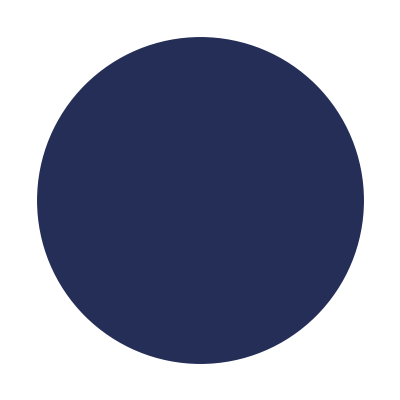
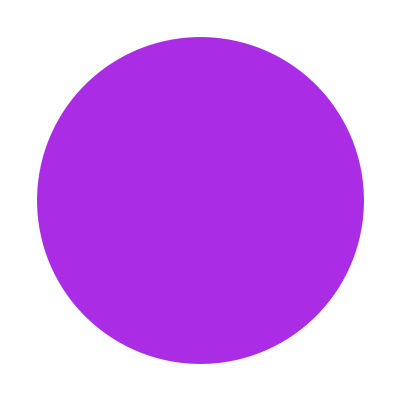
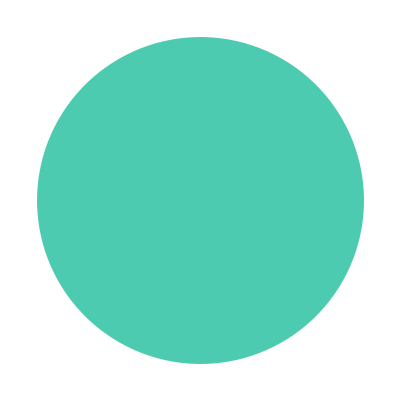
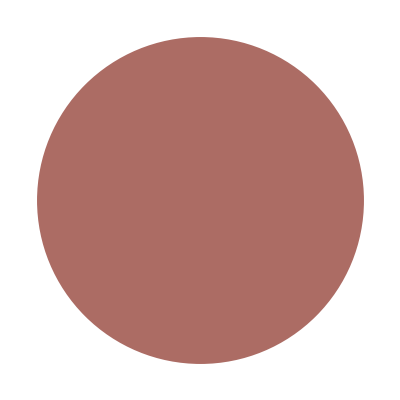
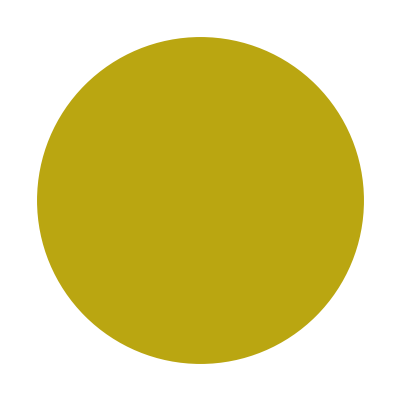
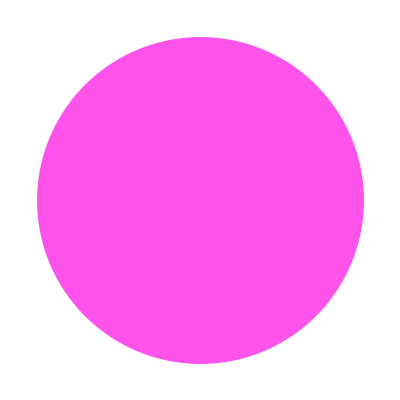
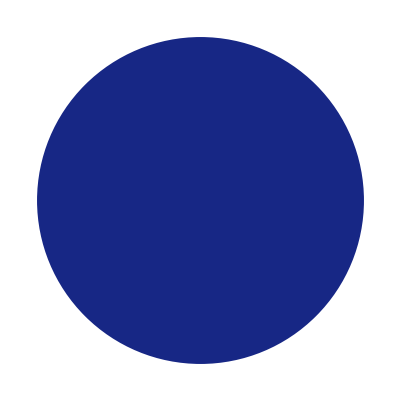
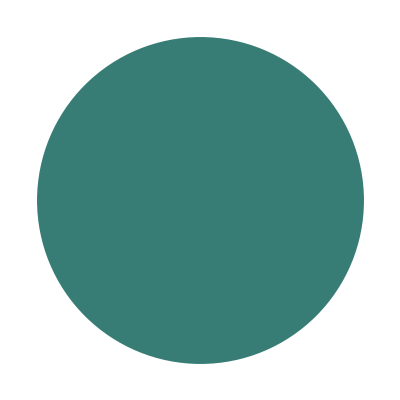

```mathematica
Graphics[{#,Disk[]}]&/@RandomColor[6 3]
```

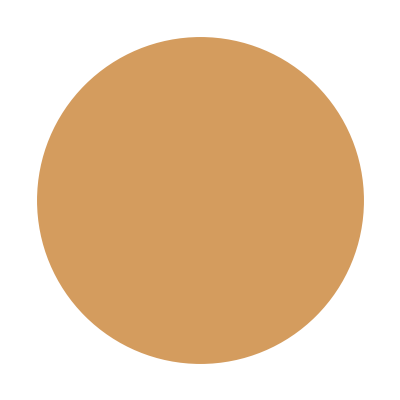
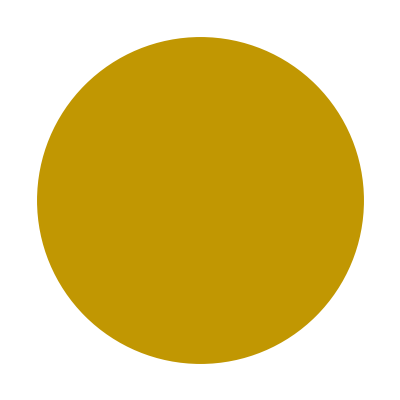
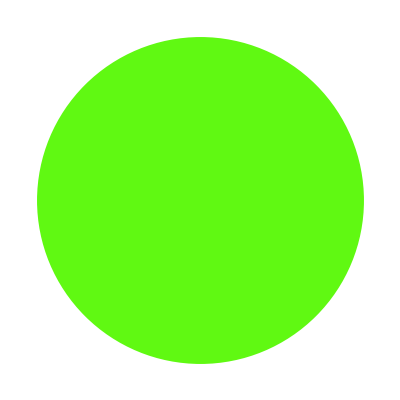
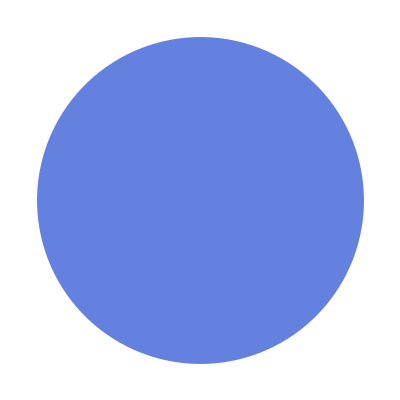
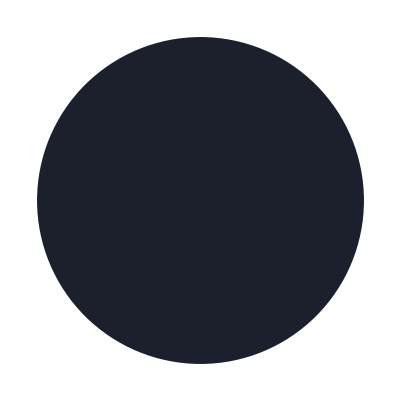
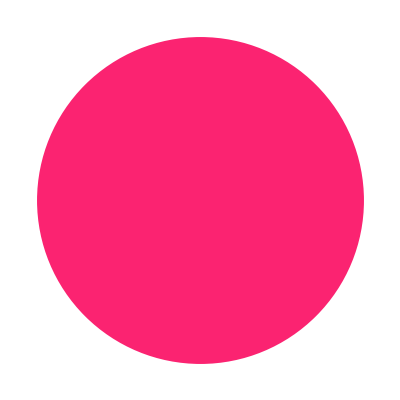
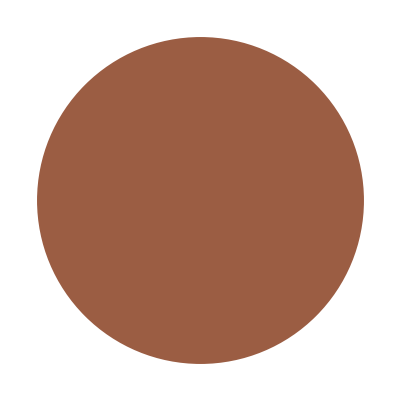
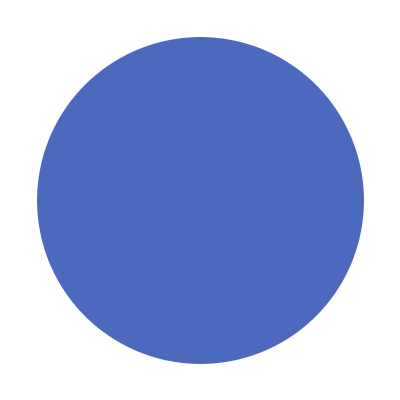
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[Graphics[{#,Disk[]}]&/@RandomColor[6 3]]
```

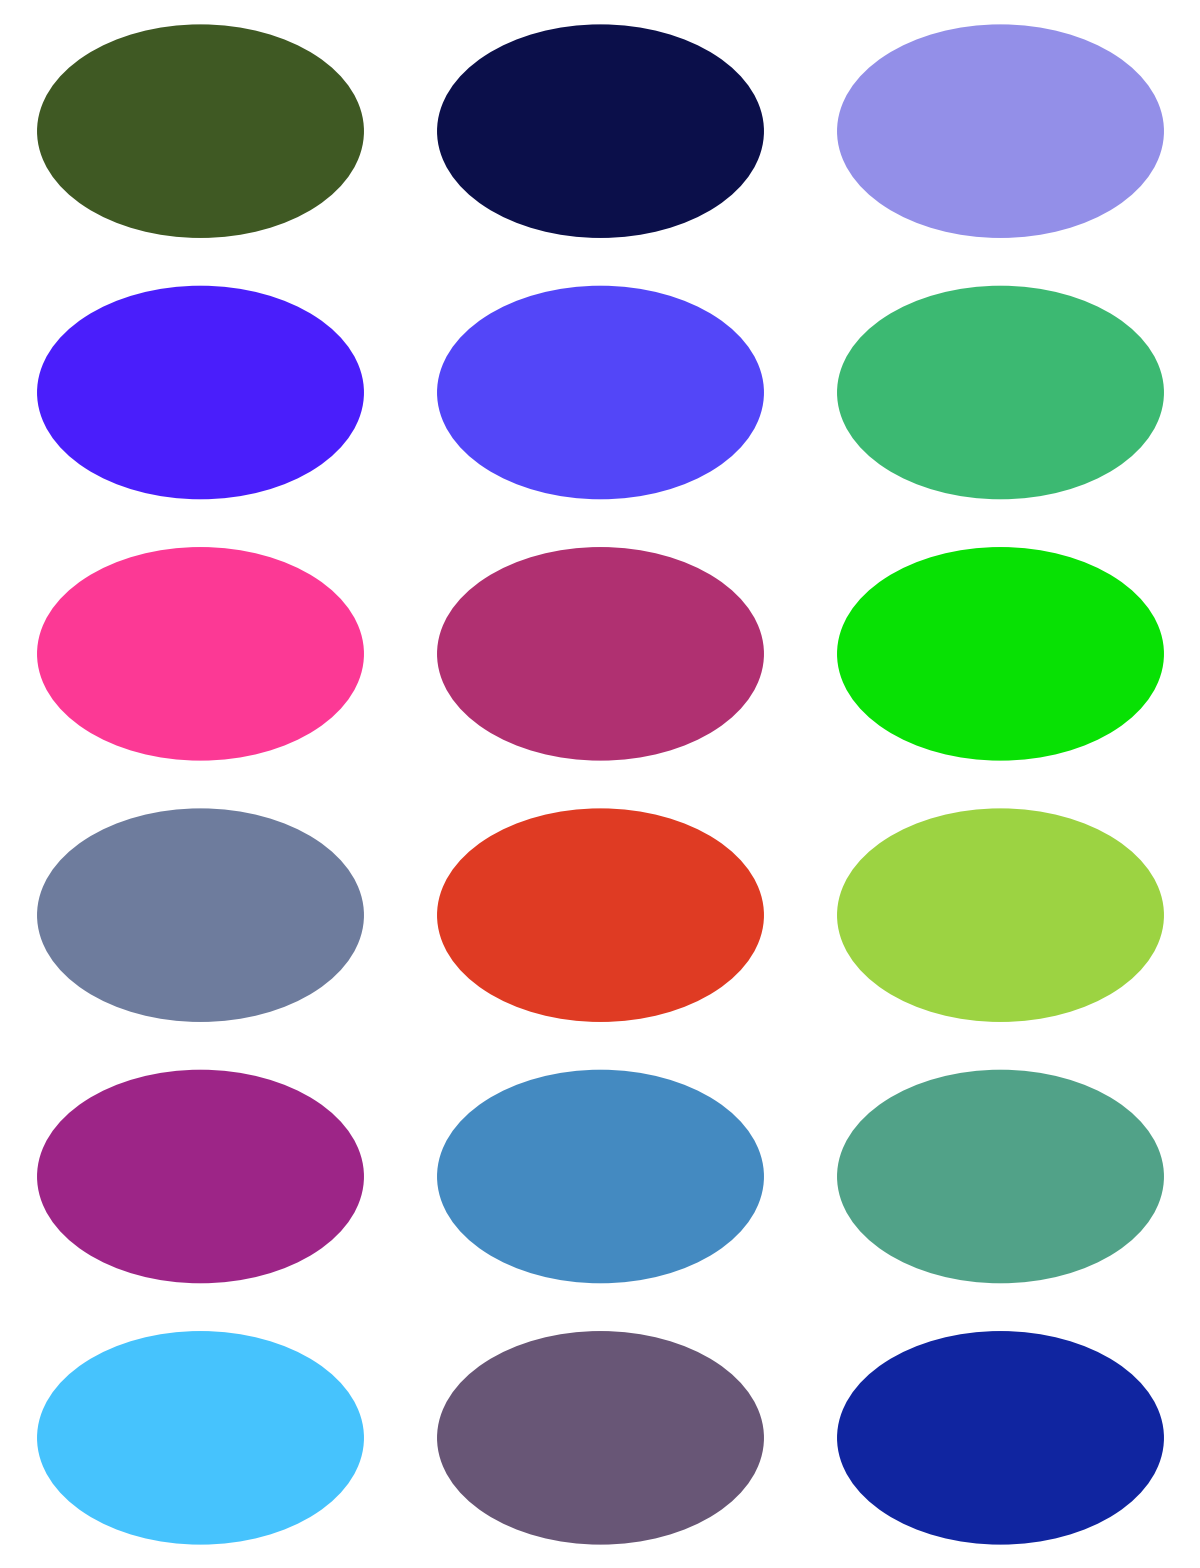

```mathematica
Multicolumn[Graphics[{#,Disk[]}]&/@RandomColor[6 3],{6,3}]
```

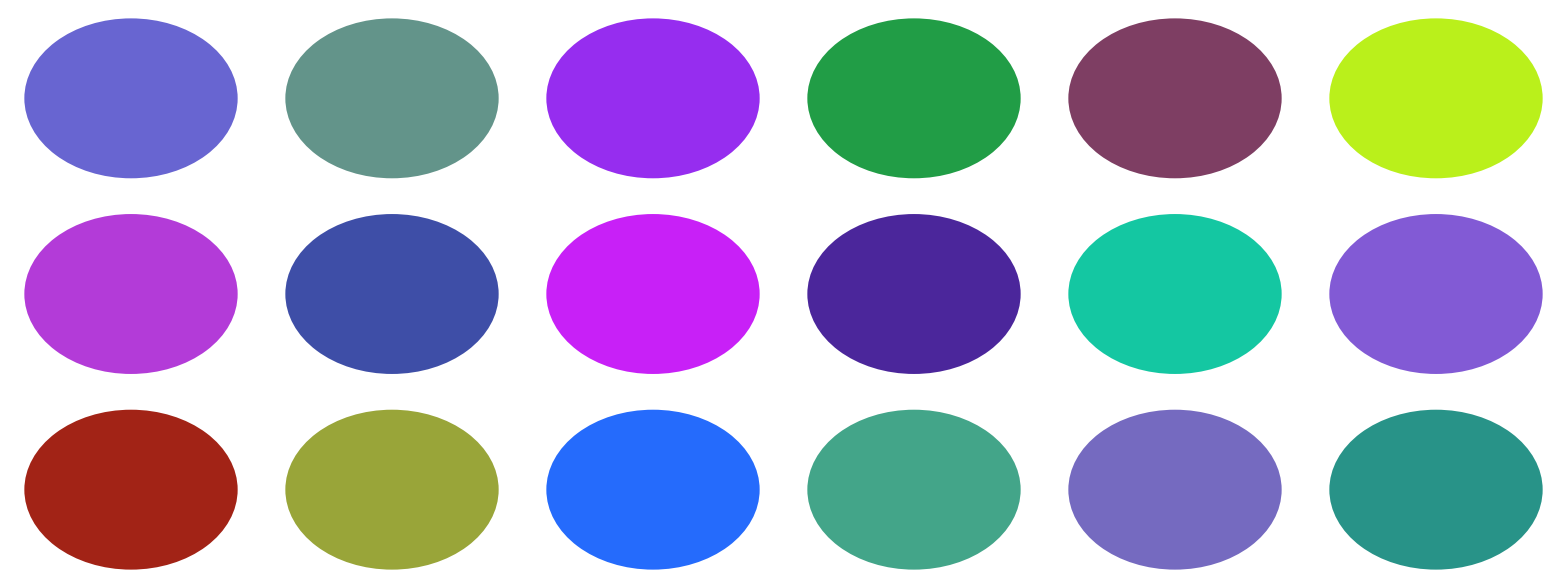

```mathematica
Multicolumn[Graphics[{#,Disk[]}]&/@RandomColor[6 3],{3,6}]
```

Make a 5×5 GraphicsGrid of pie charts that give the relative frequencies of digits in 2^n with n starting at 1

```mathematica
IntegerDigits[2^Range[10]]
```

{{2},{4},{8},{1,6},{3,2},{6,4},{1,2,8},{2,5,6},{5,1,2},{1,0,2,4}}

```mathematica
Counts/@IntegerDigits[2^Range[10]]
```

{<|2→1|>,<|4→1|>,<|8→1|>,<|1→1,6→1|>,<|3→1,2→1|>,<|6→1,4→1|>,<|1→1,2→1,8→1|>,<|2→1,5→1,6→1|>,<|5→1,1→1,2→1|>,<|1→1,0→1,2→1,4→1|>}

```mathematica
PieChart[Counts[#]]&/@IntegerDigits[2^Range[10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PieChart[Counts[#]]&/@IntegerDigits[2^Range[25]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Multicolumn[PieChart[Counts[#]]&/@IntegerDigits[2^Range[25]]]
```

-Graphics-

```mathematica
Multicolumn[PieChart[Counts[#]]&/@IntegerDigits[2^Range[25]],Appearance->"Horizontal"]
```

-Graphics-

Make a graphics row of word clouds for Wikipedia articles on the G5 countries.

```mathematica
WordCloud[WikipediaData[#]]&/@EntityList[EntityClass["Country","GroupOf20"]]
```

$Aborted

Use a pure function with constant arguments:

```mathematica
Map[f[#,3]&,{a,b,c}]
```

{f[a,3],f[b,3],f[c,3]}

### Apply

Display the factorization of an integer using superscripts:

```mathematica
FactorInteger[100!]
```

{{2,97},{3,48},{5,24},{7,16},{11,9},{13,7},{17,5},{19,5},{23,4},{29,3},{31,3},{37,2},{41,2},{43,2},{47,2},{53,1},{59,1},{61,1},{67,1},{71,1},{73,1},{79,1},{83,1},{89,1},{97,1}}

```mathematica
CenterDot@@(Superscript@@@FactorInteger[100!])
```

2^97·3^48·5^24·7^16·11^9·13^7·17^5·19^5·23^4·29^3·31^3·37^2·41^2·43^2·47^2·53^1·59^1·61^1·67^1·71^1·73^1·79^1·83^1·89^1·97^1

Create a table from a list of range specifications:

```mathematica
Table[i^j,##]&@@{{i,3},{j,5}}
```

{{1,1,1,1,1},{2,4,8,16,32},{3,9,27,81,243}}

```mathematica
Table[i^j,##]&@@{{i,10},{j,10}}
```

{{1,1,1,1,1,1,1,1,1,1},{2,4,8,16,32,64,128,256,512,1024},{3,9,27,81,243,729,2187,6561,19683,59049},{4,16,64,256,1024,4096,16384,65536,262144,1048576},{5,25,125,625,3125,15625,78125,390625,1953125,9765625},{6,36,216,1296,7776,46656,279936,1679616,10077696,60466176},{7,49,343,2401,16807,117649,823543,5764801,40353607,282475249},{8,64,512,4096,32768,262144,2097152,16777216,134217728,1073741824},{9,81,729,6561,59049,531441,4782969,43046721,387420489,3486784401},{10,100,1000,10000,100000,1000000,10000000,100000000,1000000000,10000000000}}

```mathematica
Grid[Table[i^j,##]&@@{{i,10},{j,10}}]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024
3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049
4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576
5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625
6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176
7 | 49 | 343 | 2401 | 16807 | 117649 | 823543 | 5764801 | 40353607 | 282475249
8 | 64 | 512 | 4096 | 32768 | 262144 | 2097152 | 16777216 | 134217728 | 1073741824
9 | 81 | 729 | 6561 | 59049 | 531441 | 4782969 | 43046721 | 387420489 | 3486784401
10 | 100 | 1000 | 10000 | 100000 | 1000000 | 10000000 | 100000000 | 1000000000 | 10000000000

```mathematica
TableForm[Table[i^j,##]&@@{{i,20},{j,20}}]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192 | 16384 | 32768 | 65536 | 131072 | 262144 | 524288 | 1048576
3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323 | 4782969 | 14348907 | 43046721 | 129140163 | 387420489 | 1162261467 | 3486784401
4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864 | 268435456 | 1073741824 | 4294967296 | 17179869184 | 68719476736 | 274877906944 | 1099511627776
5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125 | 6103515625 | 30517578125 | 152587890625 | 762939453125 | 3814697265625 | 19073486328125 | 95367431640625
6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016 | 78364164096 | 470184984576 | 2821109907456 | 16926659444736 | 101559956668416 | 609359740010496 | 3656158440062976
7 | 49 | 343 | 2401 | 16807 | 117649 | 823543 | 5764801 | 40353607 | 282475249 | 1977326743 | 13841287201 | 96889010407 | 678223072849 | 4747561509943 | 33232930569601 | 232630513987207 | 1628413597910449 | 11398895185373143 | 79792266297612001
8 | 64 | 512 | 4096 | 32768 | 262144 | 2097152 | 16777216 | 134217728 | 1073741824 | 8589934592 | 68719476736 | 549755813888 | 4398046511104 | 35184372088832 | 281474976710656 | 2251799813685248 | 18014398509481984 | 144115188075855872 | 1152921504606846976
9 | 81 | 729 | 6561 | 59049 | 531441 | 4782969 | 43046721 | 387420489 | 3486784401 | 31381059609 | 282429536481 | 2541865828329 | 22876792454961 | 205891132094649 | 1853020188851841 | 16677181699666569 | 150094635296999121 | 1350851717672992089 | 12157665459056928801
10 | 100 | 1000 | 10000 | 100000 | 1000000 | 10000000 | 100000000 | 1000000000 | 10000000000 | 100000000000 | 1000000000000 | 10000000000000 | 100000000000000 | 1000000000000000 | 10000000000000000 | 100000000000000000 | 1000000000000000000 | 10000000000000000000 | 100000000000000000000
11 | 121 | 1331 | 14641 | 161051 | 1771561 | 19487171 | 214358881 | 2357947691 | 25937424601 | 285311670611 | 3138428376721 | 34522712143931 | 379749833583241 | 4177248169415651 | 45949729863572161 | 505447028499293771 | 5559917313492231481 | 61159090448414546291 | 672749994932560009201
12 | 144 | 1728 | 20736 | 248832 | 2985984 | 35831808 | 429981696 | 5159780352 | 61917364224 | 743008370688 | 8916100448256 | 106993205379072 | 1283918464548864 | 15407021574586368 | 184884258895036416 | 2218611106740436992 | 26623333280885243904 | 319479999370622926848 | 3833759992447475122176
13 | 169 | 2197 | 28561 | 371293 | 4826809 | 62748517 | 815730721 | 10604499373 | 137858491849 | 1792160394037 | 23298085122481 | 302875106592253 | 3937376385699289 | 51185893014090757 | 665416609183179841 | 8650415919381337933 | 112455406951957393129 | 1461920290375446110677 | 19004963774880799438801
14 | 196 | 2744 | 38416 | 537824 | 7529536 | 105413504 | 1475789056 | 20661046784 | 289254654976 | 4049565169664 | 56693912375296 | 793714773254144 | 11112006825558016 | 155568095557812224 | 2177953337809371136 | 30491346729331195904 | 426878854210636742656 | 5976303958948914397184 | 83668255425284801560576
15 | 225 | 3375 | 50625 | 759375 | 11390625 | 170859375 | 2562890625 | 38443359375 | 576650390625 | 8649755859375 | 129746337890625 | 1946195068359375 | 29192926025390625 | 437893890380859375 | 6568408355712890625 | 98526125335693359375 | 1477891880035400390625 | 22168378200531005859375 | 332525673007965087890625
16 | 256 | 4096 | 65536 | 1048576 | 16777216 | 268435456 | 4294967296 | 68719476736 | 1099511627776 | 17592186044416 | 281474976710656 | 4503599627370496 | 72057594037927936 | 1152921504606846976 | 18446744073709551616 | 295147905179352825856 | 4722366482869645213696 | 75557863725914323419136 | 1208925819614629174706176
17 | 289 | 4913 | 83521 | 1419857 | 24137569 | 410338673 | 6975757441 | 118587876497 | 2015993900449 | 34271896307633 | 582622237229761 | 9904578032905937 | 168377826559400929 | 2862423051509815793 | 48661191875666868481 | 827240261886336764177 | 14063084452067724991009 | 239072435685151324847153 | 4064231406647572522401601
18 | 324 | 5832 | 104976 | 1889568 | 34012224 | 612220032 | 11019960576 | 198359290368 | 3570467226624 | 64268410079232 | 1156831381426176 | 20822964865671168 | 374813367582081024 | 6746640616477458432 | 121439531096594251776 | 2185911559738696531968 | 39346408075296537575424 | 708235345355337676357632 | 12748236216396078174437376
19 | 361 | 6859 | 130321 | 2476099 | 47045881 | 893871739 | 16983563041 | 322687697779 | 6131066257801 | 116490258898219 | 2213314919066161 | 42052983462257059 | 799006685782884121 | 15181127029874798299 | 288441413567621167681 | 5480386857784802185939 | 104127350297911241532841 | 1978419655660313589123979 | 37589973457545958193355601
20 | 400 | 8000 | 160000 | 3200000 | 64000000 | 1280000000 | 25600000000 | 512000000000 | 10240000000000 | 204800000000000 | 4096000000000000 | 81920000000000000 | 1638400000000000000 | 32768000000000000000 | 655360000000000000000 | 13107200000000000000000 | 262144000000000000000000 | 5242880000000000000000000 | 104857600000000000000000000

```mathematica
Manipulate[TableForm[Table[i^j,##]&@@{{i,n},{j,n}}],{n,4,20}]
```

Turn a function that takes several arguments into one that takes a list of arguments:

```mathematica
cplus[list_]:=Plus@@list
```

```mathematica
cplus[{a,b,c}]
```

a+b+c

```mathematica
cplus[{a,b,c,d,e,f,g}]
```

a+b+c+d+e+f+g

Find random co-prime integers:

```mathematica
Select[Apply[CoprimeQ]][RandomInteger[10,{20,2}]]
```

{{5,3},{7,6},{9,1},{1,2},{5,9},{9,1}}

```mathematica
?CoprimeQ
```

```mathematica
Select[Apply[CoprimeQ]][RandomInteger[10,{20,3}]]
```

{{1,1,2},{7,4,9},{4,9,5},{7,1,6}}

```mathematica
Select[Apply[CoprimeQ]][RandomInteger[1000,{1000,7}]]
```

{{166,655,857,943,541,557,59},{457,269,785,3,689,593,392},{757,832,237,421,263,527,575},{515,19,593,163,941,479,58},{857,463,547,616,1,705,181},{227,193,542,485,683,513,217}}

Check that the GCD is 1 for every case:

```mathematica
GCD@@@Select[Apply[CoprimeQ]][RandomInteger[1000,{1000,7}]]
```

{1,1,1,1,1,1}

### MapApply

Compute the angles with respect to the positive x axis for a list of ordered pairs:

```mathematica
ArcTan@@@{{1,1},{-1,1},{-1,-1},{1,-1}}
```

{π/4,(3 π)/4,-(3 π)/4,-π/4}

Display the factorization of an integer using superscripts:

```mathematica
FactorInteger[20!]
```

{{2,18},{3,8},{5,4},{7,2},{11,1},{13,1},{17,1},{19,1}}

```mathematica
CenterDot@@MapApply[Superscript,FactorInteger[20!]]
```

2^18·3^8·5^4·7^2·11^1·13^1·17^1·19^1

```mathematica
CenterDot@@Superscript@@@FactorInteger[20!]
```

2^18·3^8·5^4·7^2·11^1·13^1·17^1·19^1

```mathematica
CenterDot@@Superscript@@@FactorInteger[2022!]
```

2^2014·3^1006·5^503·7^334·11^200·13^166·17^124·19^111·23^90·29^71·31^67·37^55·41^50·43^48·47^43·53^38·59^34·61^33·67^30·71^28·73^27·79^25·83^24·89^22·97^20·101^20·103^19·107^18·109^18·113^17·127^15·131^15·137^14·139^14·149^13·151^13·157^12·163^12·167^12·173^11·179^11·181^11·191^10·193^10·197^10·199^10·211^9·223^9·227^8·229^8·233^8·239^8·241^8·251^8·257^7·263^7·269^7·271^7·277^7·281^7·283^7·293^6·307^6·311^6·313^6·317^6·331^6·337^6·347^5·349^5·353^5·359^5·367^5·373^5·379^5·383^5·389^5·397^5·401^5·409^4·419^4·421^4·431^4·433^4·439^4·443^4·449^4·457^4·461^4·463^4·467^4·479^4·487^4·491^4·499^4·503^4·509^3·521^3·523^3·541^3·547^3·557^3·563^3·569^3·571^3·577^3·587^3·593^3·599^3·601^3·607^3·613^3·617^3·619^3·631^3·641^3·643^3·647^3·653^3·659^3·661^3·673^3·677^2·683^2·691^2·701^2·709^2·719^2·727^2·733^2·739^2·743^2·751^2·757^2·761^2·769^2·773^2·787^2·797^2·809^2·811^2·821^2·823^2·827^2·829^2·839^2·853^2·857^2·859^2·863^2·877^2·881^2·883^2·887^2·907^2·911^2·919^2·929^2·937^2·941^2·947^2·953^2·967^2·971^2·977^2·983^2·991^2·997^2·1009^2·1013^1·1019^1·1021^1·1031^1·1033^1·1039^1·1049^1·1051^1·1061^1·1063^1·1069^1·1087^1·1091^1·1093^1·1097^1·1103^1·1109^1·1117^1·1123^1·1129^1·1151^1·1153^1·1163^1·1171^1·1181^1·1187^1·1193^1·1201^1·1213^1·1217^1·1223^1·1229^1·1231^1·1237^1·1249^1·1259^1·1277^1·1279^1·1283^1·1289^1·1291^1·1297^1·1301^1·1303^1·1307^1·1319^1·1321^1·1327^1·1361^1·1367^1·1373^1·1381^1·1399^1·1409^1·1423^1·1427^1·1429^1·1433^1·1439^1·1447^1·1451^1·1453^1·1459^1·1471^1·1481^1·1483^1·1487^1·1489^1·1493^1·1499^1·1511^1·1523^1·1531^1·1543^1·1549^1·1553^1·1559^1·1567^1·1571^1·1579^1·1583^1·1597^1·1601^1·1607^1·1609^1·1613^1·1619^1·1621^1·1627^1·1637^1·1657^1·1663^1·1667^1·1669^1·1693^1·1697^1·1699^1·1709^1·1721^1·1723^1·1733^1·1741^1·1747^1·1753^1·1759^1·1777^1·1783^1·1787^1·1789^1·1801^1·1811^1·1823^1·1831^1·1847^1·1861^1·1867^1·1871^1·1873^1·1877^1·1879^1·1889^1·1901^1·1907^1·1913^1·1931^1·1933^1·1949^1·1951^1·1973^1·1979^1·1987^1·1993^1·1997^1·1999^1·2003^1·2011^1·2017^1

```mathematica
CircleDot@@Superscript@@@FactorInteger[2022!]
```

2^2014⊙3^1006⊙5^503⊙7^334⊙11^200⊙13^166⊙17^124⊙19^111⊙23^90⊙29^71⊙31^67⊙37^55⊙41^50⊙43^48⊙47^43⊙53^38⊙59^34⊙61^33⊙67^30⊙71^28⊙73^27⊙79^25⊙83^24⊙89^22⊙97^20⊙101^20⊙103^19⊙107^18⊙109^18⊙113^17⊙127^15⊙131^15⊙137^14⊙139^14⊙149^13⊙151^13⊙157^12⊙163^12⊙167^12⊙173^11⊙179^11⊙181^11⊙191^10⊙193^10⊙197^10⊙199^10⊙211^9⊙223^9⊙227^8⊙229^8⊙233^8⊙239^8⊙241^8⊙251^8⊙257^7⊙263^7⊙269^7⊙271^7⊙277^7⊙281^7⊙283^7⊙293^6⊙307^6⊙311^6⊙313^6⊙317^6⊙331^6⊙337^6⊙347^5⊙349^5⊙353^5⊙359^5⊙367^5⊙373^5⊙379^5⊙383^5⊙389^5⊙397^5⊙401^5⊙409^4⊙419^4⊙421^4⊙431^4⊙433^4⊙439^4⊙443^4⊙449^4⊙457^4⊙461^4⊙463^4⊙467^4⊙479^4⊙487^4⊙491^4⊙499^4⊙503^4⊙509^3⊙521^3⊙523^3⊙541^3⊙547^3⊙557^3⊙563^3⊙569^3⊙571^3⊙577^3⊙587^3⊙593^3⊙599^3⊙601^3⊙607^3⊙613^3⊙617^3⊙619^3⊙631^3⊙641^3⊙643^3⊙647^3⊙653^3⊙659^3⊙661^3⊙673^3⊙677^2⊙683^2⊙691^2⊙701^2⊙709^2⊙719^2⊙727^2⊙733^2⊙739^2⊙743^2⊙751^2⊙757^2⊙761^2⊙769^2⊙773^2⊙787^2⊙797^2⊙809^2⊙811^2⊙821^2⊙823^2⊙827^2⊙829^2⊙839^2⊙853^2⊙857^2⊙859^2⊙863^2⊙877^2⊙881^2⊙883^2⊙887^2⊙907^2⊙911^2⊙919^2⊙929^2⊙937^2⊙941^2⊙947^2⊙953^2⊙967^2⊙971^2⊙977^2⊙983^2⊙991^2⊙997^2⊙1009^2⊙1013^1⊙1019^1⊙1021^1⊙1031^1⊙1033^1⊙1039^1⊙1049^1⊙1051^1⊙1061^1⊙1063^1⊙1069^1⊙1087^1⊙1091^1⊙1093^1⊙1097^1⊙1103^1⊙1109^1⊙1117^1⊙1123^1⊙1129^1⊙1151^1⊙1153^1⊙1163^1⊙1171^1⊙1181^1⊙1187^1⊙1193^1⊙1201^1⊙1213^1⊙1217^1⊙1223^1⊙1229^1⊙1231^1⊙1237^1⊙1249^1⊙1259^1⊙1277^1⊙1279^1⊙1283^1⊙1289^1⊙1291^1⊙1297^1⊙1301^1⊙1303^1⊙1307^1⊙1319^1⊙1321^1⊙1327^1⊙1361^1⊙1367^1⊙1373^1⊙1381^1⊙1399^1⊙1409^1⊙1423^1⊙1427^1⊙1429^1⊙1433^1⊙1439^1⊙1447^1⊙1451^1⊙1453^1⊙1459^1⊙1471^1⊙1481^1⊙1483^1⊙1487^1⊙1489^1⊙1493^1⊙1499^1⊙1511^1⊙1523^1⊙1531^1⊙1543^1⊙1549^1⊙1553^1⊙1559^1⊙1567^1⊙1571^1⊙1579^1⊙1583^1⊙1597^1⊙1601^1⊙1607^1⊙1609^1⊙1613^1⊙1619^1⊙1621^1⊙1627^1⊙1637^1⊙1657^1⊙1663^1⊙1667^1⊙1669^1⊙1693^1⊙1697^1⊙1699^1⊙1709^1⊙1721^1⊙1723^1⊙1733^1⊙1741^1⊙1747^1⊙1753^1⊙1759^1⊙1777^1⊙1783^1⊙1787^1⊙1789^1⊙1801^1⊙1811^1⊙1823^1⊙1831^1⊙1847^1⊙1861^1⊙1867^1⊙1871^1⊙1873^1⊙1877^1⊙1879^1⊙1889^1⊙1901^1⊙1907^1⊙1913^1⊙1931^1⊙1933^1⊙1949^1⊙1951^1⊙1973^1⊙1979^1⊙1987^1⊙1993^1⊙1997^1⊙1999^1⊙2003^1⊙2011^1⊙2017^1

```mathematica
CirclePlus@@Superscript@@@FactorInteger[2022!]
```

2^2014⊕3^1006⊕5^503⊕7^334⊕11^200⊕13^166⊕17^124⊕19^111⊕23^90⊕29^71⊕31^67⊕37^55⊕41^50⊕43^48⊕47^43⊕53^38⊕59^34⊕61^33⊕67^30⊕71^28⊕73^27⊕79^25⊕83^24⊕89^22⊕97^20⊕101^20⊕103^19⊕107^18⊕109^18⊕113^17⊕127^15⊕131^15⊕137^14⊕139^14⊕149^13⊕151^13⊕157^12⊕163^12⊕167^12⊕173^11⊕179^11⊕181^11⊕191^10⊕193^10⊕197^10⊕199^10⊕211^9⊕223^9⊕227^8⊕229^8⊕233^8⊕239^8⊕241^8⊕251^8⊕257^7⊕263^7⊕269^7⊕271^7⊕277^7⊕281^7⊕283^7⊕293^6⊕307^6⊕311^6⊕313^6⊕317^6⊕331^6⊕337^6⊕347^5⊕349^5⊕353^5⊕359^5⊕367^5⊕373^5⊕379^5⊕383^5⊕389^5⊕397^5⊕401^5⊕409^4⊕419^4⊕421^4⊕431^4⊕433^4⊕439^4⊕443^4⊕449^4⊕457^4⊕461^4⊕463^4⊕467^4⊕479^4⊕487^4⊕491^4⊕499^4⊕503^4⊕509^3⊕521^3⊕523^3⊕541^3⊕547^3⊕557^3⊕563^3⊕569^3⊕571^3⊕577^3⊕587^3⊕593^3⊕599^3⊕601^3⊕607^3⊕613^3⊕617^3⊕619^3⊕631^3⊕641^3⊕643^3⊕647^3⊕653^3⊕659^3⊕661^3⊕673^3⊕677^2⊕683^2⊕691^2⊕701^2⊕709^2⊕719^2⊕727^2⊕733^2⊕739^2⊕743^2⊕751^2⊕757^2⊕761^2⊕769^2⊕773^2⊕787^2⊕797^2⊕809^2⊕811^2⊕821^2⊕823^2⊕827^2⊕829^2⊕839^2⊕853^2⊕857^2⊕859^2⊕863^2⊕877^2⊕881^2⊕883^2⊕887^2⊕907^2⊕911^2⊕919^2⊕929^2⊕937^2⊕941^2⊕947^2⊕953^2⊕967^2⊕971^2⊕977^2⊕983^2⊕991^2⊕997^2⊕1009^2⊕1013^1⊕1019^1⊕1021^1⊕1031^1⊕1033^1⊕1039^1⊕1049^1⊕1051^1⊕1061^1⊕1063^1⊕1069^1⊕1087^1⊕1091^1⊕1093^1⊕1097^1⊕1103^1⊕1109^1⊕1117^1⊕1123^1⊕1129^1⊕1151^1⊕1153^1⊕1163^1⊕1171^1⊕1181^1⊕1187^1⊕1193^1⊕1201^1⊕1213^1⊕1217^1⊕1223^1⊕1229^1⊕1231^1⊕1237^1⊕1249^1⊕1259^1⊕1277^1⊕1279^1⊕1283^1⊕1289^1⊕1291^1⊕1297^1⊕1301^1⊕1303^1⊕1307^1⊕1319^1⊕1321^1⊕1327^1⊕1361^1⊕1367^1⊕1373^1⊕1381^1⊕1399^1⊕1409^1⊕1423^1⊕1427^1⊕1429^1⊕1433^1⊕1439^1⊕1447^1⊕1451^1⊕1453^1⊕1459^1⊕1471^1⊕1481^1⊕1483^1⊕1487^1⊕1489^1⊕1493^1⊕1499^1⊕1511^1⊕1523^1⊕1531^1⊕1543^1⊕1549^1⊕1553^1⊕1559^1⊕1567^1⊕1571^1⊕1579^1⊕1583^1⊕1597^1⊕1601^1⊕1607^1⊕1609^1⊕1613^1⊕1619^1⊕1621^1⊕1627^1⊕1637^1⊕1657^1⊕1663^1⊕1667^1⊕1669^1⊕1693^1⊕1697^1⊕1699^1⊕1709^1⊕1721^1⊕1723^1⊕1733^1⊕1741^1⊕1747^1⊕1753^1⊕1759^1⊕1777^1⊕1783^1⊕1787^1⊕1789^1⊕1801^1⊕1811^1⊕1823^1⊕1831^1⊕1847^1⊕1861^1⊕1867^1⊕1871^1⊕1873^1⊕1877^1⊕1879^1⊕1889^1⊕1901^1⊕1907^1⊕1913^1⊕1931^1⊕1933^1⊕1949^1⊕1951^1⊕1973^1⊕1979^1⊕1987^1⊕1993^1⊕1997^1⊕1999^1⊕2003^1⊕2011^1⊕2017^1

```mathematica
CircleTimes@@Superscript@@@FactorInteger[2022!]
```

2^2014⊗3^1006⊗5^503⊗7^334⊗11^200⊗13^166⊗17^124⊗19^111⊗23^90⊗29^71⊗31^67⊗37^55⊗41^50⊗43^48⊗47^43⊗53^38⊗59^34⊗61^33⊗67^30⊗71^28⊗73^27⊗79^25⊗83^24⊗89^22⊗97^20⊗101^20⊗103^19⊗107^18⊗109^18⊗113^17⊗127^15⊗131^15⊗137^14⊗139^14⊗149^13⊗151^13⊗157^12⊗163^12⊗167^12⊗173^11⊗179^11⊗181^11⊗191^10⊗193^10⊗197^10⊗199^10⊗211^9⊗223^9⊗227^8⊗229^8⊗233^8⊗239^8⊗241^8⊗251^8⊗257^7⊗263^7⊗269^7⊗271^7⊗277^7⊗281^7⊗283^7⊗293^6⊗307^6⊗311^6⊗313^6⊗317^6⊗331^6⊗337^6⊗347^5⊗349^5⊗353^5⊗359^5⊗367^5⊗373^5⊗379^5⊗383^5⊗389^5⊗397^5⊗401^5⊗409^4⊗419^4⊗421^4⊗431^4⊗433^4⊗439^4⊗443^4⊗449^4⊗457^4⊗461^4⊗463^4⊗467^4⊗479^4⊗487^4⊗491^4⊗499^4⊗503^4⊗509^3⊗521^3⊗523^3⊗541^3⊗547^3⊗557^3⊗563^3⊗569^3⊗571^3⊗577^3⊗587^3⊗593^3⊗599^3⊗601^3⊗607^3⊗613^3⊗617^3⊗619^3⊗631^3⊗641^3⊗643^3⊗647^3⊗653^3⊗659^3⊗661^3⊗673^3⊗677^2⊗683^2⊗691^2⊗701^2⊗709^2⊗719^2⊗727^2⊗733^2⊗739^2⊗743^2⊗751^2⊗757^2⊗761^2⊗769^2⊗773^2⊗787^2⊗797^2⊗809^2⊗811^2⊗821^2⊗823^2⊗827^2⊗829^2⊗839^2⊗853^2⊗857^2⊗859^2⊗863^2⊗877^2⊗881^2⊗883^2⊗887^2⊗907^2⊗911^2⊗919^2⊗929^2⊗937^2⊗941^2⊗947^2⊗953^2⊗967^2⊗971^2⊗977^2⊗983^2⊗991^2⊗997^2⊗1009^2⊗1013^1⊗1019^1⊗1021^1⊗1031^1⊗1033^1⊗1039^1⊗1049^1⊗1051^1⊗1061^1⊗1063^1⊗1069^1⊗1087^1⊗1091^1⊗1093^1⊗1097^1⊗1103^1⊗1109^1⊗1117^1⊗1123^1⊗1129^1⊗1151^1⊗1153^1⊗1163^1⊗1171^1⊗1181^1⊗1187^1⊗1193^1⊗1201^1⊗1213^1⊗1217^1⊗1223^1⊗1229^1⊗1231^1⊗1237^1⊗1249^1⊗1259^1⊗1277^1⊗1279^1⊗1283^1⊗1289^1⊗1291^1⊗1297^1⊗1301^1⊗1303^1⊗1307^1⊗1319^1⊗1321^1⊗1327^1⊗1361^1⊗1367^1⊗1373^1⊗1381^1⊗1399^1⊗1409^1⊗1423^1⊗1427^1⊗1429^1⊗1433^1⊗1439^1⊗1447^1⊗1451^1⊗1453^1⊗1459^1⊗1471^1⊗1481^1⊗1483^1⊗1487^1⊗1489^1⊗1493^1⊗1499^1⊗1511^1⊗1523^1⊗1531^1⊗1543^1⊗1549^1⊗1553^1⊗1559^1⊗1567^1⊗1571^1⊗1579^1⊗1583^1⊗1597^1⊗1601^1⊗1607^1⊗1609^1⊗1613^1⊗1619^1⊗1621^1⊗1627^1⊗1637^1⊗1657^1⊗1663^1⊗1667^1⊗1669^1⊗1693^1⊗1697^1⊗1699^1⊗1709^1⊗1721^1⊗1723^1⊗1733^1⊗1741^1⊗1747^1⊗1753^1⊗1759^1⊗1777^1⊗1783^1⊗1787^1⊗1789^1⊗1801^1⊗1811^1⊗1823^1⊗1831^1⊗1847^1⊗1861^1⊗1867^1⊗1871^1⊗1873^1⊗1877^1⊗1879^1⊗1889^1⊗1901^1⊗1907^1⊗1913^1⊗1931^1⊗1933^1⊗1949^1⊗1951^1⊗1973^1⊗1979^1⊗1987^1⊗1993^1⊗1997^1⊗1999^1⊗2003^1⊗2011^1⊗2017^1

### MapIndexed

Label parts by position:

```mathematica
MapIndexed[Labeled,{x^2,x+y,y^2,y^3}]
```

{x^2{1},x+y{2},y^2{3},y^3{4}}

```mathematica
MapIndexed[Framed[Labeled[#1,#2]]&,{x^2,x+y,y^2,y^3},Infinity]
```

{(x{1,1})^(2{1,2}){1},x{2,1}+y{2,2}{2},(y{3,1})^(2{3,2}){3},(y{4,1})^(3{4,2}){4}}

Use tooltips to show part numbers of subexpressions:

```mathematica
MapIndexed[Tooltip,Integrate[1/(x^4-1),x],Infinity]
```

-1/2 ArcTan[x]+-1/4 Log[1+x]+1/4 Log[1+-1 x]

Convert a list to a polynomial:

```mathematica
Total[MapIndexed[#1 x^First[#2]&,{a,b,c,d,e,f}]]
```

a x+b x^2+c x^3+d x^4+e x^5+f x^6

```mathematica
Total[MapIndexed[#1 x^First[#2]&,{a}]]
```

a x

```mathematica
Total[MapIndexed[#1 x^First[#2]&,{a,b}]]
```

a x+b x^2

```mathematica
Total[MapIndexed[#1 x^First[#2]&,{a,b,c}]]
```

a x+b x^2+c x^3

```mathematica
Total[MapIndexed[#1 x^First[#2]&,{a,b,c,d}]]
```

a x+b x^2+c x^3+d x^4

```mathematica
Total[MapIndexed[#1 x^(First[#2]-1)&,{a}]]
```

a

```mathematica
Total[MapIndexed[#1 x^(First[#2]-1)&,{a,b}]]
```

a+b x

```mathematica
Total[MapIndexed[#1 x^(First[#2]-1)&,{a,b,c}]]
```

a+b x+c x^2

```mathematica
Total[MapIndexed[#1 x^(First[#2]-1)&,Reverse[{a,b,c}]]]
```

c+b x+a x^2

Make the standard form of the quadratic equation:

```mathematica
Total[MapIndexed[#1 x^(First[#2]-1)&,Reverse[{a,b,c}]]]
```

c+b x+a x^2

Cubic polynomial:

```mathematica
Total[MapIndexed[#1 x^(First[#2]-1)&,Reverse[{a,b,c,d}]]]
```

d+c x+b x^2+a x^3

Quartic polynomial:

```mathematica
Total[MapIndexed[#1 x^(First[#2]-1)&,Reverse[{a,b,c,d,e}]]]
```

e+d x+c x^2+b x^3+a x^4

Rotate lists based on position:

```mathematica
MapIndexed[RotateLeft,Table[{a,b,c},{6}]]
```

{{b,c,a},{c,a,b},{a,b,c},{b,c,a},{c,a,b},{a,b,c}}

```mathematica
MapIndexed[RotateLeft,Table[{{a,b},{c,d}},{3},{3}],{2}]//MatrixForm
```

((d | c
b | a) | (c | d
a | b) | (d | c
b | a)
(b | a
d | c) | (a | b
c | d) | (b | a
d | c)
(d | c
b | a) | (c | d
a | b) | (d | c
b | a))

Obtain a list of all parts in an expression:

```mathematica
First@Last[Reap[MapIndexed[Sow[#2]&,{{a,b,c},{d},{{e}}},{1,∞}]]]
```

{{1,1},{1,2},{1,3},{1},{2,1},{2},{3,1,1},{3,1},{3}}

```mathematica
Position[{{a,b},{c},{{d}}},_,Infinity,Heads->False]
```

{{1,1},{1,2},{1},{2,1},{2},{3,1,1},{3,1},{3}}

### MapThread

Set up an outer totalistic cellular automaton:

```mathematica
t=RandomInteger[1,10]
```

{1,0,1,0,0,1,0,0,1,1}

```mathematica
MapThread[f,{t,RotateLeft[t]+RotateRight[t]}]
```

{f[1,1],f[0,2],f[1,0],f[0,1],f[0,1],f[1,0],f[0,1],f[0,1],f[1,1],f[1,2]}

Divide eigenvectors by their corresponding eigenvalues:

```mathematica
Eigensystem[{{1,3},{2,7}}]
```

{{4+√15,4-√15},{{1/2 (-3+√15),1},{1/2 (-3-√15),1}}}

```mathematica
MapThread[#2/#1&,Eigensystem[{{1,3},{2,7}}]]//FullSimplify
```

{{1/2 (-27+7 √15),4-√15},{1/2 (-27-7 √15),4+√15}}

Apply the functions in a list to corresponding arguments:

```mathematica
MapThread[#1@#2&,{{f,g,h},{x,y,z}}]
```

{f[x],g[y],h[z]}

### MapAt

Reset an element in a matrix:

```mathematica
MapAt[x&,{{a,b,c},{d,e,f}},{2,1}]
```

{{a,b,c},{x,e,f}}

Reverse the sign of an element in a matrix:

```mathematica
MapAt[-#&,{{a,b,c},{d,e,f}},{2,1}]
```

{{a,b,c},{-d,e,f}}

Enumerate cases mapped with f onto successive elements:

```mathematica
Table[MapAt[f,{a,b,c,d},i],{i,4}]
```

{{f[a],b,c,d},{a,f[b],c,d},{a,b,f[c],d},{a,b,c,f[d]}}

Reverse the color of a cell at a random position in each step:

```mathematica
ArrayPlot[NestList[MapAt[1-#&,#,RandomInteger[{1,30}]]&,Table[0,{30}],20],Mesh->All]
```

-Graphics-

### MapAll

Show nesting structure of an expression:

```mathematica
Integrate[1/(x^3-1),x]
```

-ArcTan[(1+2 x)/(√3)]/(√3)+1/3 Log[1-x]-1/6 Log[1+x+x^2]

```mathematica
Framed//@Integrate[1/(x^3-1),x]
```

-1 ArcTan[3^(-1/2) 1+2 x] 3^(-1/2)+1/3 Log[1+-1 x]+-1/6 Log[1+x+x^2]

### Scan

Make assignments based on data:

```mathematica
Scan[(u[#]=x)&,{55,11,77,88}]
```

```mathematica
{u[76],u[77],u[78]}
```

{u[76],x,u[78]}

Find all leaves in an expression:

```mathematica
Integrate[1/(x^3-1),x]
```

-ArcTan[(1+2 x)/(√3)]/(√3)+1/3 Log[1-x]-1/6 Log[1+x+x^2]

```mathematica
Reap[Scan[Sow,Integrate[1/(x^3-1),x],{-1}]]
```

{Null,{{-1,3,-1/2,3,-1/2,1,2,x,1/3,1,-1,x,-1/6,1,x,x,2}}}

```mathematica
Reap[Scan[Sow,Integrate[1/(x^3-1),x],{-1}]][[2,1]]
```

{-1,3,-1/2,3,-1/2,1,2,x,1/3,1,-1,x,-1/6,1,x,x,2}

### BlockMap

Compute successive differences of elements:

```mathematica
BlockMap[Last[#]-First[#]&,{a,b,c,d,e,f},2,1]
```

{-a+b,-b+c,-c+d,-d+e,-e+f}

Compute a moving average with runs of 3 elements:

```mathematica
BlockMap[Mean,{a,b,c,d,e},3,1]
```

{1/3 (a+b+c),1/3 (b+c+d),1/3 (c+d+e)}

Compute a moving median of a matrix:

```mathematica
BlockMap[Median,{{1,2},{5,3},{1,4},{3,2},{5,5}},2,1]
```

{{3,5/2},{3,7/2},{2,3},{4,7/2}}

Compute a moving quantile for some data:

```mathematica
data=RandomFunction[WienerProcess[],{0,10,0.1}]["Values"];
```

```mathematica
Short[mq=BlockMap[Quantile[#,0.75]&,data,3,1],4]
```

{0.,-0.23093,-0.618466,-0.938533,«91»,-0.14799,0.231844,0.231844,0.231844}

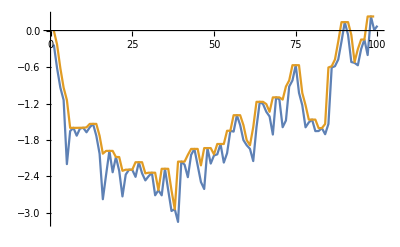

```mathematica
ListLinePlot[{Rest@data,mq}]
```

Smooth a simulated particle trajectory:

```mathematica
n[]:=RandomReal[CauchyDistribution[0,1]]
```

```mathematica
f[]:={u Cos[u]+n[],u Sin[u]+n[]};
```

```mathematica
data=Table[f[],{u,0,6π,1/100}];
```

The underlying signal and simulated path with noise:

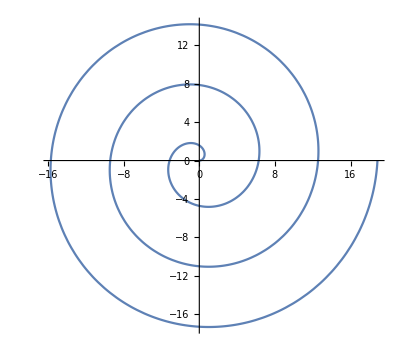
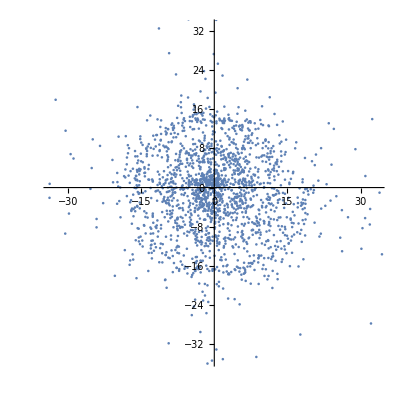

```mathematica
{ParametricPlot[{u Cos[u],u Sin[u]},{u,0,6π}],pd=ListPlot[data,AspectRatio->1]}
```

Smooth the trajectory using a moving TrimmedMean:

```mathematica
smooth[r_]:=BlockMap[TrimmedMean,data,r,1]
```

Increasing the window size gives a smoother trajectory:

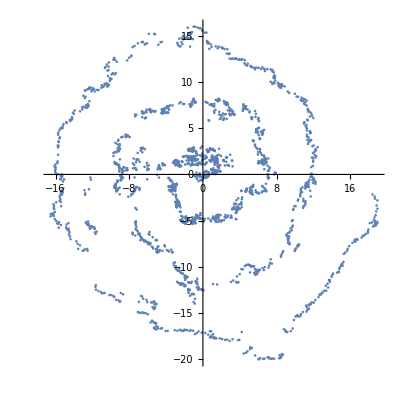
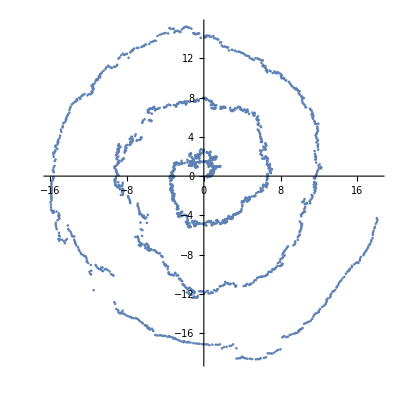
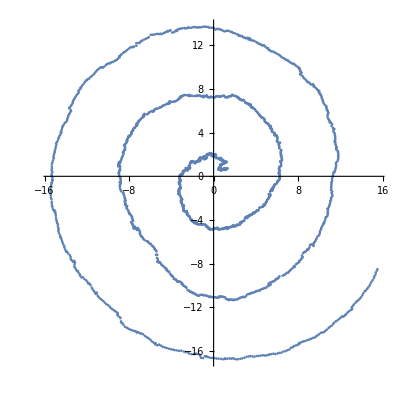
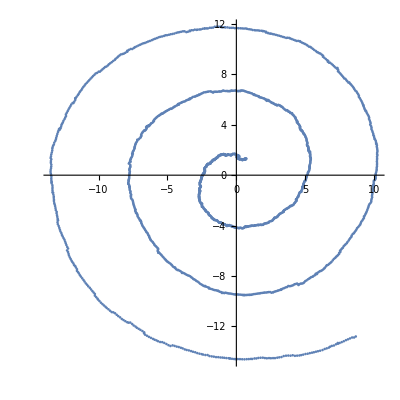

```mathematica
Table[ListPlot[smooth[r],AspectRatio->1],{r,{25,50,100,200}}]
```

### SubsetMap

Implement a sorting network that randomly sorts pairs of elements until all elements are sorted:

```mathematica
randomSort[list_]:=With[{n=Length[list]},NestWhileList[SubsetMap[Sort,#,Sort@RandomInteger[{1,n},2]]&,list,Not@*OrderedQ]]
```

```mathematica
randomSort[Reverse[Range[4]]]
```

{{4,3,2,1},{4,3,1,2},{4,3,1,2},{2,3,1,4},{2,3,1,4},{2,3,1,4},{2,3,1,4},{2,3,1,4},{2,3,1,4},{2,3,1,4},{1,3,2,4},{1,3,2,4},{1,3,2,4},{1,3,2,4},{1,3,2,4},{1,3,2,4},{1,3,2,4},{1,3,2,4},{1,3,2,4},{1,2,3,4}}

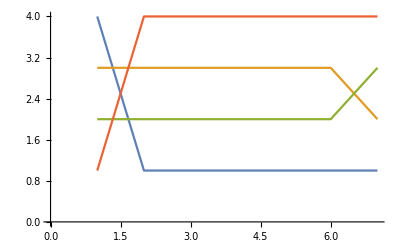

```mathematica
ListLinePlot[Transpose[randomSort[Reverse[Range[4]]]]]
```

For longer lists, finding the last elements to reorder may take many steps:

```mathematica
Length[list=randomSort[Reverse@Range[20]]]
```

679

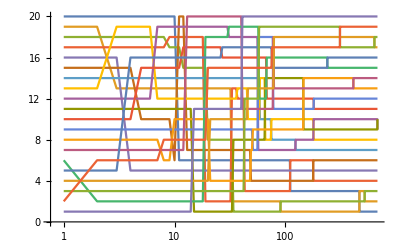

```mathematica
ListLinePlot[Transpose[list],ScalingFunctions->{"Log",None}]
```

## Neat Examples

Show nesting structure of an expression:

```mathematica
Integrate[1/(x^3-1),x]
```

-ArcTan[(1+2 x)/(√3)]/(√3)+1/3 Log[1-x]-1/6 Log[1+x+x^2]

```mathematica
Map[Framed,Integrate[1/(x^3-1),x],Infinity]
```

-1 ArcTan[3^(-1/2) 1+2 x] 3^(-1/2)+1/3 Log[1+-1 x]+-1/6 Log[1+x+x^2]

```mathematica
Map[Framed,Integrate[1/(x^11-1),x],Infinity]
```

-2/11 ArcTan[x+Sin[1/22 π] Sec[1/22 π]] Cos[1/22 π]+-2/11 ArcTan[x+-1 Sin[3/22 π] Sec[3/22 π]] Cos[3/22 π]+-2/11 ArcTan[x+Sin[5/22 π] Sec[5/22 π]] Cos[5/22 π]+1/11 Log[1+-1 x]+-1/11 Cos[1/11 π] Log[1+x^2+2 x Cos[1/11 π]]+1/11 Cos[2/11 π] Log[1+x^2+-2 x Cos[2/11 π]]+-1/11 Log[1+x^2+2 x Sin[1/22 π]] Sin[1/22 π]+-2/11 ArcTan[Csc[1/11 π] x+Cos[1/11 π]] Sin[1/11 π]+1/11 Log[1+x^2+-2 x Sin[3/22 π]] Sin[3/22 π]+-2/11 ArcTan[Csc[2/11 π] x+-1 Cos[2/11 π]] Sin[2/11 π]+-1/11 Log[1+x^2+2 x Sin[5/22 π]] Sin[5/22 π]

```mathematica
Integrate[1/(x^11-1),x]//TraditionalForm
```

-1/11 sin((5 π)/22) log(x^2+2 x sin((5 π)/22)+1)+1/11 sin((3 π)/22) log(x^2-2 x sin((3 π)/22)+1)-1/11 sin(π/22) log(x^2+2 x sin(π/22)+1)-1/11 cos(π/11) log(x^2+2 x cos(π/11)+1)+1/11 cos((2 π)/11) log(x^2-2 x cos((2 π)/11)+1)+1/11 log(1-x)-2/11 sin(π/11) tan^-1(csc(π/11) (x+cos(π/11)))-2/11 sin((2 π)/11) tan^-1(csc((2 π)/11) (x-cos((2 π)/11)))-2/11 cos((5 π)/22) tan^-1(sec((5 π)/22) (x+sin((5 π)/22)))-2/11 cos((3 π)/22) tan^-1(sec((3 π)/22) (x-sin((3 π)/22)))-2/11 cos(π/22) tan^-1(sec(π/22) (x+sin(π/22)))

## Iteratively Applying Functions

## Basic Examples

XXXX:

### Nest

```mathematica
Nest[f,x,3]
```

f[f[f[x]]]

```mathematica
Nest[f,x,9]
```

f[f[f[f[f[f[f[f[f[x]]]]]]]]]

The function to nest can be a pure function:

```mathematica
Nest[(1+#)^2&,1,3]
```

676

```mathematica
Nest[(1+#)^2&,x,3]
```

(1+(1+(1+x)^2)^2)^2

```mathematica
Expand[Nest[(1+#)^2&,x,3]]
```

25+80 x+144 x^2+168 x^3+138 x^4+80 x^5+32 x^6+8 x^7+x^8

### NestList

```mathematica
NestList[f,x,4]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]]}

```mathematica
NestList[Cos,1.0,10]
```

{1.,0.540302,0.857553,0.65429,0.79348,0.701369,0.76396,0.722102,0.750418,0.731404,0.744237}

The function to nest can be a pure function:

```mathematica
NestList[(1+#)^2&,x,3]
```

{x,(1+x)^2,(1+(1+x)^2)^2,(1+(1+(1+x)^2)^2)^2}

### NestGraph

Construct a graph by starting with x and applying f successively 7 times:

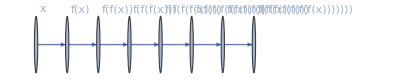

```mathematica
NestGraph[f,x,7,VertexLabels->Automatic,ImageSize->Full]
```

The function to nest can be a pure function:

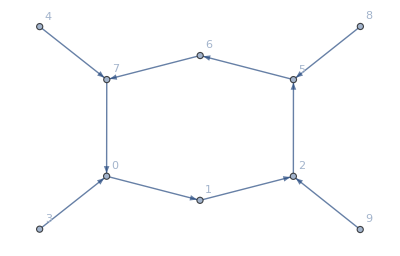

```mathematica
NestGraph[Mod[#^2+1,10]&,Range[0,9],VertexLabels->Automatic]
```

Create a binary tree of nested functions:

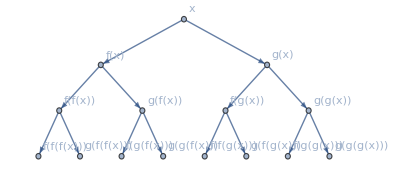

```mathematica
NestGraph[{f[#],g[#]}&,x,3,VertexLabels->Automatic,ImageSize->Full]
```

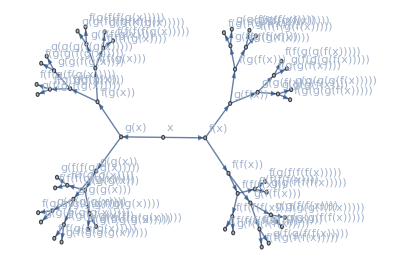

```mathematica
NestGraph[{f[#],g[#]}&,x,5,VertexLabels->Automatic,ImageSize->Full]
```

Generate a graph of neighboring countries around Switzerland:

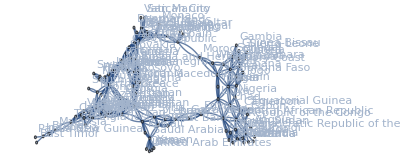

```mathematica
NestGraph[#["BorderingCountries"]&,Entity["Country","Switzerland"],9,VertexLabels->Automatic,DirectedEdges->False]
```

### Fold

Successively apply a function f to a seed x and the elements of a list:

```mathematica
Fold[f,x,{a,b,c}]
```

f[f[f[x,a],b],c]

Use Fold with List to create nested ordered pairs:

```mathematica
Fold[List,x,{a,b,c}]
```

{{{x,a},b},c}

Multiply elements one element at a time:

```mathematica
Fold[Times,1,{a,b,c}]
```

a b c

Start from the first element of the list:

```mathematica
Fold[f,{a,b,c}]
```

f[f[a,b],c]

### FoldList

### SequenceFold

### SequenceFoldList

### FoldPair

### FoldPairList

### FoldWhile

### FoldWhileList

### FixedPoint

### FixedPointList

### NestWhile

### NestWhileList

### TakeWhile

### LengthWhile

## Applications

XXXX:

### Nest

Continued fraction:

```mathematica
Nest[1/(1+#)&,x,5]
```

1/(1+1/(1+1/(1+1/(1+1/(1+x)))))

```mathematica
Nest[1/(1+#)&,x,20]
```

1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x))))))))))))))))))))

Power tower:

```mathematica
Nest[x^#&,x,7]
```

x^(x^(x^(x^(x^(x^(x^x))))))

Growth of annually compounded capital in 10 years:

```mathematica
Nest[#(1+0.05)&,1000,10]
```

1628.89

Newton iterations for √2:

```mathematica
Nest[(#+2/#)/2&,1.0,5]
```

1.41421

```mathematica
Nest[(#+2/#)/2&,1.0`100,100]
```

1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327641573

```mathematica
N[√2,100]
```

1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327641573

Iterated string replacements:

```mathematica
Nest[StringReplace[#,{"A"->"BA","B"->"AB"}]&,"A",5]
```

BAABABBAABBABAABABBABAABBAABABBA

Consecutive pairs of Fibonacci numbers:

```mathematica
Nest[{{1,1},{1,0}}.#&,{0,1},10]
```

{55,34}

Functional composition for higher-order Newton iteration for √3:

```mathematica
Function[x,Evaluate[Together[Nest[Function[z,(z+3/z)/2],x,4]]]]
```

Function[x,(6561+262440 x^2+1326780 x^4+1945944 x^6+1042470 x^8+216216 x^10+16380 x^12+360 x^14+x^16)/(16 x (3+x^2) (9+18 x^2+x^4) (81+756 x^2+630 x^4+84 x^6+x^8))]

```mathematica
FixedPointList[Function[x,Evaluate[Together[Nest[Function[z,(z+3/z)/2],x,4]]]],1`50]
```

{1.,1.73205081001472754050073637702503681885125184094,1.7320508075688772935274463415058723669428052538,1.732050807568877293527446341505872366942805254}

Generate a bifurcation diagram for an iterated logistic map:

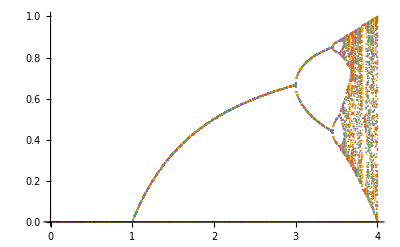

```mathematica
ListPlot[Table[Thread[{r,Nest[r #(1-#)&,Range[0,1,0.01],1000]}],{r,0,4,0.01}]]
```

### NestList

Powers of 2:

```mathematica
NestList[2#1&,1,10]
```

{1,2,4,8,16,32,64,128,256,512,1024}

Successive integers:

```mathematica
NestList[#+1&,0,10]
```

{0,1,2,3,4,5,6,7,8,9,10}

Successive squaring:

```mathematica
NestList[#^2&,2,6]
```

{2,4,16,256,65536,4294967296,18446744073709551616}

Growth of annually compounded capital:

```mathematica
NestList[#(1+0.05)&,1000,10]
```

{1000,1050.,1102.5,1157.63,1215.51,1276.28,1340.1,1407.1,1477.46,1551.33,1628.89}

Successive derivatives:

```mathematica
NestList[D[#,x]&,x^n,3]
```

{x^n,n x^(-1+n),(-1+n) n x^(-2+n),(-2+n) (-1+n) n x^(-3+n)}

```mathematica
NestList[ExpandAll@D[#,x]&,x^n,3]
```

{x^n,n x^(-1+n),-n x^(-2+n)+n^2 x^(-2+n),2 n x^(-3+n)-3 n^2 x^(-3+n)+n^3 x^(-3+n)}

Newton iterations for √2:

```mathematica
NestList[(#+2/#)/2&,1.0,5]
```

{1.,1.5,1.41667,1.41422,1.41421,1.41421}

Continued fraction:

```mathematica
NestList[1/(1+#)&,x,5]
```

{x,1/(1+x),1/(1+1/(1+x)),1/(1+1/(1+1/(1+x))),1/(1+1/(1+1/(1+1/(1+x)))),1/(1+1/(1+1/(1+1/(1+1/(1+x)))))}

Iterated map:

```mathematica
NestList[4# (1-#)&,1/3,5]
```

{1/3,8/9,32/81,6272/6561,7250432/43046721,1038154236987392/1853020188851841}

```mathematica
NestList[4# (1-#)&,N[1/3],5]
```

{0.333333,0.888889,0.395062,0.955952,0.168432,0.56025}

Iterates in the 3n+1 problem:

```mathematica
NestList[If[EvenQ[#],#/2,(3#+1)/2]&,100,20]
```

{100,50,25,38,19,29,44,22,11,17,26,13,20,10,5,8,4,2,1,2,1}

Linear congruential pseudorandom generator:

```mathematica
NestList[Mod[59#,101]&,1,15]
```

{1,59,47,46,88,41,96,8,68,73,65,98,25,61,64,39}

Random walk:

```mathematica
NestList[#+RandomChoice[{-1,1}]&,0,20]
```

{0,1,0,1,2,3,2,1,2,1,2,3,2,3,2,1,0,-1,-2,-1,0}

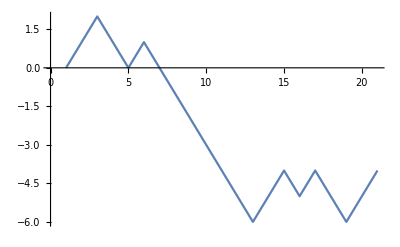

```mathematica
ListLinePlot[NestList[#+RandomChoice[{-1,1}]&,0,20]]
```

Iterated string replacements:

```mathematica
NestList[StringReplace[#,{"A"->"BA","B"->"AB"}]&,"A",5]
```

{A,BA,ABBA,BAABABBA,ABBABAABBAABABBA,BAABABBAABBABAABABBABAABBAABABBA}

Successively append to a list:

```mathematica
NestList[Append[#,x]&,{a},5]
```

{{a},{a,x},{a,x,x},{a,x,x,x},{a,x,x,x,x},{a,x,x,x,x,x}}

Successively rotate a list:

```mathematica
NestList[RotateLeft,{a,b,c,d},4]
```

{{a,b,c,d},{b,c,d,a},{c,d,a,b},{d,a,b,c},{a,b,c,d}}

```mathematica
NestList[RotateRight,{a,b,c,d},4]
```

{{a,b,c,d},{d,a,b,c},{c,d,a,b},{b,c,d,a},{a,b,c,d}}

### NestGraph

Generate a network of "nearby" functions in the Wolfram language:

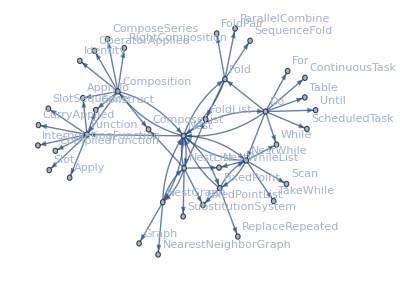

```mathematica
NestGraph[WolframLanguageData[#,EntityProperty["WolframLanguageSymbol","RelatedSymbols"]]&,Entity["WolframLanguageSymbol","Nest"],2,VertexLabels->"Name"]
```

Visualize file systems:

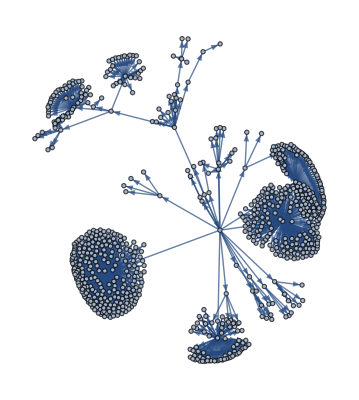

```mathematica
NestGraph[FileNames["*",#]&,$InstallationDirectory,3,VertexLabels->Placed["Name",Tooltip]]
```

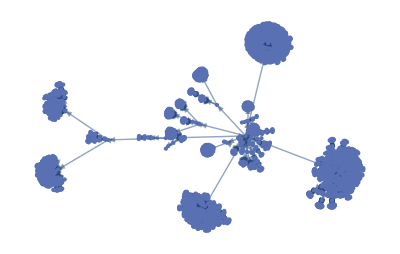

```mathematica
NestGraph[FileNames["*",#]&,$InstallationDirectory,4,VertexLabels->Placed["Name",Tooltip],ImageSize->Full]
```

### Fold

Create a nested polynomial (Horner form):

```mathematica
Fold[x #1+#2&,0,{a,b,c,d,e,f,g}]
```

g+x (f+x (e+x (d+x (c+x (b+a x)))))

HornerForm directly produces this output:

```mathematica
HornerForm[Reverse[{a,b,c,d,e,f,g}].x^Range[0,6],x]
```

g+x (f+x (e+x (d+x (c+x (b+a x)))))

Form a continued fraction:

```mathematica
Fold[1/(#2+#1)&,x,Reverse[{a,b,c}]]
```

1/(a+1/(b+1/(c+x)))

```mathematica
Fold[1/(#2+#1)&,x,Reverse[{a,b,c,d,e,f,g}]]
```

1/(a+1/(b+1/(c+1/(d+1/(e+1/(f+1/(g+x)))))))

Form a number from digits:

```mathematica
Fold[10#1+#2&,0,{4,5,1,6,7,8}]
```

451678

Form an alternating sum:

```mathematica
Fold[#2-#1&,0,Reverse[{a,b,c,d,e}]]
```

a-b+c-d+e

Form a binary tree:

```mathematica
Fold[{#2,#1}&,x,{a,b,c,d}]
```

{d,{c,{b,{a,x}}}}

```mathematica
ExpressionTree[Fold[{#2,#1}&,x,{a,b,c,d}]]
```

-Graphics-

Form a function composition:

```mathematica
Fold[#2[#1]&,x,{a,b,c,d}]
```

d[c[b[a[x]]]]

Apply an indexed sequence of functions:

```mathematica
Fold[{f[#,#],g[#]}[[#2]]&,e,{1,1,2,1,2}]
```

g[f[g[f[f[e,e],f[e,e]]],g[f[f[e,e],f[e,e]]]]]

Successively partition a list:

```mathematica
Fold[Partition,Range[30],{2,4,3}]
```

{{{{1,2},{3,4},{5,6},{7,8}},{{9,10},{11,12},{13,14},{15,16}},{{17,18},{19,20},{21,22},{23,24}}}}

```mathematica
Dimensions[Fold[Partition,Range[30],{2,4,3}]]
```

{1,3,4,2}

### FoldList

### SequenceFold

### SequenceFoldList

### FoldPair

### FoldPairList

### FoldWhile

### FoldWhileList

### FixedPoint

### FixedPointList

### NestWhile

### NestWhileList

### TakeWhile

### LengthWhile

## Neat Examples

XXXX:

### Nest

```mathematica
Nest[Framed,x,7]
```

x

Binary tree:

```mathematica
Nest[{#,#}&,x,3]
```

{{{x,x},{x,x}},{{x,x},{x,x}}}

```mathematica
Nest[Framed[Row[{#,#}]]&,"",5]
```

```mathematica
Nest[p[#][#]&,x,4]
```

p[p[p[p[x][x]][p[x][x]]][p[p[x][x]][p[x][x]]]][p[p[p[x][x]][p[x][x]]][p[p[x][x]][p[x][x]]]]

```mathematica
Nest[Subsuperscript[#,#,#]&,x,5]
```

((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))_((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))^((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))

Gray codes of length 4:

```mathematica
Nest[Join[#,Length[#]+Reverse[#]]&,{0},4]
```

{0,1,3,2,6,7,5,4,12,13,15,14,10,11,9,8}

```mathematica
BaseForm[Nest[Join[#,Length[#]+Reverse[#]]&,{0},4],2]
```

{0_2,1_2,11_2,10_2,110_2,111_2,101_2,100_2,1100_2,1101_2,1111_2,1110_2,1010_2,1011_2,1001_2,1000_2}

### NestList

Text effects:

```mathematica
NestList[Framed,x,7]
```

{x,x,x,x,x,x,x,x}

```mathematica
NestList[Style[#,Larger]&,x,7]
```

{x,x,x,x,x,x,x,x}

Power towers:

```mathematica
NestList[x^#&,x,7]
```

{x,x^x,x^(x^x),x^(x^(x^x)),x^(x^(x^(x^x))),x^(x^(x^(x^(x^x)))),x^(x^(x^(x^(x^(x^x))))),x^(x^(x^(x^(x^(x^(x^x))))))}

```mathematica
NestList[#^#&,x,4]
```

{x,x^x,(x^x)^(x^x),((x^x)^(x^x))^((x^x)^(x^x)),(((x^x)^(x^x))^((x^x)^(x^x)))^(((x^x)^(x^x))^((x^x)^(x^x)))}

Argument doubling:

```mathematica
NestList[Framed[Row[{#,#}]]&,x,4]
```

{x,xx,xxxx,xxxxxxxx,xxxxxxxxxxxxxxxx}

```mathematica
NestList[p[#][#]&,x,3]
```

{x,p[x][x],p[p[x][x]][p[x][x]],p[p[p[x][x]][p[x][x]]][p[p[x][x]][p[x][x]]]}

Sierpiński text:

```mathematica
NestList[Subsuperscript[#,#,#]&,x,7]
```

{x,x_x^x,(x_x^x)_(x_x^x)^(x_x^x),((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)),(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))),((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))_((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))^((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))),(((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))_((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))^((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))))_(((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))_((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))^((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))))^(((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))_((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))^((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))),((((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))_((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))^((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))))_(((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))_((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))^((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))))^(((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))_((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))^((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))))_((((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))_((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))^((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))))_(((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))_((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))^((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))))^(((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))_((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))^((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))))^((((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))_((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))^((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))))_(((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))_((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))^((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))))^(((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))_((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))^((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))))}

### NestGraph

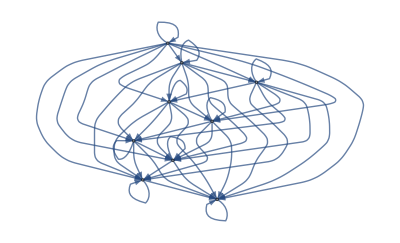

```mathematica
NestGraph[Range,{9},5]
```

### Fold

An explicit form of the primitive recursive function r[z,r[s,r[s,r[s,p[2]]]]]:

```mathematica
Array[Fold[Fold[2^Ceiling[Log[2,Ceiling[(#1+2)/(#2+2)]]](#2+2)-2-#1&,#2,Range[#1]]&,0,Range[#]]&,100]
```

{1,2,1,0,5,2,3,3,2,2,3,4,1,8,5,4,2,2,3,3,2,2,7,2,9,5,2,12,9,7,5,4,2,2,3,4,1,8,5,4,2,2,3,3,2,2,15,8,5,1,43,20,13,10,3,14,7,3,11,8,3,8,5,4,2,2,3,4,1,24,13,5,4,2,11,4,5,5,4,1,13,6,5,5,4,2,7,5,3,1,3,3,2,2,31,14,10,3,3,2}

Generate all subsets of a set:

```mathematica
Fold[Function[{s,e},Join[s,Append[#,e]&/@s]],{{}},{a,b,c}]
```

{{},{a},{b},{a,b},{c},{a,c},{b,c},{a,b,c}}

Find all possible sums of any of the elements of a list of numbers:

```mathematica
Fold[Union[#1,#1+#2]&,{0},{1,2,2,8}]
```

{0,1,2,3,4,5,8,9,10,11,12,13}

The fourth Swinnerton-Dyer polynomial:

```mathematica
Fold[Expand[(#1/.x->x+#2)(#1/.x->x-#2)]&,x,Sqrt[Prime[Range[4]]]]
```

46225-5596840 x^2+13950764 x^4-7453176 x^6+1513334 x^8-141912 x^10+6476 x^12-136 x^14+x^16

```mathematica
Fold[Expand[(#1/.x->x+#2)(#1/.x->x-#2)]&,x,Sqrt[Prime[Range[5]]]]
```

2000989041197056-44660812492570624 x^2+183876928237731840 x^4-255690851718529024 x^6+172580952324702208 x^8-65892492886671360 x^10+15459151516270592 x^12-2349014746136576 x^14+239210760462336 x^16-16665641517056 x^18+801918722048 x^20-26625650688 x^22+602397952 x^24-9028096 x^26+84864 x^28-448 x^30+x^32

```mathematica
Fold[Expand[(#1/.x->x+#2)(#1/.x->x-#2)]&,x,Sqrt[Prime[Range[10]]]]//AbsoluteTiming
```

{1.09155,435674500151429552033580649774189976987857299371616614314771969496916262908188381873136311175130150614817306293260335979363125662910934466774413044140006317929245283364806885699104133657167622402816511193429406570687469532954743393847953934758415746514765637827333796443784728519442615538247848091209265184549301263908052638305534959247423159286804423120836628427053683260660894653042827863797261812856379945889754260958984211716421106758775793642793378411796879805783756984234297797880509006504135482460138715176453610735650939769402336808201247068224935535303736279149031837547427183579629017430057770414933542218227865898500877229542639411260415944877078244362579634264220976459810020826273664290944298841935340864934697113749089910657885737866287217484390606009683251216844993678032617406904697418212890625-1668630662372534578165219948454740423263432210156757446288509300894477535560042553527388507978615740978985964469741022165027121080717177828101385724643039177121639219009210233961617511011967286190067918239558642208805803649565747254431562726732993641769678471506044462088261078528698922189975440860726060690786610652901779004017080366158427376062942045168643214696862963477999344834079820837936023777536789516090379231101463389087054038775235372950631154344347253813341090708495763539672765693654048638173839616261490454712926143866733834385772912040416336530488029628331475401754141649060518626042082835996785159823204526104115068138549813885352069456014581673764692994736275626893712903560990894703228883217317435365492311278347336917761423385114245231569024003298932346440302990948287664121563720703125000000000 x^2+2067719862872061860019516153157994758832954828953975635679658874571303819781891134956617013123210035520036241446851796820520490051186820764201733966232407670629412559419599541986406260418012729915306114315522329143274867916370828977253114482933984004293907376384185691517548934554473760406701054287191906299471667323262707464531818006791782154263396496762943189800065036150636588554819726251560463589140746104686783155585596101227909967000731188458005836588125930377566909491376893874124674222853848451165295141741868263885239164238025784429747152992462252428506437809247166392336010092616994183098666913252990204255505489677520734101425716796403091619902676838153096040654820129037054709541235739737573426115870271617552562424864218739360009003645524627398658507153964970751899623819925523584819013061523437500000000 x^4-975733990189353672370619023365765586940271521118362567187929863474760425076311553820413589940017833783735920126867100612219369411275375177856359495176408417484023875242712804035053541436724681580905647535235911076580106106548831510680684378767939268654720146182730227351031841629790827020257577078177272746178141787158397047794457014263162369759403528448988419412486851094665755421717071981423013607403446151253984493445574783183618650751196136926086225743056600570852046835253896040902378272325778856307355974287624364661336871383178183291655995437404743530851913484600273647466494683508948036836503306982119616481888836289679325553558064721314767134408607471696375735677740066721105675725625862084852413677931647375162708834035742388642104827217541811771151366282540455341080202430711331326447341886474609375000000000 x^6+228638558581718490552374120477525561485327076535854349597719076669167149860038773500391206639559913814289237364038541040588529111712517161918530950430296161570132428304665764937287277506349693114056144032643552555469474914011345100501238615021198236714083284225303979023787909528374666909670804866830037991477673250705129794596207970696346919560448933287889540630537018966989855652895871750853797660549947092816464739880395530457260794975756505076975533689317593872307546405020043663088497059773616164860544283055668297027061993018562971134396597946299417033709304776598261780479981259989239333921141887179935810054777683283247882797130190815563236976442943738885315674298302568500468362809309028894171800350498576535092246573166811518418835816282341346721317515736208032805211011425645162045555197755003503417968750000000 x^8-31431248216203818531922017384682116762481536576994622218603941200636823701199232485431971229953310576108981384505774813309112520052296914101211558916734201021437845987579211628035681545809608240120163943182538061742712087555084069577935132130707924750210929664757071408194005413008405391173593578511474567925169684494089089835852549026440543152931486034032182506996359797748345476321465266356547377482855248577067600750404486345558198757436977459706553701854475764999506283483383946432966521583066474245863683414669581463790411060317085171154010020281886028195202423087706105530923020549549968855980309960450970028175127615621099098172909637992375669394284371318612343132297667120145918711870485654208117046630233104988244341273968871879461942454869911146373970333708323302177831381794824006419231724696566962890625000000000 x^10+2840730250178029129682245173518965995771282437147023034195199353131819492271677901327621212439944238263052183108784327723685852803078600662175554419106567752685748134837894984113910584063565784675892067377468930221778995783008112300624279241099842903131255394613763866476015593032775179318705572942776976642042661281733300807425460979946375947190165364613844361145538252588475249027778819006924973873792980588840741084269024965321969210592660486439053593159592158691225225364752244776706414927163715695628750830865780434625603569317335542104620840013309576538386299217762620528675127740331575269299029629966250859491355480810631625271665192333684795103892725711027957657864493201926380394597249603345051307665062493357629832351845247268978647811105115165885753063886966635169037558900880166347696488917162996036132812500000000 x^12-182160891421652601173790755155566130640752211708715105570691723456100697014933688041938079132106995844600133412348333359935220332592553272599221525382241193654738618712950225148640666925763705584843816147080017416682350255332708140552292524264677760935683516934126108950852202788497279687044063596887209085576572906864221050705375845333603392472788436633355630970156830278056838302583231157398376414522337317269348443343051318096258903561776128949230350465889531139396810525083799933627920908466081836244590037825296021461896804203634380069830736485260148988447437020838133929856384750610543835930049183141546057850819453249908077928514550487799786692520805660062942971992446077254431208243535555399664215792167146842720475655489462565208771867092753354754636157532963912578815432683760727153343291260543069951041796875000000000 x^14+8738885594365711114194526362633476268042299589842724022498318571941894226104348095883574591597197506566663335457350384091439071129691370181976159771365185119092925979518436534812808489548814194920342459755750244638468482073118690017837621849622693918334035837471172057517874355168035874727602887288141161293543953724124615765575421665256540156501328591981085016537246877226115875475621282584555070270472390580500142032885081625608085374623762562720113336970214618080677018915325466844951298524742960443578643480659330617352849762963693648936245037606146690599515044906216681527602724770385290646527139111019769928135937238690631693381144554660884341013426847486602285759958848430053729126714364201585065070836980226872802380184080386606281753053630783083620700082490608079054765181687754924128134576621182613714401552734375000000 x^16-325982955664451083654917919306338762632484587218701244757520370701289025005527523145836698872180250811947473593780547343193861919352199013223483335288137146908999726933586003073985435561977303543350203288918205206962298429958002027193736186740085874074520289166320767320765204165270626046808122436607478676487970983461105521627746803137513019271118549596917169214686096164071563276819572511195140172095856727128914579473437411167770593014657304818595422992590074082972811711395220867463686085777689916725111694239783344185883877148883772199324090491136229130511689161831908032171945696014678337270788983077240962741784104154278211444886723119594119585299325184730561202186958402968406653227092044887031488997315883536442263472380259693742589736000840217618014006224765493084451727428544952659295147185321966975594650578125000000000 x^18+9736031162037500595447111154214462188782239819305041497597217903706548972206619999877596480030557449870572884514915107496979749005301870734864646100600158247566760410912094040505411583482579907938703849929944450789593559386047578292178870017571439462632649653403233345042116205574125875604731471271748510263003105311008691099479809562567286446664556436104268938923958470027079760570942008062064302079994420084556762382427303871373982506866116910657845368412891245925296480307251012827977840914818373315522532260732200640067283957063571405814953988694937740494624444352481782485040232844534918982853253039078190412122370137998014129513152603347727392895707980916560885837750977594608303538055685188842917818203927379168076859237590404258071615446534892563415385095730223882495662895729693598919167597066753927282115909954687500000000 x^20-238222054578243573509914445272423180634032361170730124583999964292762673802564535638244336535723921562143004056726776233743275993444852999426109838990389424642318454486246377569664637024254001548524922793121630835674102085501500354135804683023603644026702372047361582201990673580034963133557463393556695282153758326237754733355329807313675387947570225677686021531963590558288745971724704953564100545622962801958613718434532850875843159662236192877944300724435802673298587539138649879931064939695712315948776083458914413233215734446336991564675031381460185461870243359274083709938936745687731647395252812913945296525481996681257529082488975818309480884281035821530938499894207875895960697753984084490650860251214065562053341214770325355099782944631076135630468348249723073052638180975919229549574907018512063449496637261804375000000000 x^22+4864319703422912750620438535005239260947314058299152076799152046439630360950594349226305375807163125500141428999455716957722802440914437353827257252591911629875826377260020041064131292056846123921669257036044457812294414289966772442189999501111710960436082069133188334316908082722669340934822939221131743925084877883829168725770809487961921048941817231152682090882796846899729240653963553635168497007114592275746171124990260859883438095167277213185696051802584254706849666875643072796808596760509073138734753300644297948206760722822148997367724344964452793309256761542371032651991145120037098485354435298995043047561227374867433694133434794992615538622745177207361980154181238223659010743192693824908029921902114740911950546340431742810621532520718858780615361338982235984013439694764821074071752869226185381673775964934483656250000000 x^24-84161515927918790574678385712286965848551820834720202776743963955116239971306207091763860759633200194711994775803516632264063601472881247578215867161405934408980378547644504566833416279864863741308508184089226955353643314894521240151930351404656550237651204826846123944824493731103808190480281476837903033756198139908200780861628425786752587420303080850422348097011862383224731567028007798089730753266996834130832153313083819044201951806111814613688100334760828234866586882272355397611631581176415612389420501248707541489595957871002544650558121119209174307475104624680455912604223874986097743044113826885276968677487808579445374852021867454876214326459783353666597137033014266949309331588341976895772180296327212345240327453414294178770487941240709757559840980503741191374193004985880988279964611815098331610060092970841954425000000000 x^26+1249686583225555164587427140265086298252606041730500858866954744500168620649138111602525989298012754168681944393766595579973793493686066652035174548998132871279968434323153141752749287129832996124789017522531719590909939283667393086456928826495524905174757356179530106841854445936857180003073305879467383814715576581755001508674747819500417331804464954949002178767564061929748640233386850177508218988129650533033693173694417789622128535058412296635132039199949559749091215418541914532369682085876508813114139410049979837224541798872310177294768209993765838113218713709294010695781880632426363804595160110655220050886513065515894657162065103346411123122738391433376717302908593044609233822339351854072356456031589534913569158435168317388085821483192574373280069731984485985536739205440297494136054746476665495490524721620774747902500000000 x^28-16099255579630174207072917621564365903596050108010395307118522658144887244824535179770306003024499335438918036300075566547041159817234093539203427288036843982609960972656319548817662290694505402121488223475120904320698364770019709696742887668961730050291604058224215487417689098202840360948807657608633356627341123816877874077063717698249834988384144378844473681040012396872700826403138073765877998451571395554065707037533858095787987226862174020015154803766461546684311785842559815807018752795203671297477032879125036995962199495748846950737899348510374417211543663767221586239931510180706012085654880768299379406355003845334015892392021390299913627082132452079168789481500994264288710354714292612751288056853196162233688357841019546396477291469829225839945964453695220496553953094337241205812742609075604210181004370006806925507000000000 x^30+181634397022206486371600501878016570586889777437145257349210853534495520971738103246846736168396807721779576772515325463333130470245385492900516252444064391226605957827102512456825366461944158281598524452466719228933944854111492288655763798299629749923777712147275552023394412498304869658003433968615028110703283910283646705236437146565435765850544243923746190202717371397161573976410142034538413818606128796039572614715363685747489218592820095609784157690268691800741407713852642041968903251064113890262091855105630057666026361705844155194219875439545206280006319086683395799976893683011569369853739167738846800729520062053784228321067236077288125171611162547852190527635776096785873024159041062760133518393626996711947492833668838608679933784607089952797448499906722318179423773932717882965710437129144625126226065567604367074338787500000 x^32-1809360547960855659998915804323641885073408648466674492027819606723780503263283086553938042116401671446667250542806024929446353601561304044209693346824834250426356307415190240252535917011380262394299624673099192719851885945664372600250017544906905946630706101087768923837077546813049703015702751017784002430616634666477178904089975230727564583440514293030592434685047926479787209241497213858884560646905684351721695153297810746830899995456181861309466995743520967407676865658264375744323977707215095070518859310947718264312345796091125645856368873645260254243057370262072669818664354143326491741636950799688910030289842706850018606257159711215169541808793787775430724241557607004508159354698307308089287431685249723110119268391733970564448850745270320744076935794880650844480086427693135876766915065985928258746729212912330190934124680000000 x^34+16028987901318128371789358843481865339763141963198188464214874901568296807119224424478329047650071335903814360516152960972788540476128897636304278616399557083605876870835780189666644907659569061280566596963444393471126549147584068705025921511962140317440615446854950861994674628632119628916350460084537652648949104261686575607184996856471482856781560338270436753425634883177697462727222468275667802229767275443196385712286397501132707269895876628752419585962931538864911142037064948713536276547610730983749288781545772873961189102713188745574194767174392696180527632247660620696560762161987325693705375153357591561563154326892267611264996717397311911694430195119901561218489810544854332318646190445733714632966350403602725088044579812647488087203833421951648979218242088820369542672037041488508892092760019662492947299544232740377118044000000 x^36-127088342092466208401838112097576805279448270169638345170020848628805327770497787480503141060212932525502889473533413927642926900884482026167319810503157871106388510689831299396549570465789311446095679716431689309681320743917851401832187847971342610370502160716774300320502893137622653425149054257614254610364528220161493144236758525377331428029176513346185145130645364709319585992431123835479808154955591385517778496537495148992979235310574521787405418417432992326766438064308223819545762142164820180071815447991079487377494476513951352609364982410554071186457393454628010031087524797190159024223740062734064414291443546834380546594957554488791097403574953915309911106968339927474164643854107076034575283102690759518822835708778915058916177391878775916028886124340015964036899697934195152638197877987538669426435719983559693605234735819200000 x^38+906966608169203743147506894258225635749286291377074848592361784481190647475567454284396782534922953911955862765665024832522663566595897345990719000647271119586541628637919683673219500065760732637008394886911199788502279875499314934696237125602073208648544782803478773866496337584924743229745622292551970525696327411397327776902223860762662788469166869163708394823408256029707239944970967179888510384549385274055435091029153636180035927215304912246880864001652497922412076161437893098049009968334747899914150969686517476958989759975393644414718224417226186356624233835218029908049854976114460465782323717166583086434578409129996382481044438651293753128891765618387524544143351599433256250634679106439321816121210706653147585382184765010790832620325035270024141413488025395038803392218679710930526156914345989408395920896371301750365532440560000 x^40-5855693635950207297259245318751550600907760661829867876309256507014486368111079296429211515200234129407949248987403091747812167232595207190000367543342424634088174687993449858942019031304885080609079133064492950788955157664388565888453701716116669477190337044891953063390401555102416689980193233660402957301586568180435288959294125826726815484196694869053913966124225290868427411377382755907007924363448957800758847766772830551374467373106655210747840645350308664131213968033855179153230038942410095757628808143198795169359557882225907803356161898193971666554924463641682182323851195706467897471607957106616341247113499814094686723028934107468005628890815742177893700978980512754995433557304053258335350450611111843652571248341405623495215717136742447456572621786887890363422003621830533601238727392739187568622423174081859542283655454795328000 x^42+34361106360149935661435089214457831321312222650654572017288029566817227308549663142684670173695236995634527076963026507641433510852016321694021221737685568184644175299875590289705118037837321167198054603492383198312292429884072845997875230638000528293614497694585566652664845099064930072345774168185827099510306360338006220476550732352621868469972084229018559170435523060621775039799118535347315669520797866320309899305842261012686996635202789555066505406179757430563016665313784694812881014258755124628302665668792667306976009234410657404401544284408069635071869626182447198674060151298288219918809981982376055564747572425276853762103488377924771195204643079507911478193298482150644784478979189923757376331833972852306169804642042531984815523382213506380423876930781595582707166317186831590743666538034203295779169359493103325382608353340294400 x^44-184023213014737244201197840750339891800296795620247420246997329213906205690480305005640527963592636979785976489512447995608229691031862590039290429770283294854291481410408605495906983810652015919160047587940219151153010464387980819839286270771181630505737765180971088187516856508978467005231367485808679859251621638502728919411994561079420110430546191220877038353943052055469606074583374924405179976186431652240399400981355944463148564699871863122494650863407037106295752398624383341223969393077943611327352133089320176514457985644686436618294239872352329046068077661983000252027550774943925727239426526315010933394556184844971427421165400781549796808968888694039552148378285998031598929106636608261452176544595592029210844453576181698953059354765734644825332910041256142210777105651570263596347363274258528110791097731116716311388649962462891520 x^46+902919386880457038027029477893850226146691917474062869291563551910356479593829481809207061967152878183598049267442078134294940744920614628696766520714673713836787907258731168544657297271301138826946683894816830690446117133075887955996721435405049630605471218534468195162403418708090139510121276416405771774466039224134015520471236671215003602219372817602168072499446104914855147468040245821862566153941513063793085308679757533603225016427108089816728935090600443829914371379992960958315957709608193591319782421240635598585498317438436325709101878272719159082938758411568639478357268439694520538226939593520597406181167666817739614310491711677558281566499781482998130726536350101288525800633303972566368477927344036369626564305206404989189994932251966694829214372232708756512649744408000948554665404632253120563286729180532075342184535909801481536 x^48-4072960951142217290509360989875812185004720244187599315747278453346191148189769051232767923428088184912766941671738492853036261011174377905552695279853868811258056111582067046590775920972993098494337275880975621105487845265164830197835847917588817965284915507524262419830462861373888642911416626362880972172158078105611561533714474940522066731108092541109246039824182745042121285149634414492677968810405895186344946565966417785837049568666165086667562697280594095226398306369058986317088939019269468828895060510374936681672288304076942588641154302697733003795438854711190880173641528064425289731358588939021519992864765259294023539775580644106294030569779850105638772122524916553684760927540606326960396016264332163410514744961129661120906553368530544355303222199059122000036364485167870163889765650622841255974578748203099108471869159420491489792 x^50+16945227141928274841310071007751947718372335435528374550525878261850139522802963376947404777606200932791029968339857764869001871442715311635464054062851444761725976146810906523702541988042296353769460053291477466540724288520402096523604557038542522395511529476479388642999486283740683708150818474272017102750855133668314163294669982819139592656337721115164826896270139227730157825485002942693231326736445110114275817688132413471345401717296734487796436310273157009893609429436093796257713544901525271937300499833019776735003035004878087121612867522871853592021399437634362236927909278473768594926694371766645055703470931388785853301330620541558730374198446527302316413677806192237399031471736134245780769159031288864376322836485495345614125865954132746135248668315164999047373573024910605131734435353606314904300537592606809392924477611624104428288 x^52-65214312594999292560216209444642119264610418724905037044403356064287862861626547572436440424656875122964679526187514118430467687860380434215535482935629562302649980240679445814113885121481470685653707212720878349569048358599908540988516855211589228807208130007588631662761109276477908909990606623360900986359390035266063693400318764424885900750406585960516246009721029658243371000151979180442932902672099340848058870895961621929413873950566613888632963474393139048103828458644809145811896322552955807568306779885318647747406934630379669998707938262141722205903732880135756112425439000681653634752614241342359547378810797777006689736022897464433399255930101188695088762917154185396678563278579785994573265578671077509563262709409482824377575848489228007789239291906413659938197849807821330470670279207889021887847734274096595174961616618419405112832 x^54+232800124982744154726311873103861693932069198254166395700794259792505121519471016809505299209641605428204112030541944557950241346290868329127472900085813093280594933807754729721962017385072538004318658285150187445664630382913948101661388500159699990656408694784603699162997670140974119814257670167944119478534474407514082360583872410109908127316991294729577529199201005482267235949667414820560366251197532833928497490341750408454138385317254999830618898944247675991051465930474075809897233898213382014398138460465138927581856865408683338356673675078039457007493619731687053745634202700824517689979518862495507921248351521092956422286037961434256712138995162792653070104967984260569080881529435567191514270405718186253148423461392769886085176302136884182912249098680552234421258281705024840763191943925808341593331508706216502864307253353710259932288 x^56-772803561697458708479046978662018298299074632686910000211913602547610995155085955395626635218306601207304681663126351922941913160207343596103193845537674965280179422036796875852580983000538379652267607069809446023898282469426664492942345182636117893421656183890308631109844494807700892912130646215456301413103225667024986711168608130622644711954677430757013314288051716479801890473437088206157889958407309117173934527086683172125609295597303642381469983644478025193294670279111615644892143568568752028098632941981112054836801054095418600452664124445531900205456291807313894172435768883136542831262419029450318363667147549785742357782999987117944979447154951484744862131337060043961963749301964025023602338732877436802204935034489874059865754683131741900817153583743742795980840854743590635447949536859366955650584428264291453290355141499891498621440 x^58+2391250483650373548813273366233114236315603287405048990769723642312340166049571828806453947643940409974344589829855982585565053271357517101024854813829714728832141709681711910431300100218314661834117866812925223077102888649732553453853244301804728840218237064335662704423517129889750404612293313180436678464325421086905949294838233330984627245430227456587341436598012501028578951982078807350939288691041793639622814113802815532077297161748425386286541588542904469759009131962974897868371713521911103401783693795602823734113922243018769699113664892853965621211947850744553262839843976740319058170906367497723139924437504483386150727405860425178022310696736459947362872465862694361528599190062631127080141724078329247544448439832817264195878842350358245209078937481374747556124091866799324529866386835880046448691826454641782000586779423127495270545664 x^60-6912051370084339949714654309956310642702424882652794097957337468648778843950713733313398249642013626257588442502150007105581485520539746408210412790876876559987336416704278844633387939570103823627209597590237055688420743961688807618399610161400444280073498943565679859511317368781247361876140221638140070274694716487131950534579454666623970207476061177765259762184122773815524336091918401871227891710506169463243546503364180731858944893321457939987344245980685587603066575666722831183958621158001622108823540562634157531681380150410114244356339811762538766472903591422389172241711039285556416188903157368413913072010873215233728375972059170710761628369748027764382890369839500558073821157744854148984883914243053518199781810168660015380619127765322600992523418481078504377144210830559239704391565337461264385147151697864819879587118997007562467835392 x^62+18702899303903433806219604493900636334237881531034438304984920488487805305315872263187438776978987026865973314269298130127789451260194588380184280407254700986132153608217218191990892171479003062631169280532271049422725766594696305391346910373810003536636252741468093105119049637126813077376077701466320009294021489572914052438589145288472642188382223100280438652424007823384056589366263651028592715205200321593355170044148923616455475403599269318654254576369473800373816039807956998392098517499034716752869401182182209344375755361200271610407341755427619981093986061610363705336453272988324833486885607494328069100689201369126015047259799384317309563891474134151897061874749853044684989932029909159942780468358850596931325744744598006492162089662218825781228098423440118220039988242649093942536261693886422620735554369087514774024662759899618504509936 x^64-47464554289424697469218720903798165743996636680296836472268764862883778684287737584435593475238827417503046401035674024836529610774721451093719813577912072255898139281923408179876019509482769323985429331331636597423464479770468548655309539747730429177784685450974289791111342906870594588472239144194627702234040421600715923095180170206984436710006923435982674783539028094450193520086161138290220978104436172521871195393272439210025683460099392428800205131554894954438409588446210233746454909478765545862718324102152182773090632022734998333239395933546287903118401043521394837738533361028803739579843175766375703473580106172386032131231963557550668024048358595263694685097836323364642369416922381550425373138798344264584146168287649633317630730243631962979427585883796051403293012255199917968744494212970922466582930901788530293692473930731089598018048 x^66+113181703016228731626665685321084275475933712602960598429836742124527993211522608117891032315853502149319102877763131251256097859914715160766080996929843718759751739206452424180228296650136028861753179621356590242991615352737960186541699153064678463101229529515459117494602316224891907808519843400834341218955802358019763404587502052271291241181911541496318953583730454326930265705746096792593734176187544916112648405118289457320963238049778145628612475144271960307833712148501458113882675392052194389204788678600040304160987905314659628106147660672479186479395044430803230923877682032255316786049624080859911289995915983897161202834170044740016877064773530586257917811500146263160439741103316698056694341662364232249473776069590746387925395416147754819630252893124356081551350867818166646588634186786305672674746621055019979139387797267843044414269184 x^68-254021965541689539043502185037402164712778344627657088534479978930595493308523135644410733146355024704244600385191227448451270156455231533377641522533946924265336416322092994429784295375359628446730830070623867947568953998449789166831653875571601322594233456241802958258520042110959427746921768906408057298852828607754874492767696122052435652527551695302291452087381752331005021363803529561334615861071596001192740123450424737982527069227589558681490851999706531066815375199725771328947826621117847958182179629137689763918726678358047689023419254580043747567232318118198673686438772306294987262007465549245541166938608289076308423330680532200136891256785069366527051538141865284210746897281878417030019155268785604443031968947091713395630649945752583942944823872648026742672810208092441485744358320452046483771156974299488461708030171618947145246217728 x^70+537470339329675675050627912535508584811499050608838140033577079377980287709488670151959931908933799135405235537212575366611500142078469462844900184697454047563412027910629357050761362334498586600522406000635474896534250364482083652902482259407996808565681657372440308463434925087057493788159356269084116104417296746240639417970222459649018185044074845603365794801236097225223322548164918986766514589560512217859809455321428633059880795884185678331130630195158717403440303843695191002260064983500007948257321276091784603489593237008934550730909793865051998682087419095011092410847782472957821388745250006903669199079822438456802570088461163326610144745430738566741526612525326982477167254253772826229340725612238415233154310542663345353271673049018729485386295373395586404707097535349168226819921326649621799206574624748082708871820484089410301089919872 x^72-1073711251504975261690191699143949618678519578973736448472387314778623436469071615349539473475525157506726577162144937130878054301425594257291232502844843703403393198170713738229937527130369347327236555832743565696288108881964161927334129308243121736116836347654126020954319424956333484165877955073435203154452484544073750305664377090317975610976284769849754814461635264997128508938028901308417074699280119391901367161468693284414797565142579414417081109876961571780854842218908749807047994163532833203761091897043540199279564830508630916561498630503962369188671283847237569798881259822118067592314082079556270270392167140428915932658574065949839221986571965866899284952379434579151881430500281626971858959905344434896645635215836383829986529411483771058914742886608074273298788778992562534442612398380856654113234957876469174765509479775688973467036160 x^74+2028134113466027265257670675496367648288435442837526656572296599747925863808593530100494380480346330768566636044183089548679821551606901922546711288692976778612212642743449962994707445551893586841795057338192519143394429841439791157968394468073777659974644552086580754803413702728867473737269016124853924080623523786570903042622841962166676017855840782468565490711259882901273707351114403742229188693387986237597086856295155569987059303469344664591441363005502188924097741393354305342972015045601091552950274835566372137219213816081973438591403553794228659377078763727646780278795121706211833914222049096929446643823057583800296778145442296456643565325268921628973782190599353537009666299197842927565500529793408957073501462957641534238945333292334349734333089038688110864140981468894652373670102861042864619408021910493828161205172453443274284911852800 x^76-3627237685708789426350564075185607666984008692521854704298830834059840678349329910909084857828795743718693651899329439796060059744670779149834909573133679691549827609779279551476534181066249115804918490622908951000109586166373216279737749787383097253275969989416206583180579253972745033181487567726272524925724133421653518801309114597307438647048781926401732919226985979982122728866007591854012973003352744731787675040203297396481785523832608657738551455528271675588019809550808256717428529978982174852248250002429838789682650521679760858153643229780819731822608821641392330896217947065352122549269454261185701473171691980741226574997565057601869597695089811813940452020773165221187421941272610692478216758777070171654313877572710475929170849596175879460304499929659888031269048808425738314749947767216494714595611313561322451781791167650047826151525888 x^78+6150206427004038897584325666909537451510299474948462691116363025619590680344434704017745743131658001952175004966890267720861300967523487257306515386998801337302384027979777292824644320841533012575705315442427762578311342182282246788637834507185059061763424205904187546865360022858623238123821636363179987451894726277254946278089999562825701863790249625926180141256996207265515801301348034111248265027424900246496342350644064611292809023124507047596570238799464443782453077314029708494538671369281917014214686820284687341230206268270515719516530655185334950552939842184276925090469591926954493187622835333165305273589870044944167497650032363760022174083786508630810147478206342771952481232395969046965049552746374726449697802353974632784034648856846317344220619750688502593382176799871722201626072828444570558096201543619422966858544193556601943863517376 x^80-9898610812974757936372074169606202950936508501379435038174495078377777949326651223016013342214824758154575228116432210889289147467928125098382884455738881656278711776620336294089388810291782543099701393887361991563490438602444867578526010406272548037610745323011950230239131998868107617828714123159980470305897348517663742252636000208663171082130133752923864662579057955986091499581935914843336707513372867620081695749030111678401753885465804456982662550591403654999436926155537121590836338081444594340907211271767553420585247774179860949866655909285184001411689960105526974756641438546495519462141908711547192658007308922016948320848118072905776707764367680504794154046189766182510155289379321606893712863433248575201251801828828748475424400115800862993214574309506571086523138279205079967835731132069338441739346139220124020809190474054385397566546432 x^82+15140514946569165530322827204261084722306648370651954167684213888768976040002001484151043415344477800507471660498201061549393732845154785885191312560450705447220278720919898135633974858545640105586517204132919728057324148230498557326689150330261665206716989561708416533871175647008039100098483525166612824016611459890368963510437976181463027713743060772209076841636448004078049326888833046535220122835039131280234943589521027799768603986438220071207188588497689713640264424304154767196246643011081718728001504135175241582813873205969684080076648829390586447175158269164299443697871268261690583991110364229888861278566445003309924358572656261518901398688246673573540199092113756267672570495940126936630528917918787186680208143060330697629294379129205894559262677244198726046095981733770363851760473935382065001415214882726385165477490618248583739112823552 x^84-22033124294180602334449437503928122766083834411778919666615986120969605837081602784986600685091393502062641440906662468619160271831944817320781270085779070722362914712017631782221708453904430395165912738063653703254486590103377615066680512546311612690657409499025412122330466252900559408491474954912231448610427489694658101730465921108380424618766595631343363478040988191382366426958499880288160802695360209586779838078684270123109734894677566276280521322280815199017654901935314523706881010505455376149086147256008743429686442784967639149255324682583631581456929956078552451957940583258528364544695223724879711808116280142792228734352964471775944607866582279644200186556466757069499821526431518879477241088692720956061818405238672944844972902274839083103796395758860115697011239373458323019186220557171537581718499430260019656210718786432264892565177856 x^86+30538355734309762571748290762616602602853334605116395370101615387440507012437573497421206951541302407028312990754421384085389850772728945615412529245461495693460500049657843042322610254619508889833433774041037704568285437063441299070171634860041298777439963164308601644816012726592095366985302517255623152878382220056534149570144502667203201224768156218322115841340786160656316142496906247830849499267502693309630607612292257490242109241165320742806762898908370578452678139305135724515079731982290495154432598803954760359153345464557362960214398309315145241154618115362695443437922627510044380201827749273328292231727003824107542357905176006063293048159022281414664141825904925038535080316971853506198251455513615959383538487633461073669957376606333411211755310781748970421257629285854285043009410954313680156109824967626030202338191705577524521107771008 x^88-40354670469169481396556613149738590004400416097543383885238826840230843031664981353738731462377916638863378667812283871443744730023808886901611606666274249159179566938836400038236246129813756687678613693340488001888375088116579410346258380435437296646026126411604322318896020956316384844521441181973373191328603982281152569007325315479124021470967055701412257912750919894360925554162374308517763168831207101451001300427677596446243127101268805522048446116455738203929978362295136560086140189978914336314914037581556295508836109135680781841240110554982157361402918980433643871427246229284915072522121386312407679730087898753791835709432069836617288623714729550808485010476020971457380186088113626793283176304582317849631020112699352532566408934860367626239840483666166281859438947791336430816445868904246954910385762375017092388260127693184169480702220800 x^90+50891557812149284777443995694451933636104018358101069040064836799177501587001711666924626427358274349483818380416199943126215757633605745546234783661671814622533161871714269637141989216056121900131687468627332134054004363186551391414492024251583415312774280022421103915283156689296860371764452533976937722899382392046251998924864696399517577702723263276099495553142246488147746246951588699129101031601146504809242497542578276469493408279518290932104777740170506935115269965186330262485773666065242180830590496593419134312119526271594368802819917028829920114182160096233516707595759208512215169143326770332195406300270068410333916952111972987816783718486342842969640876917805392690762636892045460452714764731435768984325349367590150788908318258479210411034233525893734668563833736061906407473496656999028679088006145613491319268987040852645080233392386304 x^92-61306797136537019695999218121253303171977685326604512858399466947269345869665951038698395441809939638566890290991218121778888823943113943306901449653478092980847499823005380762005177186511310912124643599534616557228563288378604190621867932587520507896402462602641684987362363019602533720492931097414368468278977584971691295536439809113801654963912677915003007209819227395350247077678330685286318848639975405821629380027963642462581402407750733247577934796840325084096562324474138619780249765161078252148150073736728722642380569204824152290678573786379477276515729602959624813514786678234214591322020439221852892645088820485408937166034056365881442251423166959486164490712316597796010011020246627705145796994894431325949372520377312099284595542962224629396899489912441325467616645796797892770141565435990630161830357339283785344151013898521773600338804224 x^94+70611055403252997128379220208620276984702312680239484383583324523318485973584768435082777032536362261605691526339716027191089035714026733224609527874174962227540513282814048245659558134563768692320508363962121033859893335227581366280262927472327906862995381801163020152174906806496558065163212477200659070670890451519620059787700199574022756163256329925787178027009755652729224891938179166106175137598685642822987520732386745369832139481622099205486632755574062444255287907772411772537697838617056822631270607085075695088208627971507742738265726252616095711642832275600099717929015309047289050207956041663881903606190682297313150231628766929657177166210458258061892550505407011876782207886531653847434086099056546488035391481049635639557432496470123488593134224780792912862296174440524998536181819192308995335596778035116978531681013311376205873459174560 x^96-77823783390923684601894282420365506834606115780945336216974881069494094121181939701574520371865161521988939825586333507990612112309870560429212887093862883972304434362803319086294950538943290831820917455652643727388209805862333409721740992514830329655443663645909561762199895262193423498645709577406055984138516567133215594398298268020396637125081579334666418634713860677710021920564748440409435998509646373961223494425512728925520941870405802873570282474346530405467024422407881815548084835081670531194153725050541631876696366722550714094880125676437309296891573533966348404419495568972475142718292318921088458498777039072701952638738889445315038678822444877370350863979862574350168897176746078189987555833451796154579218208752430471138864544889786279392523127710471754987150905709733952000286472885782307803690705044055628201346378032206800655200686592 x^98+82146104934830462461264255468848237898698882162939085392111522509170057203527205335379681277007685821633847613814107869011440113977883550438425073711808091399742024977141891684197913079011167736858168096355104934775638117007097938930767863306686930048822664251992750140624845851857001182999414892098918074141316806168202496986286015653837066397170036022443883049352277877446098970753418089983124437679618792199751648226235044831093285480784860221987196453216391925476169865359677173853155936476805577146500361288140867765820051976896382820206472409719380781988111742095618788084736513668029620955242490516973529951865280931151978050150086591655526340189443382506329617805967168539962135807940573226762152236645733076614904036947863522985495601535303170255478500361573884989345896313298465960668616107510764802586558191310962581204866759323020365993840384 x^100-83107837097318378707619641780529094077285721556075352734287715584897510658185156223019514124851158294830391510817614982524711684506071701974337675641216077810326310921413995558155584392408392546334883661080490780955672688018943033932854431355904962393838572110777435518501296531101489787726819418897632884152040255330211798286945569692237454878886786442038489628918734374752882037808218612326850496090050660213014909994717941612674413543088765534793223000662423106719810723526968292759684296606087934804396186119676105461687936089122782824918404031065705124407455999292250060071516736684773544846067221913192567982249750154904775390456843137106499683060760600441163798060129128966776594302897464361060566865802994899443818586941653209515607578589432416244498066051970128349760162281888121941526917248754028561315585216245184327108830081239643937794307584 x^102+80650944653795746780438425000287233094832333923761943162969205124998630676050173721057544059987129136285927046634729456204197536197446289190811135598555876122525080100500709308795748153328860072067832108290743641903405824632870106069974400874394601552649787830895122956586774756841640406013375969622696419958719051460926372738093795334832958958813147449482461436311426576618632956244996034915818675342114262324627009351418289978119615418252228843599462379200617511021561342639561597818192057096928992563088504458114056651977224430414675324022910590724124121574281044798098532949605418365695658204299771187692201689247834761038312442316569372860590633681779259198006116604797339705518243182497943212299178409569276245413543072412325704258685433276921297585027218607765144464112395679410887764428369765696877096132437134547017480553021434819419089768652160 x^104-75129239383974238942156094488500366174543600505997693035634450196198818368433738631315228217684942002051378077221760962193390973963872563633161811036721047120364756346930735847226654199006451940319782179832821839275562609710176969976892372470795944175157165718250810979253872134847754741550901428580096528638220285643412753634827058107296216396464954200332969292458639739108177885916402494783716936387155723622700762932887570401944967006547668846850845954191157682433581311582576277572881947483598216392117065600532035523531337237791248953326782045924510770448120624670083827582430064929450938884438642393358763304267251710843083891129350029977508457234219490401651331542338704516259927562895845877348860749724708931420385936996527776235941411272538595266916598317679088273711693803704120133219070007535051860150622049907591698521546838603694937908955648 x^106+67227710056049121899297368981987344767950622950806720260763444502077650312824831139187681784932406062060219586228136325129850965937488062145735017190295051084075848638605241996786181367700202931533175693178818997084429211184029104897839655420388264370282686763135007619961150213879263912441858425638804323106312110448522230922824730395265907880154878067628208872466706635970745693176281027015667259128562849430446880735310777637803364155423242220767034961312594868882286531304310065663384869818922122483209256603992543969057569447936078300872746103384364034508626488791961598591497309699587068491079375404914405044918460866037511594860573391683460113297828968112016675329989083212550742008625734483643819808713303456536659100558619626134400174174985173014119942687522407574779338261037609156683448798164610272449833018561860261458553752231163242045269248 x^108-57826108616707686577856883327560446574837691570729614044316449611142238801209902664729648385115424427259964523289149541858892409615867932233327615328160056408926336618653852613058781842644326769033248166715275723044727225710042199985516845606600726309589963688350984039852365071121312465793626545182730905253394382081026434810514410728771407998873839367639988668650009700414951344029036098703509778211624019962042883152136833544054219711968641369198001051993753004619428346400822999095468657907797089775953464946971441868756099028234090962997371423496314373897667212864084742246926972854924049856276537244249206046603071718805167680834995973145769071016935374552395676615249937529075117786219128548674167437915106825901168379433221455049192710358067404483741325550224871581955012263052011731168769621896211020286568130386552041794581806253994613561519616 x^110+47843379605778670959189251110841525764827565250985658845074788887564865415059035356581883030167094318261988607405882067079300995574821778904435408633622259030233594097988660611781891844508706037860717617555186412954518629060550636855418293674901715745409276492812142597058190647557775746273954007798614624251533746930143154840614125641380316105330149172953261204733680097096419397165753682955183440446761729172754129986081958923093931620162559249911521563393380717177360046019988720087599711888555435595745388827681865971462438446332651287401157378119059044949727858167007709007390968917752656362717495917648130435342562036341523452934861447404872744611349830084318770761611573845796759373182155207006046551955436653834929274046387227212462207883991650502282778078607119167679796008106583967244444435996284909569781453319837782591092142720374714226308672 x^112-38099370835570522834136554849520367209367686810810024353319890598014792142770005783765924429402384858047323715183134514178188168475613354455594623711247678004773440441666572428152460851928606346667963915672221640298534868767042239856055509080092632819580333302881276866912769407613742732634058238062971216227903501218825727518925997531657583299929774575153286110521701140794975513013437648798177068839916985507630224283914435387075280585745831463935475996890729680282385019727326387253209523046044340944110945337806026501903786949382907353849041529292336181743877228674501862733504938540177039151216202806337030157544014219409589533391441334016159127981196245237639756604529786905021614795377464487937611563638692351518601743308440335805623620886053482000908130699736806515310953649828916277201234513987592157534240621607057166604195010134591203492643328 x^114+29219858211865641558684737544648537103384554597974699333188723528120757207859398092350364165328069215179713629736492421936273608400960600946949797801978907928176456153991644966396748335758529792432735311547277602169562452504410339629175807536572638830830029986466947247559681109333885668756917020168908348233023148258835438382966848660972251470161613188304275410714772146586691348904914204806029108835002455646169963567898921725954002209362244239397952930036224553482484176632335910248629993079548431003160129019296655436344161048757157380421118544651467128291888169941828993618343472340245846218162659380287504716355934237074371544957034577222681006685591399140946400678012729124231083748675067390194077088270125311206194704805267115147885410495780269819261910811794217726507920690262389630396170742921684779588337651446285912478594947925526813945545472 x^116-21595334715173766596430258959043520217895928355865411890736869581579506793080220264920059973094646294955776317894148518811178224090439858868506795296180566010668161146182409051102009291019779589561626490924600359535627926817520508524531440911802696135606512286756571866812553309370588884169436526441722540620553625670617204908135225902604642123670077556229803209155493859825747148118673264945440860083458336449998719594128136230864062209946206190319288717085834351488318031264439585600782177871256009937223392388483053785646923610896290657829652341913149684009863592480007086131644302159151048938621418445733205332626310732570872132642923048876163609968903802216003165142397983803291906166208045708134027613109844745975767909999855400215370229738604387699673441108261151056130557211067102396813866699500903978986571554544992155717638059680712015110137344 x^118+15389051637916665094098188856554008270073131604347454099188634439338980637767990706709402621449322014353266028748492635623363617025605301557550865682291666184322438037243223526503776461397589939863268861249626406167267985465491071092917158845599233411185418154094115525233380529011869144988683900381113784804974687516227674824928888179498869043551274347852141231132838369067745027775295597639287340017772662480367614808697356404887830485217649516009298729821809975632439665331331138989821968422501536829862107061370510396263628571583379064082669890487532277143423387440379152244945942986573249824854577801256383147186078989763688496270370152897883598121914243314202231062324587075107629492290119875120771848887511963176400129385280592441381790073611439665774592087503530398397857334406397125690659365168617711169859655249885413187860740951154876299131008 x^120-10579720047032996437549060863325830584103681927557452914978502707489191103046041969639091249439357123536812913235649008267970679536992504032092755315550114820281296191631647027239398619893092588011847409752925910643422061606270118288338253259019532451951809239905454943058838942463365692620926897300816177973407041875722660198330600466338508210247641196431420012019975561935387623014302645259769548944751172542755865739303367483729274749752537655417558558047701212736482198460114704447593465599752711449430802393770230732815834144399983145940400202970993682845180928084055060435567942554358141950519382290132713377034590066761008355515834198965566029793822045989350365132287593498234052541299218710756036864425380564447238968852962737184094211451611057926119607556419276617337183630193764830025059004935972267736513375774481784860389073773836133935577600 x^122+7020683258509978153197856156842904999589220205427971559390947571352023019781162396441282677810345295989860804122046901737317577066305321533460471804505891684125938402470420828714873942452088774467503068555807594260771707057728156908505351022447317592072612493667345905138622601336452521642922578090446191802780805063832439189584821994235751068420604867317437542890497409301356751504999104645107316854284095229335064811071197249703175798602944413852517871826052403596008702356345977625652825622305107759487303929677208178957693372974044302866373654978097232545898518631565204121680596162299329758223745637285079868583833620449894489289417981347594467116190041833559862927790737613532330079268731801555488635029343258657658588682109168471730068456527503989665141710115338642732649646239473666403752441327489570879294163610452846803186050900547383470545152 x^124-4499378015883175018456009237160367164043241743178206648028226575311328059935601272513716327862175028820597740210568840743055578800664920214613989251941598416850610980257395612634087642319804600909101071107755757596314641059428899082924060700217119300379569606102073061243174284927202194496576181470253185982520205490118799224709795946170797087961505289869793429444160111700936160308593877587070073557627982438171378284561227956394222034698008419613628529622528157963346572968759918645456665524943265498294122747193200874979574878232933886928325294356622551715534934192505566579661094816090431679693943161863131776137495174710633282481159761810005609877345983573625966746328988856384530258880102814446465547575845069205751114211782752891358618117137465457190557486035965584083131825164749103996060377720114802615159765015190140622725645685171937176690176 x^126+2786194087882105298850545816822509881172887637654693330398963765407384093872083323125427067380223900218345996967106687263626906765010696716431846167583274930768515831666774512208839585123440173533854350164329200156397266821802771250234139492693495223001931974642240239169976395710339013308261043183217359949278876084056412190000621184293406523058463627838759577798402934402172888688091035011389474671450020099216756303139280439272522396562880272829848810922692709688363682857771750363131480369506976803851299364716740577919504897686102362460323222338186665984898070337038385230490240486919909354942130116740469719553570586421536793487660800835321076221949739977811475414066322407928478018910924620694072777590702755012285247003491092220663807211682688253571785097715302982509216318827671247157794217415207834160686987673980564439647691693499540995671160 x^128-1667888878064895260844777998464438362988688275990142283174765013159885415157034241541932423176306303084843142465956351158564702443388826247728666859312443490442893155593041235865889514679443637704763582383687645383612434907169295023748734548465974050884160057245782861383572098631003366921974987250615570299683119427295407350580732476151226215601912820641679669938411330930276081665490748829626064719778456040275847826571046570843984546607638992003325863995583907089884633352396570697854654130663167865512349399064240136449776347111612629454846448083015805866269616046665728866334443328465085623385742943137400552031013368782010411553001188704220798574506071965427194072677127313321367637989112368422535018562097204162924579372855277476606639277838305644031011375042542135253262519783285602010884305036936982002428951169088888762184030615275583222669824 x^130+965660127064823429860867716589641055656603762660623524754652217502274872383482744512001549724307709294759283299600744938266374269354571877122684252601011295878049467987464490432310897046655319400784322280010674129271534740837520735969761009050810996937045738611694128012782859013124841649741512382030390786559981943623466473802018663552669975634785302925121819074018084351063035194744110838362006663847124550339498481848498599068288208935856815561900206217254568988226056958924903017037045054076135480237770562501542707225766209420135299029071366754150184467210304937128961453885785631827637636138418583450616174302210564665835637233481610012279155051490202183377008593079363488333611565933504407851203740249132255833416605812029029750043320655187810158215197653991100921527095554453707003719597273676285692786901993214670353196333227875451401870696192 x^132-540980099629141809053373413012474693679026308385502512951039306489554363758046311957071804135472575832654191589785268055549402670445981931888102698965516057496667670942977882863671663706301433865942356116451904987048740980606506695617609186896624508465602657091888631726857877427122968519654149176894535317914598859198029610528486590950694847367844237764808771983429142366169256129435987188007631164624324881650719099795245142593841490572728315704920591838855561779040219065090104845880045715493707524802617819005724605078029164199718062218796279243083290362728712917081862057864380042674304302782501331960280474785628895884300696929839171724350580206506926356509246878816788061863107777876779542563934331048437125622864318297500413474022864072548560645478624508747321135103689584721172659029230735189029624553152683873116048247948442538961299001206272 x^134+293379997778927585979269504561524134305987049682721345829146826395073000399771106356109604983175410902657688654670232020426799121245963073457718952822294711489595073890947913346704384171345055317021311960871599268631417937060183160288889245888657721078536687554879340600598901915190893997721629072433428014680854767096687948659869816458280359861767986254731486120702752098111443428714125177530467008248499812717971838396048329812806442098686140387995839998492357789553058024692627636587030758003910547844649868958701094940728260498751975555686957524719231595111877801519055582719149485571540982061148786273891089064635106016281247714498544744861553466733655457860462773978299021297597106788572397037021408253818861155416196822521893827132716410060595896262106773298321403574834063363774942052870463910010011033094890371046847689310091083303556457597824 x^136-154084396129034295501144209152802449721237249319755610817240283870154225373933440218411447105730841740856657503128331678322326142130388583226225507182798483097004547947866483586525569214862290150924876139643798495889731456038477366921736995267784982290724651055313141674655569652770550141965910164733011373981294519165827876772525507875328940229014474391495869611322350424867507336248402382974341119056179210335521289887802376958106824049171771119435496351883110149987501047400694307998876882747539729737142938235996787119271868327517243330064075828121473611581416276574063866783285070833170843906166818580133599568573104737976848692834094797625889140996896086532531078438450058771670790458628064587982935825850537518748977203842833494810188884132096187269321635112420051344802400383266253959578453980105860145980252288762599609176985348325524796234240 x^138+78405593307614079560519773274014739919620205520645990484902424095061934376132027628883151465776432003276790920045591071427669089972610230896083552045437243536940098340649762434139825125806342323482281949348811401535185144090469380000855915734243903585135855249526974226300234526507675976160993959912791904431069219310375093437103155830100872744276270202073902864940373731820776768032451947270126596030183863273354879172261928006857346335168117363301029766470510105660513754763638746379681911229727631846851342230301114590689135595690014559551500275128044193708344809159488811077338242288054791758015494228693466471479220815568070208425332327148916659608124221084690475788670332083599418427862989471291437461792288464939138688578242036244416800139349627058022846803156334228797112819498625543141792799391571996546806502332544759360825074521500668708096 x^140-38669780742625558162801077534014269839062606881724566574532470573588665726606537751077009610603855096928422468011959513812923402473123951957725817929164757676697144562671257761429198099783187120632935712003009520287063557439976513785996683384384944422011217694009963344359568716056736762681466776794114060877260905782190017136584694172806447416612662360573450638639755751181613141432553707810669326859825203204283929423235972815845351424518123021902933052413847711901088515563194705513888246978370513544593216827238478695611716842913294256828919679160446654045592411694297858373886359765786064379764252183716791771925140552042004396417364515564318044321377454966165864165979107129629352170953338205118648669353393185324937600889071178793634488047613780532293722760880437112140353228107518020231313365352553663444828823362621526516853422220664885206528 x^142+18492843710475530408720836456217785208476776967680747078231195995064313479399640178103759427628863906027075726162693386273491807461536932280092825479901741819523053935398350558242703656310303913037648646661866689148395655047735416835550540050988691771843093883738828631543776668824328461299795842411718805890036602026949698753362797659446478273638426730067803588896884249022616714527003324014915165933431826918549129876419277298679508893210102406547339199197417172864427432313545323857326277347138856924514624023264057688759647771669270132335778228261934029674935960702449936801023450458629556170688553086236442754575824373319423540508670699759022737196553664200568218486401327525425866653702211000283290986569410357031371878420382708896654091385174397727088633187613606417044050110667599340277350409246961139934892821169931983309600555378031299919808 x^144-8578458545163528934137002218153915782541261644681993383337681455410375550392278198679314166149321842464333167026600837985126651881801723505185283309136307413519236448666908274724082199368770518722295547539022324145255691835415353066550373049238782829357407008292725124031006791807666479533571472241994926199255942551280657865482493999205326138236735340028984723687058151100582765687442570686854411148304131128298453536398972597622120747624534565476512810880057631306862496849802246722070763315517999730491193681191978838525504586630936202777232051033010745318793253828330691039112257940652240947477401645846571780564673709928207733159239445465274223457012470801561892181211574431785284854880806563524144654757197262039057953681263948641387004740364956756600100752699996416363055743496842852986808944249286998866078378179844554798475247718544071266816 x^146+3861446425817778318219808235993254776813449000388540226838999178412945065118711388510777919798401458988483076350845640566321517106251365158955551174276060831588376105487339903511482467860904100144029138745777295754109878725875493019243804848710805926679284843527720099385943943215636334360256834255835075036089157754378445015945459622309584784786053187286120272417073413245167920162663348991001020586609798445197087797971898677635211876318893506799858460993775168782902973449543051638056231652816134608717258849941377189142473977235011129539006835504807297792902563587753469114795374755204408208646762472533637096596770310480992323500953905964777946776191825807302497932043235411840643404343057124625824919975489363586379140454310761558011170264608512059906278290970225347064299394390630824473920366356210369529805467073602778828694401529737189798656 x^148-1687264515696562629210021597892869984211453424880786652127071184855410756344300224744863130335096569148037118493125019094409133966121135095295172048509295120083680577158915585055108086694371436184217797591217063505117862480716366674934299081073415870122171598950160788164531509540178030053237639685818184160131514144839064092510818826907260732570366532603562397355835982935560688824383459811137879485140295357073721582141596557553629283557813251903319391668732491140161149245322046904612330688893066499886862318191877661025825839937093418422830359867718242712636127914523965692725116624246289702908164494010984613324394606518458307224897555313141012882319104971387934170981912811484179880661449210719008285569516743730283303821212661463482288554499061578291055273807838119553304577560535067715692373829466422144257865742538449966656863653737430816256 x^150+715915365541913915399750755053509256542035500975538423326863388862185711473064071955961911464870266548796334338245168253592180141610482097260446090155068354958760342405998552605879883966425075459094553647047489439940292937396856558041949458786013887452964703637080880511049822932471920836849061960163411460799078527779630195574709331049371434491042846354858303202510208529647520235794313754388508138568728539092257136816186334304008412720403347295391017362335139115051840317963232374483958312685120221379376233008350877657753016312372223083550700405885131748124680296575703362247868706387624029998639534732028523591549773229517660220201826228067567806492053057126758309891553361658934079945190364304786246036577293580414924885262070560723268863075217955304816582956443266488486760733303002597910540365365305071143101115024124847839127552502799027840 x^152-295076351232804122720260736054564713902134584893424729831598874092393945876575606050744392435818163410725141689928762228759524113751041108477075438559481783257199381116369337795421218944470964872800253371452216196145987938244885484773292506662579627928011547039670486320237207579847467814308406198736319054486137533969241795925601156225250556909369730878409104845079623799651523029838820757606003929347564857960673189054767933740945909376413233203877412478124940711668608976532326907229947180992147900636053061177215574351963503547735976419444235787900343581671303293445550641465802410631551442429879113280003291207782877294927801502168345044778115709731054761286720355359380407759735386556837326125098950073164166650426579776933123753870586728716490841010190623692124438873236190671008617182238273067257150344976289184391277972561639555508503939584 x^154+118180619320813574685261650323777090872209416101048367103752660665428331635124227959816886975706433325921109530275252223872523731663232927852838682073643163027773965536459469795918405402820111778403575971067211523410715478415837052081650657520479137219757566103630053796052489601139075913029982003463271551056748318718867361084739579598557250948860221733882686961583080981371226117380734029011844785964326987863746467390975218645952366403683244082805725303916986274734270631590797655541167475042252260077466295447529187492509979072654708894949129175547253313963931486187172477428348862734773563233813991334891543598770036971978193001083749877409059449977978073728763459653707481167803530385823013772244542741519211516756557912404300951126686820491479018510296241877592933340545433247256186698136933177112929138825111326909151088711598128816613513472 x^156-46008534094637649141446208731559926444000453510302122433262424398382278373333259288150948183916146353855938670550201576862273717960035179770845189159323907169336758278574941797371781532268180172182381250114453700017478158720058876496162708939378757173129094964683697613949191538369354608480561609470978138529590284254908390037317298862315095024406566447008980917661723598678043490149768839456238373245580679356382102696468451113601618045553869252364716081466965673128835748646996357852213458639271913615119801411210661527449831166724064193767733873783614121930603183629175992569585046251824243605124591594033219133695419074867764282202636777843330899624827121449155464205351831810882562778871544845783667536010750121430710106933031597287974943874076969582433620882754965844710573302273307285604060502993054640831386046676171113779684343002588679680 x^158+17415995626843377911128951794414610007335709324646417488781151244028650619820192515163398352218424736782512531829909633910494675109740956036976070009444618274572216043501476917878780120123293552747989841472784029991490575664949946214108958059348247160386329414233288729902915401354073956688931913796669582401888919857882813592016471515333411548686559382988932746286378378970246042188180139279608284958191358024971822257045164400607767407501180300683498553534442854856594531674960905170997669502719984383035280977269080823784191663500879186059233324774744897339848399629573409711574411292670361138642406599221478254584180101921798264773265168435066610392778983393281527634510583869316466453247068097148511057805966091212687181901768036541271953647090995308852679200124924060850643216500839288338923199079145618576171917989692694501032916275232222560 x^160-6412243180009173874020311225926915468157901767180994518496535639146217437183286893938604563087750309838065225390991513714361721869148429839664602860994961115086824392418018219020885287492406312892486699554259441853040999026761885990240147230071862333660380922188839926607471337312780129711931258307266875959980746420858917441105664991619677496540393701077091498457107653644383196158529186138143247439478850096916614239531810704196343483607508176801260206657945840272705158294486841414474194594947280325000259893437812038949015852586609779372364843224682030526472643399270004883250172795799398937028661122960666717503983719782716349021634211731370609474520978573543204182552503465704210124581837254489123108271566102041366630120172771885065543062419172395255414107619223778361240725668755813928535148700586856758464024196576469048445417533992665600 x^162+2296963205868202163847651545705291530342369109567177890986859958880433151587071120767688095895913802989437913071487264647651978499200113071793538005516685229665703937577274103126650761245840661094499135852456695370678886258236761014736545224932916961321832564896954779617703886860620770225611202410959133696787628886808236927677276678075590880800459272677753938920583859837033041498959051078620302712230710439430543465887774717512785341162596927352338811367502853345988611517767468952128579714474633840004411531660743551125778862499913530946056103552311393336666898468343757747211703604854749122465092927646866806873045753277373826275596621724418184381570581864510897711506376308880179133004451042318859534996624374574292941913860331063236164876262058134069625220585535189598913660661777734337384142411087151478894959751753737814894310135456286464 x^164-800770050423455341916059414933615960117152032810278882908016062020806087012163091309673510091583389818413213415019452521485296231550961326474602820036987376155815992508121920776680581803140908330921133503639210602755188032104783206236385819325221257904700320027651586640084436179637023670987002365323890735791070821652551030839014684482338931072389270549014312096470282311388663084007791197383034554236651250768150654020419872531472795930375029734168011664222731462225396084211135304453107668875171863802472787168397448183516268932677953755641647765650958513025613987951807755210784286645138375465846792897973232242385913933876735090778551412473293632802842031537152313470061818819482828322138722650609799466045502628948534785871394989732719322517987318603807453414545584540593653779110468655450121937369020247371742513775568822431030037797635584 x^166+271766264506377555177627449872127768937005406636950466045692446765828279818012676242660944609798997520653596472273235828316947633402173142820221119258782673235813970341470030219621574335414253137231208394091495787156356791726635933822646378085037911076439955456329787377485708855295795018167746014765234033605101105833568641174608938508471264873000037369779217658380779099242312325085344257795026320269021785157812875900056340680874382934696006399782109064664095894173826866831447972810112827724758063823355100578726812361068263153386575087670623128246642365200130711211021238466567426753803644532589110493649154334096017617055863460407413029482835420576738458877658697613163518908790959837030533352907908291141270334906035189105700399526107286227596985356073707780722770819198805909112782011174341173946717655489705008744602732657022527350318464 x^168-89812831455249765780284274376588260819335955230822244962504884436099284728546830517715102152117137762259344909992155565351535275168457833770126788994245966294357883270527575090769359934763452346621163821796722638959068781819832160368414264626579147206030665044315049524928370436126687553188030654270815276211631074201003061679477923793816518345180844441556633253946318761298200801179080167255103779692204172980716233498871307139754550305583806645867043933489438946350891247443272484874934553964375307753872955639794993662426766643707468348769956092051555998490102450475102083695460302287288609553553771654414440465555158440134881875244077279379651138160367490739375836945136711133439021350040727020005732988729203146413103430646079473508585526751291717375201841378306587707595186530789865792759508107913053303132037412811108819176873239595448832 x^170+28910433726735318778231157963824587051396681838907964043214100565922527277852680930776621033435192574926608848162341126840019587888947055798798881867668699831546615341664215194158850321681174133004272442358985354662548981297216064217729159740052700482954641483940607677178939014097275861417303056693079554230460189392710959833703362431159451366558226987402820961116883793332459438756759679129746247760669864785054305812772064043585022530730808769454676462394198385243366717379424492448072795305813580408500223407487533373503784820950161540692984213751311503462550808562541471074920554305754972622169779620199665257706776250430327689533493585771132750999023178856864910271283918229000852166517978719581896449003898648284889586089085646448862721790222186718426496931780998359970830543589204994477168870490500571860061717784223631193351904611478784 x^172-9066916863944540714225029448921177396091556023739506913538675281854376778645100813733505272642628071991865010679779842433951595761828390995160646742420343775878022265954637894752895584144806153717175637287019817243133650101880434022341363663905032333187114834405914040967174316083130470552469812393481500497317751757977350424577306681983385603406452329455812598773336307095286757407269960639586999194475465647474830574371149949056106584755645072171231245600114538112279193776169057463441545615259682549424594459339993893057842919033166795459569647912919291202165857628502110372838911385016761317607537367915528262478842734579027298335598227677608545888112306939591352640401986964493029493949844535710131568861677891065624362302797771814604872414538827020920370098869478083092164402015394929102595443961987871194217068498642845697102013292150272 x^174+2771189165005301528918239543273685894065364627716548491854782458659595887291992968017124790551439446900548197089212076273839394668070883743400976361482611578488091334779774113969782131342244447776913323181993350262715520970068089368699033070873815707646016949933675501169108999117520313151204798294292817469616567982741201395886650841814226020877341385930882603583970627867517099285961242069647677741417915315344125563691984872587006299725681364711831283859695044941623807296863993696575202444337806576088699535732609346988217502576254904919911403650092281438585485029891008390183787625184099013678980686094113145674577096680823777528771784018672177439548954005763637847219903711624883702603078213153528232694932322581838079026249740262106720707277450319490913664971415832154875502250887415232825666545232759292647373771019959002184805022337344 x^176-825627771887718985573213415828486162382436976100541195199682916255905125972080740272310246530496534698467080104369632264266159729774948030032959557592416121751849590404807114709193828935784412303443886049968560762998808453813227565841355172153553979658677893822323885760506413546474401129293382284493636851049610624355284932995576096894972944443468051428601475354672245533104735848309546218724483647521304119322118875621962812435819066380758469070931446801910750258855092260483661991430883566507760337614987061339835896556382437666944024253615809300092827079582797055410234385337414715779805859846469902182018068575881978592846750980358738913382807505526484555871535032355387338164364195468939145228271034302024865848154258469622731897133963063971163485334726648495049918835117001716587139324036297681816308009927798280219305098062877930009088 x^178+239839946585710200495604714617743259033664496498422356134021138934690585726589575353867602244896377154005218914570692920603908632523102137394238296853579605948755470183593758514378461447286009647386499156431710830298080211351461211668551192163284775366823785850150437414317809107110748370006726504161709742373498699119986755700642694651028614177490543832251930611481961225800015619411086557883090616835343371215546955235391148889569527168182454937721740708574834262572090752558412520630931707838781121785948711991543088240230124902681462754116826104804791136199310914471763454096825983119877917743865865295397774731566720334472807351214958750280466338157324326066112507115568448192264278409111912057923204614567474130289190440238782980296248221093014537589687549717083875253642682285407390346348594149251569145014988381486471255133221796829952 x^180-67948975031591295182496125425884140472564585626357695569469219610948392364769055257360819297017093353469937921919002842136792927058135217518095179098015740558230801200633503658690348179914563144004740376171029890183586168883405710213093461596685829779813179303157021131212317308583808482448650176134528958689882857092197693496805625591126194119415815752370875161237011227283526920672745041638766521239596138408550867420134993456790568042999547979712800660215834314410390499143065324795695062330411381150101361479585189798295544068221946939070927562903054362435594141171235468951822044446565420593138925408820847129303038446412162167817380245592546626041625957076976977717044561289950268616510415881527132470853558183700828856974173728016855804295520427011332516052554407622878054028261164903445692586266510170615532744493546931249743784752640 x^182+18778943071377497331375744821677401531474156626282553146775276377459551881635773972476731525794700275420871393633360705984051873063580583151731535557417840951848641583048549564313951098520886682035397112638502889506017546686198267424243183629970768964779265941312476159420367544113279313099626753543156104478162231125765879800896071543624884324626413162215787044055337290221756844014307881956615532986253432486845367181425389647069394614660794044808639486946117147732829196939123450468076429844374573215507345349258945247789968242693327523207977476112412971737430020355269734002790859825589361706780220800886827165862375001771032456746026623147053233143204921756710278358914910373344906365830481642786524302959964355501654327659691186512429198048415220759416207094521489683270940084652427631780050191620915994785327236908827165908080749504640 x^184-5063917230274998830362070148146696039183835288490980477337927874686422129387173392649821881837864841658141448705213282399011169977745083687289600815428658170657736423346115783010676190333685144705534425343420415254307694275087424583849662129163551480902928520168812934479879845453208994656652608628091937332434849065533206990209727987081924508643492843388895697160464084565954261682647739573987179327725434854076873656513692665229335077399092008199580444148481116137361304611303086137593933015348163053896430346952064247827904670304767561028053618109693734407995739901558275279166649112390093213155106585118800302968507200431563447699861024562147459147899051498707408832840980943146988198997485981692487487035923520611988504591958990440794963629228734333869306922885059262311274253543325064698717917450568550067735367891204415535604721920512 x^186+1332684701805961128587838542825150619372792032329385939009898418048132713154414409109442738836697420672141725512272573910730774374301809560730509546687510335991836789693162739695997455137825579547676876938954677565880329661398781029128257517859700504774133370218213975415346188909326265517458597215894008522747691934738025190861629242626565932420149856806032118456317714324154181163118230004690884975569169205117094601475630209513946528832049598245137033992285208195525143519919053821700136961251498830717987671272282929719075434944361951257473618441384986322883223640245318704346915925999480788069327331629838299791890982837779781967907298745900659581933376600554932592746920556037635427451539070140842606243410912573496517929681381291447095614819552328731524823304581277273021024472814491849866157345347959570568425453307664124310642000128 x^188-342365165058918120773251400766940391666750799154663151218787438354197186935773130909604460240494266112403759267364993298506627341620923354050257155553014776668675043053524166397081150123557429805641386120130065548131151329707760547284220057884164174463824274684662814425635067722661304235994516909115053216616566545945941135381001509642387381468218180730557945888991525730902589638488158969126067322727516837235773954403198099395205575912592188170823922425522158312456650288077206599939612569078949287628155673198571469846230768430540387519387590538489478344231031317019861452044995353835350697331196043449055321893547370155815189150111557083039126884874226193104693557208143804156995538350535684293567755838204577816959897794136141296408866774312393947020380383840472593650528379954797197547956312176778132539967378356293788263951643487744 x^190+85875041684840288710850587110998531984081926182338455029247357585793852078612434038551697372495087920876829473792530520790466425453336442332830524455744329677611480318480119360101842543922305513195451167953447526133485848864115537315062131359675342118760920684970661836266554528631609502177924431442022038542330421653145545781583062605795357331630762353481627575591248741568016283955280200396229067455823801215849496989699425918544091284475317551423940426644785316394910570511475707007840709409812088325306344206965809746281945641474950283067472954942546743682831491385487955027731156451551239016449818549605550794896153838837067186795941287975520641142529710519625840541402908303795571799261463286891921858368070610735444451703308728357616383337824022396574109645185849587731189946561513476344818799537441560365933919892235009608689777616 x^192-21035432657042731008068291351242508606006556931184697274426816961493150482687532305233241998711342915139987915183143628303193684706363460453852836384090182096576703235016158595563746852578440556426093857256431791508934792649415146243677863573823063627736483755587570225962638142125551449627105272756884801309415391578047847156503067755942291859567658951908794542095750673908235557363031648215574481637652849324165514132166502882537772727854908903207172711524534334890896337711476631433271592723228829033594593548352075442107440274344998312973075164628957984525326852711176363598465954731299144295407002589428503438045301515751891466974764643144044955662860022385441488935694381448815647457072929404724260343005537908074707397855189164981470623580569381121057584025686740510563354563551713081350639509036838019394676925087575528974286291456 x^194+5033069554882098909030338550205556582516634677865975144310770222400183393293395821357900791404220323114456570558214815724052405205748752020022370892413741273447199672900011738198054079598114194611311883081857495078930244673981076075885335316207249228110449277120499758802673969998579559734615494395218554953875031357136701749561269795648702449309242424612721328122551399841381379056799843409978841324133419023777049256451833202467675866317661975300662515492909903657134608477113766616053071009404757492433574107715796389090161148272522189850255606973922163945943570505568273562916138147679507213114687082828323994023594708763900704018518470738593701428768039477009748899059433688840472981201931544621828180760438918302213993751634025227482107444521931565408457869477583102000839376743914877297107770604855079112854038082544522531424419584 x^196-1176520241265820815604265200536843692004319272839322710763192779723720185455186838948976099470730490710844696655861819551477315838188574450734938306258115874629578948900804785296532848151774603615235914552069908674158810499349335739925599414718730382696637460113580240145761622852984637302964247937486613720911941063643299229424413423866526710071868661332997693166954966012492164416099975993843495274614816397585504657342269234872584674008992983418363750892728522569487565113010011109726772449553387370323435174757460161951015281831760660537090642195955243148222414798600245271563592345849942343554644331401110558209993296367946108322934388776482748789593550116728469649955958294164600100171985979581347945741924119178119630573612122070115532629036484915196128938278309180679001951154250997858740416159869312957134637934091220289175242240 x^198+268742905063021845276750876088991684169987097097736314519246504516949142173592389247309494756817929275108338312309766322084523766568044355275531115115302704129915755923435226435442169553334210743872800233235797095727988072688013505873648692231665407199786382792652548012856468646121792817390229898861936063938933597499213420340256049303149011503440816000124151028331162719068552897690514752816395616984170659991140554892314898472965955268561992602255748034150257031039524370841942905497617803781989992043916242948481794993435938931838308879896542824973321566943356388309244541532072847636123990105762799971596804944916946884178774863724965594611134076453817006437197756100043841552501146814553833085406798327434815503130410812141406840940104536759315127249005608588044525781644676774573113132872043124944065081884152315996059497087514496 x^200-59997077639927334776769442115724559119806622793086729825111092802033298928855705123111884338855695955830777056600739529498627975457940002188645306526603727270439338796357397498270915012894383566675932947319973429606434773534777775336997033803567212741302182637801365349596381851957412882233074222079474693065200710011084993286206004829543329874561769407709342146116319131195101601118868893514616003578095452513737788031812444711168035600634032887978759351767254189248930112313258903917625168284165789516431211872748703267671323401240892956875122777390013058905818743391912196696536195097221040530124653261547220840685791218594750817536003388743835104387774950528244660271870154279448435621391473063235114020818517643232162667862584616859255499766750850392168516467313228105723234535617858376942702661978641929098873381678495381655190016 x^202+13093666793504882272476353083854357234726754770817429068162114532216822984957900836675596416624836821512827631677117517804284128513345113221123996129319635318283396166957468707644188964805927128257071490102794873724600914874802666283231600967505514355959007231239293729075485971260254076280421161808667125979088889988783031459362812479619999433485733565305780784310500181707802712685162810756692969812551097930639219634934386807108364254426844944940781166121890659730236469527893252320514775596296870946564432724184487766302607758254189466884634269117027757287350390238664838448240296722816346414835956724324610432256555403947509525309732850608238979150683709636653837578820207266497243344224665247728293474342562318858370621444474067890111412179120400068587039089991589680431464524600602135989570683972678518637671529361535548296086784 x^204-2793904096078170767331570020082139690480819908132549997961746697440198629424437067933839724424672024977319830240311639338121503200806507833512534570747465644909802845172555607094368173972092568130775591269737158776794701061186887304244801446450761474339609691762727334497990461396188643291301249303069569714963804539445184403846178949687547527843704670374641309918011200118360301439517612143902921812527840979704072635413174238137543777965052928007504434293225589901304843315627085749581135620632346610134471173857389813398156042788438090322585682006666171704226877230003328206968726459495856833792651198194179878977925563474536881869759361702758145698953173202986882044401026004099866526606897814651759768737713345777030758192858300910143325276775256919337235858904289034915816711174829607392803274323870536271312090304716350906121728 x^206+582988528835134233976250666043226018291306451786597717738691879241322549417488674236469777774286057120839309030091228649460491915394149397340664824955210957248298514982017695625625967600293587679841463234219430502774550866432260652941829104083917058985703712557369452961809521697986898927646679125373395067167310656430329572169077226297366957261694259018178089576826818415429618939962005032600656467735909504329621081056274761965720500288165461857092439020356007420897491051494533156127964814140934326233681731733884204396764175488128507687298509864653151648002958993716908525926692984425404265049363252924280444730094254734829041093306809192929557263016853016147361238329674418108522001842196757020830398822591750934281197142369272358393124151115875706658132296571692583754513038620253443846812598461984144524749582814857053073074368 x^208-118982892004825218872351446768036059425105676922962092000637666064665481308104726581413699305918096119931042159417071798799466955486068197677712212430263784826259897376302978073717459627490584523196570223173619361251437546616772738588649045118852201741582969002727233832787019258417917925882039062077972424659184613032685186403123916485729423419389272277238396535968286008027319946943738769504523496774998973373762477108984310049235224986617500327860579165106183291995512893275644272541506637362529391352042250015240975529957365570546819168670364331538582827288836123859675503840284210365894033101315432187113933275438505856491201332166724105070606617693591548424992190369883075151128442167980286128117403707691115672913814742716542975119732183488354601397199077315441774003003786343167657299852995063822144157029561927833885298012672 x^210+23755335639013661076436415044453266425564216626438584023726811049746468594413136523281594958070479173775496985471900223924684403963146955153636475092908896833568244568700288410700159430856821824043662074631602461000695915623278554272159554357704230322994101832452426022598012806335008693032728121066616514083104345383753815833659165072752207395676697695907330276911960355326569266066509227100068644354026052550369853994832748885048369265681138277451484470508461396663883894224694810821559941432697797462327102597787267920560166444249307300431759165587842378464329919026984579815362533296548368347092611624162482120257919191774255482742136740968864233553777237901986475236184748131073046498724424954439598514199514656482359631424358122160306474566581136794736177370173496717822735511056028290089709949268700357214432129602090776154880 x^212-4640498094046565594013167439608918001103021134423138196000546255594629116986932204392840159156537991376324475778974381025073958197507495486822290529390774726249017436911785588375397023058893853779292261809632010278527672885872838610601483014415015017434301455053740880416112983840335736524911246897014870871401230274690326288984882851887045139159978619163717129228379137179944056535470451485559232365537811268030985838614232012875451630607659333546792741152803265398392422222121791108351857554205204731168854998416027840550819870179793550974835949025249106576535618915055643957037696220308561634418547887095598773472287807689425098629245946279955012107077231574505601533332333052784140659450432613984327374326599948975377428897539750282685676965317416796891359745552698084705398022484753742051091627591239626147747152639676912137728 x^214+887090604992220621577602536549300124367761237686450560991184662883716213748347614667536480243108380850464452210333231429687491244370739899909478487155431606033024853445812206835562372395023638345919289598036519765325449355890854210944545609836258303936724331531827334877739205994815302781427650932580386814481133138492890357651367868024315693053156600999772690170101720240817244020168231550420622364203969158554308650269771767389963369967003423951439150161597319448996473052983713485172944096769155475736328122880299566953149591117764640608548781180549204486106657268177710235928288435515418956919900364092332403595037035162438030373346793321454689274983961700474680930526074228021134065192528483136268334261063538038253797227952070202318717624098728347638082292304621732766646342853062375856925246840175782845759750776291293932160 x^216-165975149319057916007372486134697188337257206154881038464452429169907836140962909055347478474016652299432728667947757859921344779593713057990373059245135703425089841433728398986120566552645278202617734601154323143503823823153319307253374608185108925933078436417036405027425451429161423916213254587605314454126256565146575269858025842722032058795654507823614354526094689969486175267956802564783990215226994992012630031091232883568131640349590674235929930468965525574099253916463076516629747250230706700786746630869026637201432297104620073806823153291668326004174085471130050955894070127600418957655840905515044411469946645760122215551862000404365963518441494766057729139272308273640226733168818468378640942629063023782353937813833165731045606398954223478154963338904874993377479674409858608526779430022427735423422940528339029797376 x^218+30399065553199472810369437621015568689120442366251199072316381817240301311014193351315275165709597472855673462968002206329489161378667561036584029491666753229958293836224112963660682646745160824058142179240648579183303894512361156076186929069475019089743793704919219227896267173793423990691213096676632479786227611028365519154109471044181922085000571483534941600160461147379399575061737160475849354353242446919259108041639474170233098428066395589244156534810619910051935380953149220620355417259433283831630451796355964808466408944379524791524282939578782444776689679755228260702084758322641358988610825791019986734438658149255341019919461224133392276239758742209433939544109631271910101078131696007872401975058291581169431779423680283698905082174312522594849484889805365532815127079347026036083034012432018407124039319509874317568 x^220-5451154631577918820783250374657363194952567351653244143545321398446511188566977624784256140606176487413137201254324630481829923548967132265795718959600565367404400556610924102600472314081631844740883467482950848157079798317433789512041990890196444707967324486188112703603388818408237520918345047433051336326711420371511036464756038265382864132547823657274540690199134682504952668424435487881239019342945466966233669157291324332142512918319444393064821035653776897196975492006937538458133827453110376152614043773972992506934988511804598205738358948285235904365837317506584410010192305245324798871028804001774612951190330718489171733055853197214163509367661274084041677665268536235608536496294043737918017845105341280087960766265915481116465869920067915449450829663729122092147802202452691783660864358239680294912617152998055407104 x^222+957184342755538685421312343750293786398393594177677928486121122935558185175422854146124951707727002213214901952254718646801165052002318619416724325231105629031356313839817588950183747564293122760119343680274387248569364599373220859986427241905080226708615359729581086527038626222179209988298064285310809756604789080484716167941419399054497060652077698046116895439678576610883300006365869108765046039498043556805981061065561453375734497207182715548260937301626895714093352911259994706277603890258567612399010370870186742454760075769999384576284236324128928579151102137487990164137322204237832650943349650804896657776592924234262669543023611434079908862612315490155596101728576927648178560790360040091355265508246541945031590818392298162926575472704125940512501288538926914476456263395533529137425932632903542955758151366819836960 x^224-164606858252716127940616793533662883145710000416122043635455661797947565627761690350955894739546517821901699998035791300335052382055044073538248999570528097634980304805102974077275375251362298740971393057585357777686303174202529593072636720682811234556001549952446481151573207661487815964863877776618321257027478097057571557754468611970787838875844901688913394275166065637712789339940735507861888334423083103831933475982325770473966361546848570382581077881029789312543948935079979915382794037929151368664098925347665911117239572653795298970237397655903346968170747541201624067405678078638274584828169478768026420852462463701123623701148758239820719500219685387821935170678302945280482115117925834844879713488584989968543455766697667381293108320871044587816702243622439763424377732032262064117843397729821436503013927959954760192 x^226+27727500320285295987252057044183236556724518780866254590779299794263476475325705765009777295969478628634283506703010359267514176151004019899409960398232695358860774943136745631173520420148799810014263339091590161502696609894627914364208974650417937876291978171407819402967229795384456098417902071382061642354390566506197813974810911525000167296771744975656326625330932189151696558252161951494283772230534342679688756498159032013877323525056081231401847938054156404400006888015846605067110068361972269953501571380454949968847186757464497243763625228172076585218088943108475438188848374548065047272892250376772951720811445361493762317989471853674430635124546205638627200900324290017739879032450385413222384200061964381212733973092089572048218302786050910272279058026806848004804507208689496932987738023459298189289466271464089344 x^228-4575598968218901583790848028501303993331393576845426008980915871713018121191768185980344367290380228991872960382213563912193901564626588295407172558753610468330284524561402010606494013676200872642086498374624899079162309727816877250647238659971015621677478250965445643489117951497925610373195155388856054891389897181002615764940792679212282563244450985868011956351784142332190788044105782232224383137686364985893960166694971329031087732441055497899451351695517310547484464511632205664738990189318018980117964146626271389996116286466931323850016619099136064609693185131142727904363455302099455986160172912015853594476589484839191832790801120349483488135752920267214584574708301987952950451001149777887417063465855721574926350291443047257663672725888153653757346615807395306845381901643051966308021189118408363374442101684758016 x^230+739813818631684435579060670026549103393691822260548611873505940224674592300360848939661987186041075730451257933602433125277222319286572154097764720424510259718043352894606854921236668763735451969291981252834926880425631227764076532399853990697079747375504125276470148261173761638593223210809351546262523206163070786947767262613881082893026466509076022010534556134818015207864320659646361555229795746307334934783620824011152468565253528993018494253417466065939077139300124497439353291771901517044889926661966330528770679897761697838032237034604447607487512837016030808904173718597719023922344781955452453892771119557063214237290941306450486711812638994624182001338191877502306448130044947620917992705328673652953171476527227076965441350799571155025470125473422937704234671791486792462135192487860035040085466846383285857284480 x^232-117218413129578200043534293517261225202930600713771402388737365400833193188301580214464221374397946027437187700610728012347940767811320906710257343251419482021606172773434674626312146293144346126299859358879523787264026753932231146728433028614398897619201749343193211814618471213855405725086467767860513735545425766423375200806819477984863266880270451884188865148518160674342992664317772512613602048286349729215032132935340036384185844451957188274072428292093184804110343689340369877133666856526617144949526129806039309575031658548889108261918445712591102901304126549201700154134775670675297486515035215469608444411140876035527827073215705786563780071423990284990804788223263753167594683762119171482928321575240860953260278597363778044853731907012667643515251373779915061442101539696687777833542590551644749594997777876523520 x^234+18202401609381025670045020999290083463758701459249911892433751546764214394256997722935549486510285318371085647581904476529528828911445405662867998338085844632928147536911621968027045934818864277120943660810096624064180396039315424113632805548255367372348372615778510937389053101458293901857601202370669865478714773896463049292730980491616829932073134687267632789080137419937547855787704226135491461285903465646178032516452480060587927074308633857637654042436297046540964292529384568001979335495922260259129701166214938873693362050514272118582486489590091159059842620028132067771882714054444013396519388533803414987305650313274364359329098446151565554205288536141142308617600333197533842214051560973884666596148263767955012673957556027436999401004252245534851289240642637823790780541903848974906731593015254695796251026713856 x^236-2770642260646337238101486715538275979285669459385153256088431125518058244846223926948683424269605898946897912776327307027651501983964363633160947339726081098137317036228624671959242005914301762929908258123097730550011159607164139217313660136652522542820106979646025080039023751584448125610162297457420213627164290136891291836231166268944357968681919023364708492844662545766428497686419784385235784052070640903296825634671844694802219788725355963962044264874967821532752275838946288749103833086256370623219029689715913424081910192315602197817140620053942614350272710221314651657718883023678794091101484444833803946236502115800316322949149367480208676196599797076896993802473746289908535818555983957459351518578320316632335526540498069634503487261641446661281976346240465731091110076430801942934730688122065686490737542618624 x^238+413437162806951604295692834877327620833025956174009743749108090493433588383074403405853909037652996969076535264361300550615295137035841470946715762129886265595428690328684743504508895941482030212235888791751796696374453032272015489574175856729491441786259172037409342239125238252069254696063344554640655044743829805214809152562597282444504625485160884634520627645032092804836561984951468117139135556675675387006966273752869664042544771730758204660399952362341392280207918265342336829324688286998764165911126593918338086551568103817562585210077682774591066247227320444012732799073049211442415887458197355695237046885323886068160381014338335304891470276994053299945484977803866877724841096287978202186764703463700738768478880620792168632580224618267600476736755024386986833184220870496450768944187526495657801698598117923392 x^240-60488555670190158069497770079097431941710005863322420743651373849230446156622318581060764634306883819939646046353885515596810593511385533407303939722338011639334179238470823772830503990134940615474558092362087483479913799331910312884610389150717525745313402939264504298445220706163549246840288385965409337702249953561747891569563294744493171217486335633572368376985490124034109961463111448050981656906159083161705996762546083617112439664864715716302019084545242311004755367982642223899711092007191727701424162764510805878887406278027175984735522184547556336494129727852046616383056593123541293358175574950703490440812058488229013460696697128686265957378591598560578509075872043804007275647922840316846197025694400628993389955920906715412594789704482627493280021884682573389124614803906946053385078669806515598206296805888 x^242+8678164956094171383545450894867612283850953459449498030562262072755104549559920511488976426841092473053113983878256616430614526350804905832412768351182930988824706639209228335371427672427546498710490279441859439791047648072896546878014417728443422128879070102980678337289029924552070025799201603155971658131968117934562343580295724906392719183317527707553622622548627325608616993937377086287453437643091363274958943568476409514418986254254269335453461610907047926403194543197261565641758836766145465555604900040221708976283465016011920003761602593925180501072441198381485222007743897601226353960462190383885463057751549898834306621367062754002032642544030597210392680775554611740221074300651976020903520240338014195830011764352440225607177841820533943223664001850538648138219340710842650897308861881738289036562476022528 x^244-1221037271135405033736973843809647024599715573834414994958443007611490645364912800670525551637101642098988524019673781320379346778546652598439691792094434597266087053161529194181929394703466677750359483306435839840183772282734874538220713702107051523774396803813065536026435134135964113390143104454821741025099275119687166578120005437765307457102857508565221207388631364398683540322342170373191822200861348437910773590499566244957721873909074268246859998522714924979444926747819468056366053331302051975157698934940658772092332804106692240658801657097534942528103057237674827069453780799754788421514604645122163509360070538486848394196638674267203734484064048203014097204541481177657706348828887652816684421557861074147536783639526676735147640172890571402760004026848887844050471359162928243717793915214624601024307205632 x^246+168511932501482485472645697737417899315809373580846055803970880155784141897599894621296217305039548355984389435590990737522108091511699357854090059155488547243905890299884652778461455175470832340134212722826845179220142121294026553806029235685514685317290720228794539868862846400831401901111992539083186843045171635918034668208936644793994735510493827414376336288386233708133141869610124482121977185584132157189213735518381311093684002829112562432880342655137060571223450286055467294123311174837656435322103999533369091140536343641147277568191409850127964164208342074581661498000584449101595204887424177592877091900011291212920170572378665898036269260141968869814653417087107187074211716573802867596127004590972816831565377212951276601228572098145830449675647279524295245212230176259019636322423977707869967181413672064 x^248-22813218541994748476567890541439758281967789752175761541173688009158311899118149170909906483872441802422281875128229280988951919798639143466753101902413553195565942379700925563642525596449532164770872719592279111285383794878983022835388076761091145071781350909754186909824067146449793199343960801560069822986137313326226670977762826030556476438049125042263281156479355928823364046355209838894201719301201661334818539177494381167746063858353248309108309665734524748415978738270473495304977639187648558551957761676034760687209512842576397841066610640840217443038015723265873737886261691220586635432008730697023845704913602456457302323889242116550484468910013089726374435599855440103503717794868503554590560968800530950504651243079758660457578207741061978130226746303903812337591852512158814951731841581086204618734782976 x^250+3030045506786258771253735419456579190718315390092831177817698256172174530306695824070794396542084113435905842032935242173926390297369409836264641267396425579932263465163646852574449858632274520647232830644196796546816389730520413758148987330166447752117698530652623608444523559155583103993588251869850630912651949569973913925622083289303015235455697472873597716709108629578550500848796979033536554316086556591622756167989488630625459797626926077521717351419359989771311351482567474164606893236287913073825003660863360492695432996754846085746393731043676412129856084226850008550382684955502690806243521573625027635332972983042835335787714763587408196201577284697558977058190980152719510962007365565624738100227378286889511303579553240438461852025180646431412554215460609780485616043583174739640038210710668430666072320 x^252-394884472539702538926497091280432253439899620183473207351847485528640035581166872516640908516728593233103328898601655722877268095753037813824889957438233947642452419719246720261366673058917376221739925411445523346525436466260597013833296988665768169779499287933471030408334261828928767049554218870797057749642924903227508662603771181070315176792682694612617290197965088577666495565588765900218472461088017072842978315736828860970532395611039899400709492451358983251925485567374456698741960138811675508946365108494889406642412470912281619290205235085579614174078007879099628317469430926123199959067702080713440337844239453327824095366829614770147275555370968450590428786675183600764055698012959539639758544599385291208273703072537758663357641868753696811764489486174413057373551388091311838256753285819579759385218560 x^254+50501005955259752443969646542715918349478654216877349656909409367098674066307600234329670632967593345939918700226384150249794764096452855666944621005647053118026539677335210125283883679708557300025637588216943718139343518807455382891707787275517720328453361419569913529588181635339537789840180257799632942259600823774891370304748921315879879428817552375262523414834877371733539231765329732379054353130916673628396972310453264748302520162569694506736796963137908925092737007764141931428372973622667261802870329926869445980263813804798654891057330729203891964460672923694116136368735580805938447633078861860970215686366473085282543926524265318570717643547960526717564871741627473243397418393154284447453050382879087015949494233909758508510075100480251542878615988875281718147424175567009607595081167729241086623217436 x^256-6338535998063705431134418332209945352779027606921252415332061779162602316681128323194088443432192280889794826519422464353523906291243054253256678565283933749062477845008039758808677473761386386370442722150154345254978616727646973014536728537886776062175867598161010518648949554837889983133714805563264408325846346368526136999388828900433190607017087110352276386270383434750772134818628677587719347404575348493078374360909022830255626021550285206375077683944620215567293742461087192978311660396044133299179674558871771851607862512503351778647027601385273872225832284406235862048609476169543056819317648267545649522684950917511484896702658607659066416679556073608439493750383691582364429787219734464092091925434633681836896085547556346083256449163876221901224668219756070232766048045047892412413521983295094725835264 x^258+780882893633183458938809866699720561163322709870357714851200853687697071412132246095057508631698261659535831623991907092588556724527590909738172313755091813824948777519314584901559235893650769939199110987510348828244045081538915754024111306649259093415074480056398850393532689477529030742768816171444511438180146725095414939721759778395906585224133297095472067225618880977540744669863698223733512558300101461567740725113719176103010289889351376544853246509549977454752247785441877733852581676971651911908924741485215185179501540239795354949325803998151714342123213430419743003517636575512493682240589436756413485003954915176766788925540585981103835265460634120234602455649154145866816376596476082334831800414203352881916168559179475113428752653661426783681589402094455117550081603019272921093605837820851124466432 x^260-94436332060044933478891130407705442387451620155546050743743588103970336579614114048663449620928518382986207433076754002940861173989068320308900491508512215065631950754018275984164883256050091145538145751990563846296194578656427081489405760145563952979375157406741887939753808729706150078092371128831036805160580959985759052771477227342995350247396396896977660780009865791719782486457231197780729471367683421193206861366484414976366572907950342479423177740335172895054564857198155853972548823170663297046318210475093663958047233899520738647108170737545659755747840039164572597579078513164166283266867477332177532453127267894357889723351435705426740028993668918767531788669134923534528387509697450222824925414981426696421195288749361547876247804426887807652284536504562468630502769347623570546943313636998465433088 x^262+11212333396557205768858972049320407501551120859433991842057427555920736745639992212897378411965190130675165009867040978580849013473140571872907985433654098281384715710962375218700301137871763664689152301622978584665850327326780632564227472774879263689387608875737759278662319129997573574381281191189879251452811755850690541860645577828416796887609140006632547341432438463213814835800224729676164588744469480913300316550179562297094986810592930371404172756001371362011804000125708120753865595811644244208197589572798673380233259931473921905696627329847496762476210891131818251643418930114915651958732079487830751615194406360033768039216256725468536280920155255076085850323882782932905535054442179115499365446692953257443260811404711954820863349772787481553812890681145623752149850064766062520868415981388157123968 x^264-1307083224699262939273443215273336382809778225412130995671480558418816743914362586098085146759383131479761515780875479764173778288135179592691209510785176192895176465829668673720945710009142153380822795741776696561470909669199761599656581898960553485650525896820648386024929035049210655250589481839369053310706508109651685805846674625733962174330531813840182951538830177365493940108632793909450309629972560734413446342639147807531796765161165578388070341672691565936514067283637373263705261023633923884764605537264370507305969742974917725552768339611057394986546127411865594562998422089567579762749687337206827502845516955828600305874646943073771099611349174065849435751126193158356879426904770970830176015025644256593174307167930987158961900409527399225510226843828548559755283489854815035554408737246282322432 x^266+149625878659386644710079127186309193157360525607448790882030744706317590523159606797254113290560895583606643016226195534075098013112994517480365034111752991388051055700808358114982677161537289722162173966089926954093519797258021791811488550914798976208345831397965536131316890420863279611462514892008523026866280219019178187303198699437539537308094253674010772577698986388078670917530361436056900382723668502991779828710835556659238476489274272417146110314178854819485622562387091303298973266373392473416681335702691783221529910640455558934199931813148282745160641815898152608628649791115393629027684008728077878904695361478729823525665733428586431554780714100019615735390720625054855520912379917823082043832655766483763870346657763738341848759894517110212703888122973762931610310270532526994594250278598156544 x^268-16820990367812317741065887732321103984625768194547040331343914682401281737732642886899219453142424397294051818647600970817848322587488275955501840303868318428131983898766751512623465230571844973592610504256695967115953645477054452440248919804206256674273305812239991998538020937320930464291436084833450426089823984186380440801421712982776659420010486818462188380530629231203719235909701189347925306130865755674785080572983336813097545362185208604934298480115481544921053341627345263610500591751018935995242533535818952720285845120281334572648294361109912532437458722315637808044978605224711808763366349572680000694430060809354238735412343379670534370686568298349779394203027457974965750332646046977552892124544867315345882076395912784432867348854776159652991981450036814454689985772641611842901405608040121856 x^270+1857300578269230138707832920118605305511331807016177366034470184367544107034152059347838656233658149274622232534212076078950600438126287982371418009780958136622081130710310811566739000370782633845915743397364754301715660696289916136628169369844710124713906465486041404921434025279650066407215136701738655642003514625925821149361890724394338718888910520347296877326176938066420334234083974559233580978187211457090137533499234524460577495189110768444424089074075639288799639632213078557532540385363135925036517233296354892881459503292077517189378883776397109048374344024101126275891642344889851955568172016072108238712028857025480884119839967346527557048155028411765630015898504696450190746868428880156679952736745655591057132752753786993034525511581820270917436258751022411345405167108728636331225963364013760 x^272-201438417163914961042347468794601383052064918930029395315257016553015249589077689226282289948015228603041755917664978625114665950889450642251539702825021472071820739386052000058685483454122273999055280986563780615716042222154608124019857190533154701355294109067414072263510876387540746406076818148404610818252745293503378248866366024753186375609050806213047925437416175269885654051397316345893704690331357752686051030592074414195052667527397079026088731417266178106319830008994383333788425398320079375022288715702458783460242153016146752323627887176583904293458587723417625772436868836509849504380971139713221259227399558757043662795572084240361185784717467056943235411488553755540191496763884767015958365432038339094353661042202046920804976129934913274006144325896395170696670069607272167644943500928903680 x^274+21462231263449537173176319589317862825728859206770689747052948701679431936540826382722806841329821197467113069476417399765518767811021682498758460921944721876789278091734020382471021498147271140799941891423112950565659930806312283006657818191578400771850257937811923863184629346701766778561108550788915892466010289722459049607870113773360768418469840789800749263189454585158373026386357194439486341392428432871954445047798028786364972704655055403043695480359049899671966643178233347674641060969443565130589104349605658991359277943965790377829521101375590645054850085709126562498754541047194531453263566852571192659512396403219549796429764772127612484975640207577728394798304879003300091532684198045668849861811786223779074976405191302893673560910199097865420964606517163951380095917677650722328110021916416 x^276-2246581644588356451046100406649315525224402654650619312677498513892958867857495303974333811788223344197668093803650445327108908774475388685483303959007919741974882897751598486821108639674881661570687571625881899088675010076592990313762429440784972344353030686891520525078060997466815529881081037859277040694767289282419343363600556252859834355376658845440065884719467784120173230217814123227248062799076282808947854846286036506451849701697902780647545630041162679662392116488510725704504504795729698320268821810867621190640407166705087889024168587704796445776594057294561907962136300062436182674493348507831861381200967276643491997171519873393452135408570064932399170284727143882708276457956394702728590537853962257638494396440662290825040938789349281904660615131671900738535396499634940538761180596411904 x^278+231060621793516070122716316534574708115667188379635908187975959301475458599921198027195382867741777509768942768285852705789627620358743946430439351187134152318131494362381944968779491028991421722549507330486427174127396274656311160064860978679674556413580980060740661973047262025697703881925969278736427976308558234041163881778368802985005771076166940051966784879457230159875125603198222736468953756776540769629732383834412248866238928550989239038554581482965768609767996762517612672679580377142148708851571279341375951225397720120945453168685093862277925806348302754140982171010646704217483173094901851443932664761340696847594406715761688408353341541781723044170510529182845864978671635299352286024146837374691192647056947640410175557769464775849615518876287791259144398335745693269308879671227194778752 x^280-23352158811101625691614436170480408798837561556573942673965199859974157788565324479744082689558181989787289031327759540135628189156889985259934143193904706883106406621432116494197299201877058949841796115071555360902438704431936853200120444201260054112621400881339693975155398743830362804290883538939994173183271728667688803746170036283071342925898919541835580030675134144071364057276539948413041642229819664931281435723062491769932756746906319728664518120659561970692353825010705004898562052947469602059099013224864365006810769398329018749211277375782245769746033433470963832426414090259423849409195824075266948636601645043936493612445183318224524881360858586898350786957825436528879568974018148250271309731878913566008172428531749322620968976099790931188272069246887150067508606385342118561387541856768 x^282+2319347514148595687744553180659988383648055024533834094253421909666261281389614838693912109564597250863235639812521832933823128817928445840841557257870260527140040194873482535923278919070155107222566923955886288371969712099389352930997132559060980982397940152553568609599448718898304093580680387975829234517213978793655670894499960083999301636820880861855016954637668451529141903511082881191616022964167546488941959540234114028739519104642234670004595422017251333520372853617991821907482332639993997476845538872852947568858324188376919265487889748666828839026017739967500696198405901859729549616896444930740135457614603822065960152872980166642117414459617732065780901014652903397552814229902571191918277971463448550066036375577417490015421514826094547161039897671213271591207952882175172821834297419008 x^284-226402907384997941811157026581894634804814751300479901625007644006516713566380839883255758131727440404685996781983746486779733837685361651021216458749192319907952269287981989290176519391071811738509439206985979302013361155781563889058358999302251848732589135282938383682544337743976097999364921419466386956148275687452711518174317118765584830770887411782967795040121134608795093857689357011463338824213901405694684191308423070914660750681215131508904723531403462444688496886068952282976305347057758467900951013427199821661806690927849887134114239390774511026813611359264432241545874135529893017807470016918790639141020066275954239529413701561529082274799119313648706287905751175120051573863613046057943822992003245564834638127519015259266131745461225989633066646411295280157201418356052130367663355392 x^286+21722741444246973442313700343935558328509282122431328621575354507060133154328194709618759801312562256486680702297677496610296136070661361151766218719483692093215168819208081549753592691360087542861115343280655697759962136088943872030891390784742793793619725374275116313346665534995804340225667126032820989259460290907263877323476355933320939628786962153549437814782167431669158669609666173461462065325829348399256566049075816317417422157712280615427453801707211886192366881288738971483866916379602114007608254185104281564207951235887585468675586526728778535576953868549219198234994932734487230727857146507504643812306907546278206219345604319998844234637121588099817862094590528477750521579400369723886624891428216346924006155545926716405658046887308983249260464324472339648418322243548432185311093344 x^288-2048812390968177611241017015770805023955798185443003235234644410345565284807568862586843525731149187535242394643256416010291150031849889979477950683239887644547538493986359553882836570049968996822975141298608816606947514327424033787707148325714157347801233097822546570360082863764342808181360993940102618416446003349610832465822892447013187566652330789418646202943759058650036433389196571782618041024839666181166432616746193997470714491893789413725474481252277683962073908547794083291175691064004105141132707041800282860238185228252886253784464124653696278940558074077575156695782586040524527900439606256374480890513113644198632266836216162119811998170895153868854482818842739437555920241388332714468555509395527902826827394945990028648536724815174758924158866842979270526129175155892641813820381696 x^290+189968917632191773085221076790870551725278147594241967989640305057968136507883097808021994086551428266135900630660303304914999146308628064884744142636416786266812529763018239503213311228713065683854112157132807046676695392930026063276623946559590938985330294647203724240528797117265532770134041907009374440122837487215702162419807193295247124307056699499918957110267453874476600276648151299767318218704369755225965076986396281240394059814324275664707286845497363049860287265905962903530004148473337939280992054760827671838417831931259236871486657382575204160228244894918926809939556755443149372211975978968788303283190033143106018969987847770777132921474415595385588179947152209472668673595802459154785601628126321669883093273328211010827524066811794850925774523071368695730250353412674542959409920 x^292-17317810781334216423566586833355922758185612538394086801423994077905894179731227143069114917363626346402857646098186097388727224952151851355321097428897115637891263316712502791274270458518472274056132958220079248738958968194906967864538238806874962757291250168593780352158688925529879287287815952552900769614206175429739556278709351293283341476864960919046563753472650676710428315813651734547094601244120018643787494467881391529724448167458215884403152283493314297636259769056189672401747188769886796169413234578255012236189202878387128534253891847028805897212853212646872867008310030534356199204271734745081005476094244941101339088394995472806600923548152480866111382510758673664446938404263469385631876249286199693349671884119117923656129220223491366880973894768658980366388114560762274458979840 x^294+1552280614263880143174443702691674530372088909706658580508829157951601111767106464234560651305436778088733679176697196814659004649916348969931197410646889944089939864089157839770279234329254049592769179456307798551602302715082934110127699682045281792376514769541970043529873526552699489627790429564851585851104366749554140189435219822459579289606497499740145201308332448428140600812795276638135695035050400743643714541505738237818256724017554543801856975072167360392220487319490092703930364959615572525016702364829482889706892830459158631070300056425166862360543792081482572326944750228711224420414747904726731307047730472276738826821084479419494906816288107369167230566643282400259627599548634586956922010727173421094905574670346186578975975927144456639923507704651906256350793718322345494400896 x^296-136820267338979394518862152641178159492302764537206049413719618916620491621551995693737998089813566170174575643893589378258494952174244000164198536288347735289542874475073931033762735042144696647970954972576546354779925280076711697965116098974270609835308331444605259438052165755031682084841944073329745301332892368343929301368171402435078063920212808134299220885457492358320029850056311828977647994255318080103336356681188453573417406574976370627363928823988399692890632830372701755063180014189764930766589499257249531035078364802545398726137689401570381911190723242966602951072778642713657970822217066900123359769613381646468819865669640274866061749845317976384709672161623413935567605332266937025223192504308862246342546270641033056747597648797508441644496646897954707304786841381596208247296 x^298+11859576963572110465065671039889853570121347381827540297177134684155360247450072609803110959103401209734350488908521054343105159547164005111811296399157511203818905011230479040921005606657284126856872859470425172024120842590178500597594537056128089353702343659498284737974127998360528468717176950781823277103954738347991193896568774549878494736814528321215757063356125589717915152675732679239311795401612003547517165766146974906705888078514145086826052365384864685160104417081965638683647179631165559048181560622697938986962767310039785049460379427080388928092802512059350347341648321210889648227957515307352365223577248807868797278426351385096238816333867598091349563363567653204272685681066213538958791613579228573370275843779072267915188005918715616629830078781398059215315229790578308475136 x^300-1011024287412542086299783928123564026773266738110848003255851699914062257848149365959066576565693826263916395521080569179050451911747816286485888858041576485499536703617726067694870649826759097986389027479331634467838841263855441866254251311572018521806249559133670567868331848843588474778907261967164368786860292582440938533052156841760961719637863768110015858493144334849188678635766789304740824501539320226774031792116650647862299623308860708856738476422073537232318277911341285963630025703644906732885655177938562817740717194350032935805296556566304839468095389418669439202714618086816123036197896811550813959066424613661129253399131797720769981106299244922358706662124125542628441188829263273844013910253756322725191925273842163164670716636596886309650654237099433014090587683959742948864 x^302+84773895994557907130697152118274562634971388483408205177633235245018945067724180770357641684739398055468290771705550879468167067897627463281610377652091625272081069164478674757353880044028129448563220595469918192222490205117540605944113911439990121486943194948934460665005542461462332104331863690684391618672285198943537722575731578758357844182942136736477800435010800874702189009147761552807545337449820325325550805587960421139646059805226027398982197332042863335620253544050314000772020961822866637341162237681848513616637839602621192148522102434784756865020415007608201325788823103630108737188763212572984608510317438175666766753117676442879311808576658006760825399616326245589357222547607063352011751869426433155272001741085238925898036533135204551836864505539100774488441926516720255552 x^304-6992055649131856745626749185324663190520972610537649749294225987893099835044738517741962159703111191073561286906903284127311058464656784283122031525703317638676197181475263541649665072548988305436926335075834455742904741451709191860555835545904082831447768802891082249871609933209447398247573314388153069551983294878468612728070307655278690024243902589368660661042313041572492157152880076985540441059566603634191766773020283666362192846447623196717989815233755217688881775320597394175986636270551489228846667183771421852389832624938627905974527251744850729828902483131783857909933752130096257429053457376171072459133894995175481808529252272668486118819478922383455583132430430774097372851280785420816045374624610931732754655875048642485991579272295411593916848222291084904239354030392314368 x^306+567313730633009217531928895843458377114952813144452481518561518806464315515092678653166887995408255262290612034979208318036967793137652699623370679391013931424305120251568945392448328821326712523282405859491983478563781947449174504908985016184695733261852680376036570643783811813624109404004576087797257951837435858841746901704643408777766171885602065717324559844103724533401179660373802058185609307254786981942401813944978347675575745736627303084224319406306976461418363655584874027014709073400716853409808527624193248343919894454158454507580858115466726934682728111749612511261212263128953204970169494856185179585188837402032959543870790640715279033648817254950283188889767472506361252930823878864796745097144017837696899820503966710326373033020955503196886231019333766428439942565314304 x^308-45284586247135749404064735804307953909918536512931810479513521647443130566197239116657671374004350125505936121674825222997217585269651072279793198317723538093740895152978465463799957688235467519076119319995075925532444608076556548706541919886585204731508450581235028556967343693030407022819250416753727482164055480964760259206000355316697895493822648652597837468408499210927685178940002088823393784094935801234854428751288972180014905778938332206182618406032971665769762081124807795686482061134776311136828107604601898150076683171462148804305882566858034494955865886354547529666509951836277199790183139801136241275124510382692256285859622157236575199716846660661571480474582427967264663820160358133387641418119487548064763832670545345291177381554835571943340058400942786710053254556204544 x^310+3556466459821625161209994601999372518533536325768122959995834512201944433003402788194158268047235204901086986880438880511214227109276957191056181924782191510265862185213161833425119694132941834298148262435750469985432448064587153010937343369673756303109013985735386922916785487047569196531948020791065760966121289412240528763466210536311773261148389792761013609793406379034847843948530548312620760824214871315725972539457362033830550283745496966026685180678014507324484773247104995849941125096985433095697769914581591264135230817345813086138648051638348130391580199570845118933938826510986034188313725310273857723270110974122268267908204200268876487187592683965252323617478282789803772749908196062741224807624620228498580078060592471126095796068791393606355803874548737803193278421956224 x^312-274827549523914605512984128585823205270160418045915333144840803378206068772643793723551051385397228693899320040956901337188464675642402043854164937195548283563482946766117278122633291509601086294451922619438796965662385588285731654384803080325064029484618390837330918494799366377390759192475839905540744598810711348392871432062176336220020567037767752326207487467639798528049339903262274220870796133608191103360079152890279620239640792653823192744437346577855093190498537284222813702670672008267310981963959969121940128531540235771433040819744888441769429510304739511477021122694051637470341595485931193088573279727241262278240998725801503343937519964392867698993670611209984575731950389019755348996669958425837310580850604288359484560362125949087074962916296624295387050284676593459712 x^314+20898090495227445185619411241223460997059204782575754242947250078381227302955170424101382406588157401771451879198797905887945874452953685115856973793460669229720374591384738578748750479612145592398647496956370804737818561620588807656588651499609732634017111218902074632404986854296308028903411995224019102088110210667859074088959237623885567212488176838105349707632196313790970042790232524674404479840303458546438177716089110376866606478761380335493181910255686609700124200128318032397588343744423211533054575639020254778302263281220747077299888857425100893450444541115988008988551972322336355093670098795014186585879636028913743385432363897246760793355107369365798993367934485764596988287598430398730592092244257295651393060128896425151666960613437586276001402624270355824639244840192 x^316-1563827436475561910159136201817542822543620922251015466721461193597533851853260017122533373473816004431403332047527600437549322463926477469410992173149927460262996582265616946826994098817504219359646522488456431000300772086716163790538872932484228005139099947295574863387400290436067771846864123007155465748035837421510774935421840328920894213225285290424055063762624647286502534120476963941297964801187201781133813630844888876433906442655366451830445386177504011442614265405026623114926512368230319853485587050005973871793205083833788818455284868892833008957736523020388041564143747144596815682139404758493949145073803348083940952203159205354883885340109075660731820220855174743564162628367542592061806710765058995310771978868659784511495079110633289557782821508039157722045344404992 x^318+115169522899767430877022785159259076713018803039930388026890229845650637783955906364135182854159741054685252088354660990336718247203647479447376413589551341228062573943161781884595044981324784177471518170428572419991837056129506977341863384111860764960211610721900835576893707118020720285860219877168452445609920339746095030282859626129466950548096603046465241782350448857949097028779912652877245792807764101798776265851718031662811944988509695491816591594592545860899402523085749692030139272499455370242732753673783956996120334351277044266033709030862651018201336138823497757815581292752481071362654807217604117115965734053941461079335915493014870130681979127054908836417819770220280109800356611490293794561135998559810462223345133209320650554882071642004346347348361414932704872688 x^320-8348010910044574583620061272249304862942823647624287351836829435425693524053205410923334144828378640793026868783069470017237795999588934736871896149743309135613392134530123789427929163770143066590702324612316693519365294313014523496611494710509973308046883013849755746751482109414800007977729263228791525282306499891569791238211031390249834617325173736516925256956856513039502603484690466922086347664135340972472893806055817180480014578331156392792038375284656327947407482503966506564679370613414170666123978684303711881174285209303209300827143927466878483738469290742342401825563539244092748396583932633645189053528128529629610019721952197723342223223274493433745060772812426529707231246033415689208140606800026277837498022840044330915156526800538142657634412347578285649506458112 x^322+595600277715940569366099297111854887648726599366015876445667310520222601761808975849666623802004009315995755309865563070084514340520481029125978773901825596745096326205688064033292095760557856737910467616613835081396525527671184409768159979778162933528879752767069945713865240932054254082561591333582022456125858708808819083926783042337645389948339738799598855905306878733577298049430934063626903355152383967562975352543232163686648655957950561005631068405374054753182580445551791630705791071418985518092011144090447208444118534343175627192913279138484699416469449630726646226274815546084560681532075761797240648189220592588343724625101469762566138164163252390267236666232123477845630140899144045282100132666594753559886726831321000875254420266424721425260630934073812484580373248 x^324-41829485904785398363962559586647392564343547562627700221481777203598734449480030902052147362290972212081884921682783874481239884364532364880568447196115185840055767757616813079885940010525815714065178309557392905161659648532435676556301936639039447698346113319070401249634316175279773048062352275215543541221852498171399340522809251123666555153560327402315711926365820695198657743460870233978871706108283535276374197575441182216611421146114116501731559792281144451845851254803867098409827619120485720691559309723649519773525095288307154923295302836211208974485915116064970529321484194333136421129651183021341102860408002818475481273670032505949747571770721661589789155090884755214686799002788588266711600686234361362211911251948933777837989695776736917512013787539073548496031232 x^326+2891976742823936490501448728672481163400971964315980314146767426139597704240363405149083984660235869433639418422507090018084630622121257485850516666634734363359546145120499862982114257416954133766912788277534046213408604926451816964270274342630853188048592724272895392889867698161383061558691945402790854710683151649208925305538595202906005863044218323448108584693540442786446285592428425495687897532631484960670721415560894778398377956136293652675025819620098355304402231355719519588665129932701856913941231463520549155074352076939694862283420206711277345753891090272077367339156920836741359029682566564773172968519207542308919036475409946801238803321188291550361379835341863595085250620539060250806638220275034307537145556225778442332167101410481697188723160897416690649450880 x^328-196843084143318989139013401776430153036305105252494828456671946826102505344091821545763213756611559428173863221094687102249253701130960019951282644893438396798572834167190119545230885289932608736091536910480657832439015741346522911510560023647953362469378752155993227094311705077555776264810676762467920635501739750000378325611165986288360375884214358656962356941017115959495624445702034893072273098172226825556611459750581003914523613878779614669679039667849159584455819600382182671051125406007541625974426456457236979637778850710742787533968213221915276150575586003969349906429372096533636806165897951332050101407228887319239764178780793062847349551582067546322212205624500927688440320502495615266709410389104388210836672303873884454607038990707184103337287007656123311190528 x^330+13191271880612196035952279654007934652494231014946346405812651796076374605446194952647473622299454297805524035062135741778184926805008514880196915062498568486045974166617189165001328987158668235723395164695575844541420115045425050323339115984446228584435916699253442675793074804822748240129861829103260462928573020752665811089319515337074346904573179988580901062055729675340912769607946061379058537593252802675233148893894244948931341333359072887416671090832122056600047914219135243843183826627467612099985752035501692201117247736617449886473105330454863870156157728089288683340423799448627616837594584585026198622110084088998393143149939073076661089494372553039854292395206312629588933683332952820007779577753350029232745978225586916179804784259094800215897707105502476894464 x^332-870406192073251124971262361088177820485248323540700055865299944791036942591052516619930622161052754176747149680893292199050384783370731293772568396979441189157814335179100363052900801541705305604877288525978325328660028789411953439897153557446617907591801443933098750831272287573321014816297313935081491467595060045359922766205140002029295001661697760401240718393143333526898610520466845163730891817821650634262861503458356502137472105712219275775465891878428848694084089288946143603481944135555749024438762364334784131736046355445307382878991327675260797648340091430987412227080305131144066647053103340475369336056461329550599966869011959839016854135193148034495699877930128406408137084060646706343257610615238992332309541015576602192111105829943936167183607432476446221824 x^334+56552695199547775254043915701263029610548041957694230037162280329454357414154011279099128565920957690146521644896025666612062311544363203884116313299308817931439364775240570144078232266938000959384379809750519832069111015116861915448183978833355935644072841379156073660783927145051419224238039346263890381036862312071361874096179623975270429948131721952931184690020406890219843229245799984594795095814523313506326160641579909685589347024938485378074396197742893374033518825699878754213950500637357179234336612908954731946837728052461164834262111232505232428089678145050362032633774820790059998678057094861350409618887036343458253943155528383431563033791465198287962789407585816326512177473347847029995542039962933827678782881179109328060455456376751769735079297560266621888 x^336-3618324650146603077108644216808293048159555707288151807051890574722600846620696368811693129526962520264830493801464968980771996905547498409581244031229406517612936353178963000539960694794041630534630368712182162209044610660063533607590800641351564312875572683515375576140845304369848306682744601983202406858503209624115166737171491993353357397387741882854247172477534075230561918596141750483272608101689473613537102985317720035401762138855279573589636488047197797184423900843885766272505607604767501433077921883181027708217585545000929635727167697655779650294652978144506201420286704159608319312274316484327787610921957496818464112582894910255978356052382309629436893017713356889190678837833543847290183025284436742235377810460258298165236379399242645072781173119089297920 x^338+227987538095198280437941941996468488379803831497622082565884259760294867762220110236199255789944623982974517035906644320065658274606067482509693516413832379645430476527300589753444949439770080762536567356170497625168195248280580737750106441949073133328974803150617890202525209499172526822915269175159314097983347101668772080016937396630700814658465697098612548087689511495245422241936720507027279488051885030595910821571156721797057512741962676486505688980604401980130718655818693381016729732876360577687021321016790963446554660344747556780869811233048828695934577075852450346569121360139773005339277176977397739366793077084227088829716256297756599896941341497241032680783260035979794367689480578474421134074367183087511780624742229081389275507811009135659494753590376192 x^340-14147839634434918467929287595964884961310937035480358056476001759133184829236743348700806331675677773771685647658568263151262506353048508224785275233519415805167496186571655066768892785448416982294617322908349032535276714034866745019340433109487784150143660308912669262117477110818038118127263822423648355661299609713917585346854300414684303895559614255176590714634064923831379782076546671471951435533637090962803964899246587784556761978123694868276784590577562004115656887071244910403339866465589208232232307173109302372252563226907310773450155084157385071360805112364395301561104113723101902403669556641956065158319260875609186642229885291175914907734133525933593302358747566563768770117483346159738081598418338845626374390659038019894090459443860078027913784587173376 x^342+864709643696645265534391751067836909503669458874674872577410017657632596778414241195112620146352730571859139169386636104579313671485203081108919067919602767473913469038129650027436785293933160992012770927147995775964893308941315421517900857693001031843417127111201302649432406274902637188269817602494161191694331531781887837544250499407519211599567537434690843477962147271622891318243018766030605465066854605659316603390781687877208201065808619840672206829127694549425558707765534061208149477213784412909868391303020756734494212759959727023164479061247266934585143178674973600003825413919430593343278820183362218110760543065883143004882892818093238125188835734059053271343009582837207530855425224002874361815031602347840797312995396922960652742703298139285744713924736 x^344-52056741042952213861575492412206705455107535496571942731891465435664220337913957572466587037315952849648809398115042366384381948899428330766891014129562930872369631947053317192759448042533885110380577919301240406675420094109378369797922853238169833586740690116113840239823792310769724446964342504066479858765096935649051843550535690477726328541977097469910191091664315564839401045544727152933075724437981199441228963754436367917802808957731363860670546010377741497130246430532382817469519995832273015592595318006490830384572338106737515389795860199553687163373737374320294240774122649923500707621639341693322247566973568617779021894598650915361666572409930119703571787118530012160440918156581665693228738440808018261251797266845376556217199590498400940500423554130432 x^346+3086989356572232010059274470722715471222277078690086830577621288567232369122303449866311108916780303726337762702260696887496614116097674057661928425271185255123486573107339864350376912486000096001241897712843183361048537472655274468176364340993006105380072782603187576749519245365644470070703907924464043208934591283825116767037970679899146393999972428579887728489242066460093544843048520674942286867653289103264100496793408623959728264315093637232200419326862445058190180970659534060297475020283684665673065855148240385971325898307377727930313439656228367669544202038039803229069825436335644578931195716964338293741279816571390642518722425949251764496667789158503699398702453208957898420315242121518176873221509214839001082268380422030012385527335739776280899503360 x^348-180330587204219500663399068480421078823747391097758566119997054111736322305403303960557952081072552148079578243122360290574252908242911539588691396095414455597344042359536094698833109306258999640877675760136054693921045660721102911216275399555909233070225185404162490717828906256105133532322813689164926678034083536593677683020046171985070585701061880023747841687298399521347100256144190745239736307886631344232154619460839571634517983972985393108358332165354832216423123433452593184944430813412241729568681309882806433424070924576861926944306025116209427676643853004460940108414068043765947820775258964179520515512570312892039675040832441202178146375567860071435250295369352576135007370924136858746684048458787582556129494751281178312709087944582698436574208644608 x^350+10377770101530756290373102189131546273878159094092815424727236858493087718621507674953935310634880504884305307891656599998072294882134487471324922092141276003724731834098703106198154560746572751129179045751028015338546259317309998322660852156268396400371987034659539061306483255748399265807600656579806795925836132525095969643045626745251094684891969119029771354954347793382068730253694809613289174593810407157702598042079534946051598634381447897281077269827164627350192993946000074993969462378714036123815879684483084207767271500039177421826821736417971836109607178423347199977895771881880373061732882412713941929067392548699235996747087145447228954442258331416789849846801004942761651882112095655876120988377518802451736276057851406261763848514680826975256079904 x^352-588386917180037033621507436784569934580601395136959170978998567481606066476396759008978045913962596968642555577331194106373008350287925134098732492642322091735683805363350384958889959112988901748768768895571275799167357312203039864247226796533079123839721054482278186946868934209427104929059770488013494292264808536365683211108733172063105616188436760244638259475260892302303933263204271051981558648306196006125224720955372243974296078723027089071944699529678022054746437096468111204158587537241373023455849800163858050106431621300967978198679520812157291595214134767273389448626761069748975082531848826776252248495247832212159867891018051546815908004698035746611880077971646324445948017323572322276089018150375907468723375506209961100560101205342862732635503104 x^354+32867742201000320305714036339421762567871172916155311039957498990618640292300347974933735408920174517410737105001085290697301611797456092334366938776034926590056240224999755970141343149682143379847569783588882294459274937062333308158401898712626577253618097903650052541614312906464860774667194551021440409091922424193250456956221101372421220828418887671015642515749132157151024657952693432707291756386046434502737617418939926383971762744115956618651847300741592413859845606449181526637326885513248673596700881567705759308852988095265233750993672371494321340000548769871581983645871082516048722013302641512212344827894174176924490003308760386793163940392683234571296848775293212145947001050717444547502539504476467001884485923734277363034780840044857171110165248 x^356-1809038843003746579241031284381958038072837846077044668327017870622117749937993820105052504286000772911247041659730438883067903371732025493813793096391739537258967112440075756484902963000628843945345167937577172895115726396967847796212626571366721947655224001247977546500749020606580709963986013981204547248938473934038613511825298639053847105636317393480100812166294901499995090792494027034086998257204283074227518853966420157974361914747139543701601246378322020635395847303378599215586154629517951634827173368935634787625039685915580346040408550257307811066929407414434916330930305558557988409096772675710422869738037664200809662600897943681222611120208017590536147985521775294278453743386683863240968435563871370548745764875054456510257394753366794202672640 x^358+98111516984858194560480650935896061055826326673574215976995280547739258804494352773384189535725128769095284911694019277762288749785248271353743592257854119865813154964391734724707455541420784546715266578252121221928393588329512342019838896263980222561891536076413667540634917948903062104634600420647058313620028411547486867788248124614163192474102064810327071398134715383515859269635488055680723209614133425265506141071755548692861559479421269689732362514547460337361241357205101674091941070075336256660314866377588453879395855705187830241999855340255448026300784113212659370152394694427176149454013742501538802774997263352455691742365335290495901809234781734762376990558656153241999446394756836144489710583461332289831712013871481268953512311370989245168512 x^360-5243349001622255179812264029918913634856641407177406156991463343380402352450299174043176794218584875664377776153408213868388939529722326893177200109490468125491107984270781762436580606063353996250001820780490429397076021329867797517724044059106720936863015517040137923668823922282973361573886380166832845403994705672568317369347244926138218325473937661766542893995360077537967372272360202947530872225526485243568958410311467150732569493393414023699428340173981233450012522139352930089175024380700813035343619245557108699674930468661594888671102180474740308909751697444552044185387428661109541558343192542359099480252699155230900599987382322160023009418912437334750778879509053248477949968374218825928695300111157640897851928770507406727556241328303909474816 x^362+276144560710816923731331775750027599094055341087410090496901054637929926468259812968938380832410296954280878439006825940602323463682385376908813891003707332013134872180054160206125955991649399403153731789017217283394927244587975625067936057128387505175522439960161962040695687644439491535788824015181950626978721958712824463431336549386551254229630150735007694015309045396933340113729217198028613569309124686604164775106501844664656444374592117074484856002277327740085734336481096843067642325026793275778382875673818549263565099244876653120952155306898959026776455936369914614645713738383702473056649287776918651412602405539261835575962858819880594190630603917346905680345716305923920040222081439159508922483731369727296810051166873141968705724930484275456 x^364-14332605054327969228696409559880281442709378093285526356107604826784051358964821451956918221919878838626209135243389459903396126611872889296244890445348718937433522530819343836397718756997176528765032184100884590056945743274065030751526754532331856098464039491849455153379291767065744155256342877306750791624386847998555328034152179828645881270137348011510514334965329464790744543404342200813184406550348978029170474909103358964556002327071795153008839080090911502181691958752320399672690810516742067868172523219126757628567797472864836518278377623094427532283070763945452882762078757543022161737223997695121635052636959554956096343760880641967680374969844240563462220083201256643782582212171221566273655248239740365132948532243041572448241383936847447552 x^366+733155903112160061695722369795480561824655952987773393753362712133340832120271137715225529247649102384772309558760820993543192351509422013956433001805443813842335519520886322687608401517907842887535340275374634960696896147585311979343083669286619826569927983464082156029142482709473305507070318100511398039137351095107334768252679160170881127677306648055938931079859088902443281750056513801595090871388086964420700869245585103064785876311679181107107351789077405609085826539286609795188440696870043541840646082576997738584467081880320515159299122418079282441368565600561270777397992618157878489439588039927940589694765496192834671548877626174808981365299485199740598285560256807959243455484158320090769868259638578014377255175464050312890888089478571840 x^368-36963359861619791493421179263940710509218440155204519993577443290018421790884099281217839419250582433318182553400713323057899788522650534402488222970244340840377689294404899114721840842562958674933098837638064298260714615385553642778635551735806162934978777821878215457059455620777379576594650817598559398502561415598225658573951384265475767022000524701810164622079922699959607594667452591188196530393479239580066606581262623307995950526876218001579609488347656514020049256982264117480566805236912578968335573079528692288670726365471215659681552298276108486797889781793992303495370241725755347823385423595686278000649925185131576379050078822570052133549234639198868497439227783878822520910477667143901159572264432045601360806843681853406224837497154048 x^370+1836840668094562456816368194350119377546217248481757662705828328492873503224142172404697645729046028129830889384477533212672652494942592734414141538614995592892515001757696273435313271704111284418160429667384644425213272412573796230140179784371091935706379270898225307664122892520796116703613655048354880516174410585887272397242849468970746563768294071673090609743652277279169571872604464821398136443061568157240107141129391653720589904456411888407078229235312236248379691441628371917495662442984501443238340893519913410111132672203517388968429879643867586805739673312136492517046949255425753998679395776391096060649963002952318179224124222074377134314645907414720323467506793267796461050428724416580957708051077684209832726548606340349339865265848064 x^372-89974038127199297825261934756158278999867560836896479632215728773183917344300280438376681568762242476867398559884121475745154217218821543839566325145482176137555138607275613779378348948407237174452290078383849442189393283463888316433057632407903546489568162258146217770388874274886513732140906524350313810179564437327455218153924881405818526768187335340407730717641101331300839293544461436541097262174849372368073682768359938098623408454813579827065433990765757684106420961439794200333748758850901049686009924190951661512127520622864069411981873930445498734364079018257424892013404389597065425631684221181471970057819436985738627951768611678459523865053340332756945475876894909181518750753653602272334098568891683401820078054809615886454030269996544 x^374+4344392588799574009087244648810815731201215185591029203991550499827297298643261041895890477759649840358482371174557254638423825246377501359546299771361798531324702038965356180810181598505182140245826204141155819663987997619318494183037722173408878283286800100519602720838649939314405957931703203529402227316280915967891658784540204806335791300565918696631600280819852295277425839965137077925871101223737412924414027081783724060407723451362178827647314850312886368370051297859634801101101266288793017599722460246483980375404286528917423492203447123686008780587070614355687486953685102431951441760443050507250230947409679535966514970655272665762280694975672738056508872643190329631225557754200309521961872825634602525051109719935083928014976349647488 x^376-206788886830627309398786379045034511477066149168765344673612923380398147281355420748386112177468388764881940187289646801652784200231823850522281207877209392353859042447071073164216759959842765556600571187446004302327257106736722588907229003374473274212390690182154322444157696275665369311284142135549612431883191230287602276062164715493885872431410222508918199823063264768560006661501821110794962145305175805933220293985426558557540213843123970885835067232614578203852603793799708494883276270339904485812120145159429265497448944936905372857704609039054007681776189666818455502203094031300672788525233984810968175452340808270119157323854512513013096824110018615762173285577724337412888579784549532941915209013421649703262180593007705721159044497920 x^378+9703568446494433718200866445828667711069958786863012482462240181381468237011437372028936609966511676063736574031184046516957337962629347523832605631884142973055759965500318299488899483715200184053681497615061761365304784049296631466107130216429637156248323846284517409014016829069392726109555682937087446921827537513688811827506061220824688516742675801634514484685295946486788259204862564618641263179441627574109886628177778368657375481126325570321152697989003709013688546385219468559241008514081419104146803026091829072299754866227860224301169660718626967305883307732851501442623044827446817967333242239571203925786130181557295757415765527275560213423366871280489335343251998148633378007172066685487115322065295667991596526658545023437966478592 x^380-448912277732320566163347420451070148417110491650768888769560888511681398043800341248039499135439471477894453693309100599651806048672340939005468000539131414666348881977155040558409481993608873622827625307970116898845442878663963363643320931949478439771223193553950611701994889081442993458101117182812417816902381625199362674248071518667175394619285032303137119711099555313801401983804786982522090807532361276635541349193110217179115731845662024085388499645473028739120118697898966469365653093187565657503024722884601173995427458748421193971571086087391181321951671106314252847304914162016871785441250346896503752860899030359772101489877451886482071788380746835273795383743772079954036894733853494651065270120641127324008203752794161454946448896 x^382+20475594987545044888030425281276003121249171987491398315324087952682472495884892548328429516463929049297067906007385611178040700127289440487629961971562330575744352794612509313662896691854219580453689212628231141570978330462824346245678312701565280506354350874948780609709664671761229234540493040843379515193440527869884785468651253176493311082023424412263231041141888615859620289414151791894177427241196171835429337262878415062578592914504621106466262125558834592832201140651972008648452425123007401817380639468683044797753825616673549686003790119117931438534922946196700232988794770021983206746692322824951832543575472301341244332913248322692072409305781021908001786395598568322954043147575987703006962507309009496598139166889812711226075976 x^384-920821910659800603765347493092795412168341914763478550540424224702411095716640051484365986531762109019546515347128687678588744694489570120306166084021284273535773990179300093917177653421563401489449951320107280912280707149586773407346179888215936240254215342685641384005473834519084322401057006736969974716274526814894894927052316067137669273457159714721754760015360163759905485244422109247396987331636266284336052843825204498419748184972696698008788559334679654754062268499354580916300401668762263279261222193679563264374086552949747205450862867568022826181932355857822178422936479040747003895486425822101991499064806281593902330758241591586428803106208113885405231483765429603932842328742452419826901988073703014237908509986191609122580992 x^386+40831711485847681604274060004040892114075118848062129676141500853016884794936782794470537653004723849680534741523812573307734996125478615068973263722416149874093879923618070072646813103629004201709533062863847311109174347652246164481173677850355012043587722950524319060691566334859003801436212072029520670672617662486334455961489121580242663173631131822994763045397058037833745922706825494007541545822131591295528680160506254585685059094678859486382590767535429949128954412610038338458286376786950222296353445415189965423059038451172720480370916460657169303204534861556678740978026191714210997413155780258932356123058354003237463181934936936784941949074373003629539093965045512393100813822416263101456774800053523435716854777034711568751360 x^388-1785339601420577976479766545197406779673523876965915312002024817127494855234594758204667318536003878772036442523992629056569559104938531799447885957302654235465011865463601692699162815331865072751737995091747308066674517488692718110326456368357916131984373490895858836840603980784459389655022352369700758283682517988411956904591896413882337703176318135387082985210247330832918404848545523357556619258371995570078706723156250915387065917697682616585812579672054653279332927247695216188316319869767740834902989738211620325311886167058135625299303661470443645020487329608288582907582309469908782922324826236995996833750270494892012528105575119053289550648627776033970055278590844549791982393161193432370945118567700316284378295846989725695488 x^390+76977469878123949878609626089142675450900768475715967379866085725757937661522740961261248476853852345394747394575344080591134574657540614913287344287393088852627222701670290602326648265439653482417497348976582129290158192817855382138308809227932804357098112529696994297426106881037078543619388119863860032885916029257847375219589217697941285918130428701282061832309536520051434676756121273050649751979278464874944062687422918293365818898947668442889933903537172385515463601338453852136600939431455235222013904191438421404376481765582321139635796611281656712792803967114481025850651849658487279158096755990664365059686937399655570459080034666145413017391386114994987838894139763701774966329480711458192145076191662349609121701801819556224 x^392-3272984355099464031276466641057111187734776464504318671347360184430244025998159051970043392703471209731862204785073885950209434252615839766764826599532910302814602914766133504999470197213788982855168937499132857087489253024965542093096412783053567943816135657823586657140580369938016477561158066864772822697182850903704478182254456188786182313292417015707525107448202965145142601891226488707454321907197382869872057191149080863446304325451134265283964594053542331620630040936802463217800927568847532357935738786854868178482621053127907065386483667605309516566092538399704618242626773314490129179039260509275309872733250487666262027810661115164749336695566538858959658297408367924097964086731451090464473681113844047372434235768353964544 x^394+137239596939103098355025752267479150773747990495990607739889994871621133846907985460708698336639436643345303583193212791357842145273308701040490311435164101200573700222581146003640231309406338481950712748705199367718732431709870022093835029593572239929242197354395728506217876844856068580863846832529135324871510219768449159635586241902084915640729877010543890171331848832786825009404344920754173140720193363252912709706535132718814721514762755818919857631745169909369723621613588271902992860217825919824744058228847951126082449975749242906138958701752037981628429250144897358321976180227825335932718360448354514140386189643751477262969480086152764553491910254754706845451377654223396679909220179344262754196568187185531339456095230208 x^396-5675283952907033379626473131248522620336975222213858357385543881792232198376163183161719443265547286572224096669114633253028308457847415968654887557941108290697103078762502190196445598590829886204331699266139298913970004626686090752951245214498500886726487719087600447897749682711289719743604370789023107351752487757343139849183078703336927498724449870036870044553610625073453415096559885307063170174536076993568443215531329242436285708392005960271369119035311050898062310712082494556731975936023940020659862815395244921946299336689028904408331701274199922250482692633589516056119366182848982597083358360620082688299173946331840928507019471292008140630873928002604297875892545711097104006239131441193914465304010055789628344014165504 x^398+231465150070653815766486950057195982362448239669272546251118136221257293970794228382852660187999694577225097009086180301505251660908924788624207099310593945043621713169305324899771608259287199775702144961087400644536123358873241870589661380863908485785986796003756833415736620215586115143107941637187366685848109617213414148705090365277556535214592969513383103096879516546482232165984411067084778792481094020193657501711833101353596680657115888459098599030588954775706116215302112410364713690776596151678081152364556355759866178291419494593390380464446860611826192381440693115605256677539925587873964247941022715253184785558848025343209322539919614743470410819753966462213653656376388849241617724745514303274705695111592972401791680 x^400-9310873608847356296029408600676190258475418317738809030112372444900541240840058376720594482633658053509831780791910257432706894759480058050556755740944297870002648684293657373441899750447096709738419785355988239407906222432365364696103038215410215780780033898957454099239888139636597311787925988062655413298923905575283774391771950511217443800046903415929705978586078792699622479091852462746055148022129796540503168742310952834393055752823335979822685321388750257461594375979393968915068542709150454230414013431390705285839327574006138613122416736233236891574443270109429348943372628395677407820851786034712577909776401187015517213891746790775775162105244832704287984422279746901978597426729202125175427503668761234048360837503488 x^402+369418598448992370313809864157033648744909760631649937254129254161617986132205859245802024053541443256378770711845983858792042374035854689937541902609289145094627540871106646027198102698129929532726378750856569707329668898182191584492379816145010582123362609884403475212406411075552825682165493369813408668338837755992048870213575717944840088072987101916699259167837270315322445321588934179437370827040523745992791122651691761172165116574377905637291071831686556116624693036010695452867466970446067799051480336753818303692675849101930757935673561765905095134707403436465413539263228306261472301738471045825247776192229770358081189782656064020810490455949501028808294409209158017812276491493476634334007366076050199914508425543424 x^404-14457295107052361647055903438522539537748114061871083947223921659687665414773809407766450876933643432693964550665479695514980326470536883321326131857174204841152893213327629857685667505256245892841083433955282957744759706489059790402406787060207666556707227528640680806107703993931065466730714235761626596830009344301532154010534405540757584179636140912496415784619715685088097410067902688930499589518129347556533421399896717452825969686119562399529729274753010700143364000266176169547762815032347007694820667515270511004870202442837028404571931101068057319489624220791318110806061444351412487439710784877464113616157250112813218674320632362986841002565905702272859398874781515596571211258486556478744335676545760541372964335104 x^406+558099353777607324818435535568918855278823955984927336513631106390904653698429996187380612132747488111245926650814514068935231004531751529507733897168628762919164483066386085405943784881669547796761600605456452122560698536124780315499519692136432280482772900135267466744433060436498488305814606030120221250508782622216033334851426527712964642748250047615844536203647462469436724782749577616020071099641698174615235674639541965569116383357366142614355885023736562716014460024128143720266241313472540495504271285111526687211224125982881896417245030616242631501841362802847501917953953207895324102674904571596703815924804020014025611425265252752752359848165501661816658730545863594913830078723554386474526268211991314736008108160 x^408-21252408667959189686065344451016163006336741609159032831524265781303179460456111258666676836008247400899778697161984167568311727328887884064946809733952757370676613576181016629179199595000746029485935617790864280805172766832439530970111327969791425203825521615829032861917646095566291573126375424175820890270276027335335107027429178450566728113410026937228617743199476037919993282817710735592627956696372267767512060145462414925949269353725237792742551762785763677618738036119311249730868665817495857501242139559989842011219954925925116955505072883039542903148095745505697625784489010555587278781123806725219420046659633241951184517481236730302086777118221040693573294203854866905107942042732830480629544022837567174430011904 x^410+798348859507661157620155787352505264137290862642967215312096585933607810020354922184568482249592562092620757004079107473359225648730674727232918949381393598595357695162892401728621532872648595105368649326929899714553877145817229553499294624023738218552460234839537915557255058073432905678608310240489201768069170395858525744608987201106070506583550008932561084457096514094903280924193634425659111534959771999094007509901165857611677017952371631583603784497376641339876435810967770261558928683315171765054346782282757055168713560132267314771919711814634314123488320515573008304732287059990065542220869325015338823491018961013220755131329618125731158933267274241406092688769726439997223894551616168283506276571414026260479232 x^412-29585620783650436042003740612186952921151090914895938426060350804776695425079589105638207924223487221785090501999070145178667087118812001621587467885063072647483779627639567325664891994486475211655505433000653402819511726639067779556125289919131390407569417606202470067008593876342461626943444388631153314983642644933255938527864853079660299675019329431480349390294355112950031810070110104440835637317485604446537997863044073040920949768952134211542792758122231532101904908174753110323834924082910921852271971388684709626821456360921379584064844962656086093769133349805812376949840655364254834288075613996245447182808484932388698763886385526417666712863652221489731367902655514757234607397288563522163782884830009154651648 x^414+1081651544629301526406204484507288694696417324730393846885871796596246736759446640140420203304614707658407952754329319706379856336427632150222929362003807183688448986579052991280954309554876762291131300298929271558956431180487464236312135088611730624841009635055247603198392564896611501821052056350459518347786733779637804017449875045580806480993721481767991315862623416710593405878568227787255808485169361197156234687532153607327534080627959158117557686320254314548152190544826499751797108604750461138891932370245546127172575903339019829730167451065789173868065952193137299765463543633433847778468145238211283527857734650283958118664048942139051517670852775795137294111824665977682644140863506764665104146670670171963360 x^416-39014660534712249675330378226107715169587996656289827333360879285199680584934165945034938514048070812367562627755649601243695058087721074858750547694460373936807920192324562570059610414754636423700352629697508642598845087145788574450662159577739275355074860258984071376661763672575149967687785511831504249594226918798489527852722541871042558364137093860352615131704297558929924203857420764177946544413647392520368290309351928149819572158531786451420998352644594070231902030661492714234113729291938601021569398813835688958154076145002578872406523160213980671210313104856559192779890071167497037645894243832427808031570666053033807304256853246375501747081847098961236547771221381265696352418003754290907940695992942004736 x^418+1388407313686789598020649353387999691869094547502442379593352864054036133215974256696304847311986469476367387362305952417090482114311915132440902490497648014597485154631116851580231561504290171095326243373846790070161843068647198120907112931138640500315824436450605993961744269000558226862576314248623314550746972904409331594456536363986402195856594551094381736201972668616722429975792580387423800602296177917135622589046449323821450027754915395078806434355430925884717071067697665186422396303505111203437312812409481268936112075008837603233882230297820978440765752176357726292803106045955939951012900724610470977234053029294366499686464504701438932667308273046049685018167491785718214123239614271817606305968667304704 x^420-48749387864725098265742478744866009401982357463538140921074946286782443059813518945560363452838136899481344790548665865377599622231884655931609920462755485858968624509630956218757773581718518227595761180310442216177290218794990832373539211325525040983648111349910790334989741215404144016505268097902455764515171514745571413501475255999404393745803710380869921716282334905288994177398845300926464474905170777827732468920300551779940058435407746776022022378156048235324190572651459663500207014756481105444876585465778558148830588649969362807599105486593447895418781856824754837998400188185739732167943423646476574998892667363839996171962473139822703417959399588240779303056551914461516153181807078400883070127591366144 x^422+1688880984475220189345564374898704919822346278761415669328377756189548348077926111782109417086151217539761811786516454394485698608502378840989566799932038432414580717668772720325502451417661164553389042296306898815988280091888865502692948223495039458891092612656110647896883826225108343933705543760219978546753628148128084923561893511909071383870550494840643005223527979451896802424213042859153858626746162019933709616320776480191734012415027780175117349212616445274304435864461316854639388190591730539921025005401407449529161866828668547988489063104044163368158972230233554540979352547496278527088310389885704149643824175774359150835076853412375896537640105247068298272222819180101998055026988030762939259952221056 x^424-57732545189536440200614373180986342361782885056946511434206246440354848627334917826883859300906804944619837573557070480655942468720162829575881369161439991173417847390573176527522002730129239971953688154601491152910404942856193541792942238957294801731782483403705451887174050865579425020749199739486254300310533797601397240236523164923259199725618673153021038139364474504342860719281961727726805396943034514439496044705365932482082245048786479222020424789319228435447738292102089198596061903285364282607799853442289336683927277873049485527313049342976767481063707469576334070911660351592297523840242254529114053033927323477896135900536417982422006602402874816441576736568018437003422655496999040864763102824489472 x^426+1947368318638041901664461244183943911345678096940462554700000374139333810293322231571141597516335469619275109677710762695300876242444895350293376653940426966318573190318519923748642084876399805584811204070951132004433554084195341325763024564517656183678650598064752310470520449325448401812827601205906135065002450679335890915410293075169673856710537942049864655268924672213490142371231534164370258721538355795916244977019184458564961438135370770253929977377843862190251603220366754828560160619847403831307793725026716579146170529662698167745112365520456845085237641738154674079226357665189021111216393467449899883502654435193280246124746193233106161454262642716223828325921629912067502446841078963338765967139072 x^428-64817903500417706593926308336786025680737954975646638235102569490899860299965064294163498921956934211731995048771151894528957625408997766697186573979281036338394299413169258940372633691609962656297054121171047024776280526259394589701161407270679015492325120932935831632180530164416905508569472839481054991273000491800836890402887035936279096909287395476645312356932609672016066995033708389402111199161016859181408168338913434235391575364286448405677852455927526917760028017370878870590219006964700107641529737786498919003734528928570802569369850123761579715324224939628716833923737609701824333677755134280436320020667342831149985793056412555187045527736346895176458854690516198018337157159299932829109516170752 x^430+2128996158942877621080171194322560298893866387429775875035713262839585825306110040178363191787666188321192369610165438706214622868630110112464185380242364020478696502968393766155130210576457507021751451102561240952648611762983644503273481581014480022896342879657206248916338810180860016553018883360641917839347604057458273285034112892131700588499274434128544707021103970568978862247738418187772182489661973875987908991319851398626712317135178108542547312985384465016592782941157986988157865800962621644949872050469683806479031128451652799232177121663514955829001464274936140821079956121570542869887730767027636217886354571244085464010255545641340305559083234067612151551787431353209766846976036525022622212672 x^432-69008266870947144078709135490686343612420300834965387377504547702956902157369096090228311081179841310204783872027015946717109844909099049599581876332716514198400536464608358742982088930240643402616577147681426645546596010357735557720093858187945580065713751562241369741135609225765886910720744355232982522727883001969505676995102646302089032351943434470990897700890772845051127351296603162572916920203744086590503029287000763868160435307860773401316518813911068866040697825931934496700313389876332768764536788638838532758106457572537756724847487397192854502278169025236296879586309268370747408944158426192972904924505689365953815846485282436056010987165116105173225597265068819146993719503284373168199465472 x^434+2207429420559176476050831775683025719218100528107647159965041572222142952382516420793542000164949170230278356159457226272692735491234501233010621363070771067342683752980497110315805562313217532901838708502730454373333525673625907444186399916707130391340927603756207906297354454775634504154595515112242881695009015347042106901143744466791852462463326415725221295239028697867316129725075217278277464773028025783237897902993226048340547473009326709840266469866258270306679291850514632826187967038810926579501099161342391378481766074674643273632905740730456895184311497106675096165770429450436952408278546371939716359027110626330790164849923736422635918148842787804606422918720482001516520367902030005999372032 x^436-69685899639320406365455649139461357152490653717760905764284931524933640596175194809192443869529987631253433730949946768006299339598580975561175700877240256778554644518086616525682454961673331332286439310643857339290199123665609417293282005811846648271916148764858219403778091637412033701328551583358429268092732965543295153422637337605376056277605414800486201746145972632663305359482114969473460435365291367517037667876832052375859275778227969281972528128231057303415264931307295323024666161363969103616276456119240456466799640641876921818875839324649151814370475889598030450573912427729657120460886882040539330755109920199320666621502281452501906215339951220208349878228164815787204891588239033875533312 x^438+2171141286584499435870657998694409680123368719541404997578160086751630650844474865457021754883920846910667932522810625832213658295162839855408246437227033066043230041444855611800132184397012012405012693250486961896857224826007412714633668543759596192791966911939232404410866646410228343701144108508555890222346117210280350748731639719709168391841418912474519419102193690849242127662721202278870739861216399677669836402185489419348846143190202487346565473469584925237844751511739825153391524747816982996212772014842378652785092436491046105593977105398213078576428623250857918679247206986165766223258769175915473990039777039571737537605794645988337608905496987355009827137351574412219479125592737649498752 x^440-66761926787885568072391023895692120321350551924574568889468555545444905732960972351221831767092995747221655987372656131374940307992989262232719361064848580586217601364114874058280169672292107626702741163857891848972767359409785480361841124015384113111040347462385516028257980017774693821086503375491160886503971801707374012177377526902686542737717058711213684360579669131177125333736948441535652600503067756882708474413134772071222494537999642131418792494890625999777661077490079650512187454716165779254146390143464926632911437900818172643403162165744453610039678993492386531632753251527570633690249103454565588352645536264974786397566099165849168495421643877306824203912759329649625883932794306089472 x^442+2026187126376390966950059894694862013051552252348224426343879276216464485498485404669146797641113223462105613166440258263149865914973502323050663223294459741949040108756671404554927628646861474454014689372022221744057694504918818352164225582679568311253332897032623226027490388277578034858770664262704387776905711607914442884720951945439644051010777370171620945300799422223315267682392977724232320821270986277928614380548983995413729086359216063664992624628238737969326256260661148517205295742853989643686311798463184387426773426935883324810563269566592679623294358560396404022268899193253616487574382443649446263480504515549223392053425986302317402207273584595922187548095252152616504372650668737792 x^444-60694909665797486078168139484451035527329017860988987753131367029361824150167935257192205139349400434039516045225053665436211883507945969766054852989726343152544051574298297195338559745833873521703718706254844246057875776544160074280243527746569834551407262424557095199559608023622367462961026760363091304233640423385519045013779598780813991208702542116010901465141285928105600772130055774609880948104287201988555335474586962676008929546207073436970361404979106438279262379605488544158142055502337040560458601256342864614828042023160998043547894616262428783818157889941717358994459056021263985388946517038761831770001477438921477490696789400836143840290028108148303194857705697984780087026964588032 x^446+1794563931533669439900509215680360747188520640673362756825222914644886316341104388098243986552690182481633213764830931905555946019980432691072675305856339805533149948711739814807876962016542226588595964141193797073483997540069138259238642012110154318153874265442818581780587465632868859585200408021938829662293925419662409035176319069487678136365587662919931775506261052755261425379673933052341445709237638167897709558295110904015480194143256410250303656500877975923739069690691697392869132697768634938698993444859777842181478778898940173771014311703927752870030406227203996917840654893275372711121358853826134144535237516734655002845694790861785061283589997339482973570444336611739391720342819152 x^448-52373460899192757440349020450301977412733426915919605731148812125602324702448009961309636204665355045192573830224569882427499484215003473738706645815398304492124336000848061799145932359522627151159454043987200078351723932463134388170294186337935757366131757904676286616162643506810433476079767140362618125483980263202777151694590271189561112144332435849826257449264883301771728460803901580358774599322595189975154256977562969777498303363399122092962052723765973220687789629841800627945339729946903816131554683576704003252867554506460353251391129656743094383031558696321026496673623886811346919845654410453788798758985825916786569129486062926350467450833725807725802503519500997517065598204774912 x^450+1508762285945999551663283815334925496031982560107401994292461624774256794019316546835577004088277147234987934348860845635185399382089889319649447875287209817396952216497298554700243141477941551675134056151736347527137374500240171910523728997589012960567454088242170645345818386076100400902951611599801641351374935247241177861854096095546971935494894994689292346850056497091279171788140314888614968866709176029264084753523874037301759531277406918224431781914836678834653138654428848727843751920486309922349440741047728989424433304292647007367016215649614502254550856751528702468092834771851107128719375157649665536624470720460930872174218056978024520369269787768217485100191103267692392363014912 x^452-42904111878537694855599664256489760016741079118468736978858248978249999438550363992654223227853587691353794054667441696859040235210609617658338111452095455877221974062107356615279389337430875679338410817875916212241801629252983281448731182717796205895420065264719355630158517988288828229436900428465241758297327049182161528076525746141784200708543754502371454881530594215044051547073755200213678247356995826896841645876422909146458188492062751800313061259105679043851334278227005182200269594133952995410648340365850504099856318274232391978894420942633968247010070428470280917554969282558563221876017739595435898114025635759504735115886208356109419563176042199493984255148344757810535950310912 x^454+1204361097593512997957043937498421048659442432083001586602965820739491323546314438713691981953379193762243818005545730839362226160264305333638781407329838516044203626342345596151218671803355194870662267166822942379213244035812103849603842007042569739048453753264300158509623411900886216119648316777312817378548464581838915921161975787890006369222036354840440976517593377287909568836729742862943823936698205077324789280607323605629832392801470438486077818491227365143089319667084474578980384588240063102980621757855676815913957260838044542019451258853503374053734715724397294648451478724426847482032840841294404009830482735922076103710533223049164865455628163266075526707087140396828650145152 x^456-33373764287853184476650578170688883123220962751730261461304836064624070988462005905840741592886854864060590880454086645915871651507916986460571380364125202367351929075689128592954419034560424977069752457665688793137581544492678284882389929282665541157819096904238154091198907339852608734544831255600681004955693771787387362184210172993187891826556216668554257264921435892276257982771963987569033112271017477908849260832874360813048848663945342357952628089414695089692172001561933015027178227829126938129225137252038986035005455377148435035312318494269842842686744227552559666211851077125478357768880269740394538194276724696344410909216782346239313793394806500888088745564085001398888653312 x^458+912967094618744788695714566172586101486285576323401150751392837394181012714695310452181968311012595397254244359828184600461531347162907747513817772094958139817480698578810911128143017513193177692080395977476233767486358378190933007783946360789541666154592880158339175362399263691530832373765588116758966735956230237338098426186652374648788336000026110210129897387975638134163813693133209895414313022870227056363644568807948885275541408778254839962351748945433720310421522603272003920752575184422329607108556525543508903450945880317245132009616842693404090117139232356207236475937460282058605257010230053007346305247013061717871748890789929368584407776030720895631846759197383802234689792 x^460-24655687014790355720067903038092213798155902837151420635070424700060246185251516650857816099126672491440311597550017580065159270236726569452374257749390637870312620839882288495803134766369078893669660886623129429063661347976191133602477540331551572024993304141799305701912257371361635399410960930994131074464843785465795578959855963460514133327159537131052933791137373753824277491792103510361117597847173118990333223364552306864834178144873390278150404957199944578029362037024073391605588508548161662629906593825215240932192249394535061862362672468655664348749013279752192175805343386138759724281395397217131816380029412472836490669818844546996310000014787842979487833026637015851054592 x^462+657357405564634715379157897660794581853415246961674243271294869691726874530407640872511245941111161774114713919049262799922859272603235782969217541545229876946815416845515441907079315734750523574885920876374197069942465843221452927138964830787718714192100364666557839515006113896104363583404235171611526975983893395245851208749763146333481608305582887827558304137075456943017056018330360518939388866269507015039334109967088552647190070902958896814724509704480940213738416735529766050734169480583787620505538808870642333474459455233679047717854981814730888314083698956247811377455884143866620791198305901957637616380567320721213367617200530885540012400156052040911964505900787934867392 x^464-17302892648541496023622402706846580799016335364985112565957218993133708015914982905423400929643394531479793652573826373806148548577683824106684175847350396480783967352245183181644852786415287456908073328146882659134258159108160145965034727784514860810336615045481862767898193250968996639581529922758249406900225237798727360180622153167346713478440627588923650529419204765002259690366100667973107069633181908275200818629146599202269414221672939267781748247172266399245133625110224805728758317778661661001816299939099133829748281457472086011330952601286497842461800142569653493777225119774281681614673473110907353632209781688178787767760613905847424520267898607548377363626466256845312 x^466+449654167083077054554719511778534812889769034971753333081344984425459950266062580493450482654475014783778076166644458199576893820285104146027337689175830442110319805307308636986962146329477066066211324502364296979769572530183479156131845597631405783053354121621011217904865367094229463791526230870005284256261723176231493291838432471262480852946961277332116458975660255348334548075292537786247108817367892479601371009650435219207577050232417705603681743153016489021541233819575500420018971176817438788474862000967822679167854192236241409801512817329459318585459994735224931490810865232338623561700060388439158747809685812460216080701282958202486290239527285718406117205182391983872 x^468-11536954047592786651164682883836596983488914491397933966329353588023495509579927925712403691903711097581487551206194997134540753943291082013327978970515434445130231761939406182096212859934205940475686768356068721637689624386589433724076974825822897579783234068998979315245721687249698760261216827778659898120190251702213779408016554560612316422582684788642588195907715969462317069786436299880848785118202190517110214751334220491638897204035288778418991849154524705401268797062396856924182760559573986851382910847364050222784132922856187206988217981021605235067125669907756533157853380242732552122692675543407751971417240364149872394054090985386954735006417965410520192989657288192 x^470+292257747178641169431679420474044848042337100981236454961460898822871276953084171067107578592697880810026969340442810855195793405587412838788085980055302181267457790505364731675585672501130389628829058529691983753261476272140430180102997176317544619972691858726951399895836737828860834068798750708028984149580675492927502149243013095559178804105628639894273695796032881944172405106319949901841370386574480130130452944702317703967112952337974572453206875246000166543288198803136181925388026037585639066724212626044875477688177236781028365086998454232642193913789818289606334597931996963032188201435634529172562886681609837328665042779055635348667617975962147299560223827727484032 x^472-7309922169551830057287240169517446939085858825409315431056279004573596379245091473983721187107619173079468071370063304950660262826609875839202093679546770722220636433493946103705063713045517778610248616299835865045707483114156731705833933350813892588612323386220700123800413526906169998250540920571768215420408637072443520308727471375779342857682973167742101305667159061220946437149645100712497473777586895122832994472738970182849748964987370407137097056394636910154145042963744352352920309818760987177557379512317349901257704993974692277062476461147240950747969220281916359809299871827070315337309013334628086950861512308112107365087170090222441455608309518418780221529805312 x^474+180526379376723882231011946606910737462331404353412963179337802559035222224499153247799378414791216478875141313129033678608012261750615440859572529681867973810412865482054353818280239863107393262596497781900507850662780347737251185517169300980600678514684556864150750046683553278122415870040934724168103641664540328257368148538315177504005789567984598556604993038388035405388042310642979454822808904094638180525209198605984175099646033542515103025526667432094184710481181924854333102218345698486227613177491589275822489500800541556343751676767959324358820760208366310451778673382805945899077924874100628026904811846565677770131185863445796646070027485063220203342760687533312 x^476-4402090465173549273216927699636910134680936539652971699461833415622671754993353177118329676056662013398052082898546888145014742638428736423823439692769306965572059926919085356315398641843921562748344994262846296396451087192016598650002393522346805154804417094059196018959914817064077837574038754686435404738413907187444229647526986258344939141297484946055398400599812935447555199214525125819650418664670238643221359288835973868075936369364305117346383764003245829727020963228497993390509512095164236688240111767502663777193691637809513385703128622184607526051053613017678315056409647520294998193992506402084029642872495560500706698387146401345725588966995020020254944404992 x^478+105992864139440389048376710486372820604720107529020662969179746467819336927905857728353249430819763644461509104576559356035210622443186692033765249377242587764257451933733397732722011429010620895791165055653685636722358121486669524228204977986148332391202851411985840612115312649919606431612043085132190394452400036265938557423887578980150068585996684401483280595300777748727164871777777866661377972856658483022772491501752394456777872358709041338310770443301426667266701541482838635699545920307732278930522684703854771832189873419904036795037716991995300464420003744947596250245311335666565321647391298705042550226442728889213700846989456154920965537785995829284423766432 x^480-2520011342892404833876806720937980636187526214369021046119411283156915685842700838828995074761301479140989446150485656608849126775572495953852599921607064779305297331272496716624050526288662434907701085261800430174275251229331347935466786701190063781262410302276752205948142845857139187907875008761157811162415540499134908426163024151093461368205490230686089642552707079679578717081249530502072923062635889275501934616242812239315542788090921872644865934931837261528452664504393118331729249730231845950096674675897383831029941908194084133425788004083838306293557387120648686582261663729584960788342098535208616516615797614335594860164962294598042104005675199346951956992 x^482+59162324111260393453446634670997940417267531826427714423758559455947071042890443474406038480153570221853967741669241910898772959599250525576484255770106913347011721296078752554951188660779272104488012053279963289789299205454383187724938296535156512894635990104385512503262031662593821487490889286838577500356885125457693404084898345344282084285393554905963690478129588641694243020355151449618515772436840470169827401351625658551122945042722609666951627328928850545608961270339068327118782502578273200899821079084813275736001586064174105639433867271453815961731546920120831600392048846694437847079753872643808912012745276413025548932837745740003487720115036081649353472 x^484-1371555261641076536053603161119022888420008448447961358767182614780363800339697633079280621155348813871958456853653726287891883644306630854945581625696359858797621546581349247100884348065875017286191868587926019988656754284440084072306687849398548286021353277386145683827669195571326543753710084312843999573582209262033581703670301229759479714800525734772144191712399578246535064543086733819856528761265771455280459515333143258707595563080675844108234855951216047199397158140040774929027432903472853419682946684712606844332768943098052883606969065420224766492730650528903052179148704385008252895593907042947442058767844754164456050165524192384853938632163310664678912 x^486+31398946056331375597707996093205687305217345871003518264379887906261999457906843239238580926620670262827310633704525759035603341047755582003795430236912682068342593429401876618601759999122382841291208743832173449079187135243704076144867420444667491439213322049280229736185895359625068738769681825475364127161591356239290078227714372726378414330007510765357760820545278530379595815266748709443584215957155385294186788224954735547928205066155328695429700101319657210102934259936222308246656947384417735313745663403579015545876471561163624357670675244700733402724352248630941438989792142984930424244255647007225133075265071351456453253848351957616414021500556270806912 x^488-709837047437641471699055352967579431779984439070044498975190776182862827821006394805299473175252976372306953918101759627216649634085905148151333122666836548532563945033874638117766288235932076706610565537427457709425732194200451650292358337076075105027504086130999653089669474133676100231369798603302480633507842123169614729469542741336374724431605400958102684387082871352995681164583872447421207058709232229643902266691196258764531617726160208699158824090598351933869058359544367218522062781182427612999688138338769338433755024172384212871510946557633469220018421988617365782227065693213697807550956845474746600631903066875773687001050161631479977240299643535872 x^490+15847183025707403719982506405842353816563629131690459484795338559809277073015229351542299129681132116232148605160996469701297135512890805792406551337290105551994590641912796421284774307214515188942850339764709933221817941187662941690496792191547189746231105407359674938678135678846443684325344927241745582609306768651145604714687411573855320890747346883176846107049739308198535408688304150413676417321515769433425814897732102673737015438037464565124117132141288571056104794800785132458021861414142654896139932207887569626328762592123131099281428733249406994176905652456476125770517155333195900770905051565651306646504711071418806955538122417179676544446779662592 x^492-349384094253952940592831666231663175157801832614235709158846201427714173833761659397838370259040050069335538731734582559104936071138850342122854852027344795485415956838776796828634811375993787674137225341117758477099558365955512447238794656739144609430368898220576124804406423463322318338760739604557487199808185891498878615031580766634400684916387880227952054778522813614536504025007325709557774480754058973723619219093572446853526502284444469150345804311065276118513657690280847341959646890402491274732765356940210439345379123632342985773379145209188813869731259403727081123810268966724908194840770161740624317966751361225982029128901942903434611499783542272 x^494+7607106380522160861445147882693942398669775954672031938558381401250146583801267890158424042685135802713270492500287303075755684041175483509529401896445334331424228952921529786564129187198588535163035138587479245148933263706588927703822303439833911892965381465262802753699485641198109472898535019056586224803912035438018377154161027756357787233337582260604881248321491429115811654574289924092065198371087456982868136174621933866964481921552485193139484964095634023052783172170972755695735044265271653776300896171141705463558486629881238148082345922653522719771337236827397261090463636509461370881053390451898787318734630431299434713289404848851853334505744192 x^496-163571881571517719924560001339679465662767175771287896273994147206748052533171117069465685512403511999317445532967258752237067673295542906032859557859044126420117254361337075415616903077855702606354159167284022850250347119362002595329836215722285965376290908932021411645860035187427566900094588735397763859538122615733403812340621624630577105239139319570015499821366765108380016516764199649365240995242799349974623755403445614134641159656628976644510745508078566019248647332445034908208830116293006579044425525032914937369093232133653590721939

### FoldList

### SequenceFold

### SequenceFoldList

### FoldPair

### FoldPairList

### FoldWhile

### FoldWhileList

### FixedPoint

### FixedPointList

### NestWhile

### NestWhileList

### TakeWhile

### LengthWhile